```mathematica
Clear[u]
DSolve[{D[u[x,t], t]+a*D[u[x,t],x]==0}, u[x,t], {x,t}][[1,1]]
```

u[x,t]→C[1][t-x/a]

```mathematica
DSolve[{D[u1[x,t], t]+a[x]*D[u1[x,t],x]==0}, u1[x,t], {x,t}][[1,1]]
```

u1[x,t]→C[1][t-1/a[K[1]]K[1]1x]

```mathematica
DSolve[{D[u3[x,t], t]+(x-t)*D[u3[x,t],x]==0}, u3[x,t], {x,t}][[1,1]]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

u3[x,t]→C[1][ⅇ^-t (-1-t+x)]

```mathematica
DSolve[{D[u4[x,t], t]+a[t]*D[u4[x,t],x]==0}, u4[x,t], {x,t}][[1,1]]
```

u4[x,t]→C[1][-x+a[K[1]]K[1]1t]

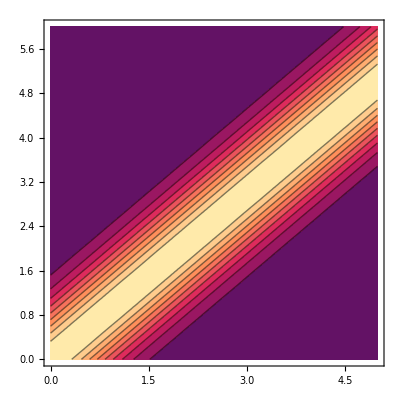

-Graphics3D-

```mathematica
a=1;
phi1[z_]:=Exp[-z^2];
(*phi1[z_]:=UnitStep[z]*)
phi[x_,t_]:=phi1[x-a*t];
ContourPlot[phi[x, t], {x,0,5}, {t,0,6}]
Plot3D[phi[x,t],{x,0,5},{t,0,6}]
```

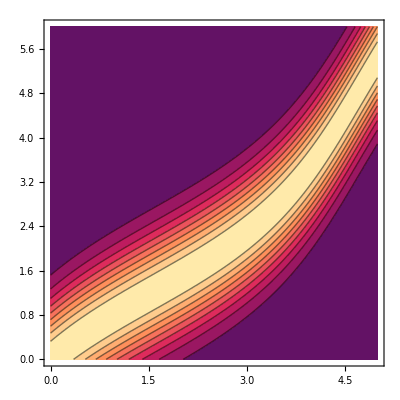

-Graphics3D-

```mathematica
ClearAll["Global`*"]
a[x_]:=1+0.5*Sin[x];
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,0,5}][[1]];
phi0[z_]:=Exp[-z^2];
(*phi0[z_]:=UnitStep[z]*)
u[x_?NumericQ,t_?NumericQ]:=phi0[t-(f[x]/. fsol)];
ContourPlot[u[x,t],{x,0,5},{t,0,6},PlotPoints->50]
Plot3D[u[x,t],{x,0,5},{t,0,6}]
```

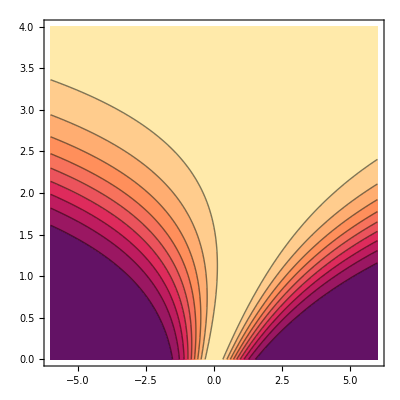

-Graphics3D-

```mathematica
ClearAll["Global`*"]
phi0[z_]:=Exp[-z^2];
(*phi0[z_]:=UnitStep[z]*)
u[x_?NumericQ,t_?NumericQ]:=phi0[Exp[-t]*(x-1-t)+Exp[-t]];
ContourPlot[u[x,t],{x,-6,6},{t,0,4},PlotPoints->50]
Plot3D[u[x,t],{x,-6,6},{t,0,4}, PlotRange->All]
```

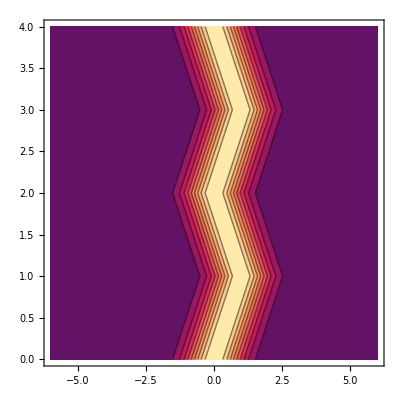

-Graphics3D-

```mathematica
(*v[t_]:=(-1)^IntegerPart[t]
a[t_]:=Piecewise[{
{FractionalPart[t],EvenQ[IntegerPart[t]]},
{1-FractionalPart[t],OddQ[IntegerPart[t]]}
}]*)
a[t_]:=(-1)^IntegerPart[t]
fsol=NDSolve[{s'[t]==a[t],s[0]==0},s,{t,0,4} ][[1]];

phi0[z_]:=Exp[-z^2];
(*phi0[z_]:=UnitStep[z]*)
u[x_?NumericQ,t_?NumericQ]:=phi0[x-(s[t]/.fsol)];
ContourPlot[u[x,t],{x,-6,6},{t,0,4},PlotPoints->50]
Plot3D[u[x,t],{x,-6,6},{t,0,4}, PlotRange->All]
```

```mathematica
ClearAll["Global`*"]
analitprobfunc[x_]:=Sin[x]^2;
phi[x_,t_]:=analitprobfunc[x-t];

Manipulate[Plot[phi[x,t],{x,-5,15},PlotRange->{-0.1,1.1},AxesLabel->{"x","φ(x,t)"}],{t,0,10,0.1}]
```

```mathematica
frames=Table[Plot[phi[x,t],{x,-5,15},PlotRange->{-0.1,1.1},AxesLabel->{"x","φ(x,t)"},PlotLabel->StringForm["t = ``",t]],{t,0,10,0.1}];
Export["wave.gif",frames]
```

wave.gif

```mathematica
NotebookDirectory[]
```

D:\Diplom\Основная папка\

```mathematica
ClearAll["Global`*"]
a[x_]:=1+0.5 Sin[x];
analitprobfuncax[x_]:=Sin[x];
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-10,10}][[1]];
uAnalytic[x_?NumericQ,t_?NumericQ]:=analitprobfuncax[-t+(f[x]/. fsol)];
Manipulate[Plot[uAnalytic[x,t],{x,-10,10},PlotRange->{-1.1,1.1},AxesLabel->{"x","φ(x,t)"}],{t,0,10,0.1}]
```

```mathematica
frames=Table[Plot[uAnalytic[x,t],{x,-10,10},PlotRange->{-1.1,1.1},AxesLabel->{"x","φ(x,t)"},PlotLabel->StringForm["t = ``",t]],{t,0,10,0.1}];
Export["wave_a(x).gif",frames]
```

wave_a(x).gif

```mathematica
ClearAll["Global`*"]
analitprobfuncxt[x_]:=Sin[x];
uAnalyticxt[x_?NumericQ,t_?NumericQ]:=analitprobfuncxt[Exp[-t]*(x-1-t)+Exp[-t]];
Manipulate[Plot[uAnalyticxt[x,t],{x,-10,10},PlotRange->{-1.1,1.1},AxesLabel->{"x","φ(x,t)"}],{t,0,10,0.1}]
```

```mathematica
frames=Table[Plot[uAnalyticxt[x,t],{x,-10,10},PlotRange->{-1.1,1.1},AxesLabel->{"x","φ(x,t)"},PlotLabel->StringForm["t = ``",t]],{t,0,10,0.1}];
Export["wave_a(x-t).gif",frames]
```

wave_a(x-t).gif

```mathematica
ClearAll["Global`*"]
(*v[t_]:=(-1)^IntegerPart[t]
a[t_]:=Piecewise[{
{FractionalPart[t],EvenQ[IntegerPart[t]]},
{1-FractionalPart[t],OddQ[IntegerPart[t]]}
}]
*)
a[t_]:=(-1)^IntegerPart[t]
analitprobfuncat[x_]:=UnitStep[x]-UnitStep[x-1]+UnitStep[x-2]-UnitStep[x-3]+UnitStep[x-4]-UnitStep[x-5]
(*analitprobfuncat[x_]:=Sin[x];*)

fsol=NDSolve[{s'[t]==a[t],s[0]==0},s,{t,0,10} ][[1]];

uAnalyticat[x_?NumericQ,t_?NumericQ]:=analitprobfuncat[x-(s[t]/.fsol)]
Manipulate[Plot[Evaluate[uAnalyticat[x,t]],{x,-1,8},PlotRange->{-0.1,1.1},AxesLabel->{"x","φ(x,t)"}],{t,0,10,0.1}]
```

```mathematica
frames=Table[Plot[Evaluate[uAnalyticat[x,t]],{x,-1,8},PlotRange->{-0.1,1.1},AxesLabel->{"x","φ(x,t)"},PlotLabel->StringForm["t = ``",t]],{t,0,10,0.1}];
Export["wave_a(t).gif",frames]
```

wave_a(t).gif

```mathematica
(*При a=const*)
ClearAll["Global`*"]
a=1;
h=0.25;
tau=0.05;
lambda=a*tau/h;
xmax=10;
nstep=200;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)

probfunc[x_]:=UnitStep[x]
uAnalytic[x_,t_]:=probfunc[Round[(x-a t)/h]*h];xgrid=Range[-xmax,xmax,h];
```

```mathematica
(*---Явная схема (против потока)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnmeth=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmeth[[1]]=probfunc/@xgrid;
Do[Do[uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-lambda*(uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnmeth[[n+1,1]]=uLeft[n*tau];
uJavnmeth[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Фридрихс)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnLaxFrid=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxFrid[[1]]=probfunc/@xgrid;
Do[
Do[
uJavnLaxFrid[[n+1,i]]=1/2*(uJavnLaxFrid[[n,i+1]]+uJavnLaxFrid[[n,i-1]])-lambda/2*(uJavnLaxFrid[[n,i+1]]-uJavnLaxFrid[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxFrid[[n+1,1]]=uLeft[n*tau];
uJavnLaxFrid[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Вендрофф)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnLaxVander=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxVander[[1]]=probfunc/@xgrid;
Do[
Do[
uJavnLaxVander[[n+1,i]]=uJavnLaxVander[[n,i]]-lambda/2*(uJavnLaxVander[[n,i+1]]-uJavnLaxVander[[n,i-1]])+lambda^2/2*(uJavnLaxVander[[n,i+1]]-2*uJavnLaxVander[[n,i]]+uJavnLaxVander[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxVander[[n+1,1]]=uLeft[n*tau];
uJavnLaxVander[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема Лакса---*)
uJavnLax=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLax[[1]]=probfunc/@xgrid;

Do[
Do[
uJavnLax[[n+1,i]]=(uJavnLax[[n,i+1]]+uJavnLax[[n,i-1]])/2-(tau/(2 h))*(a*uJavnLax[[n,i+1]]-a*uJavnLax[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLax[[n+1,1]]=uLeft[n*tau];
uJavnLax[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Центральная схема с модифицированной вязкостью---*)
uJavnVisc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnVisc[[1]]=probfunc/@xgrid;

Do[
Do[
central=-(tau/(2 h))*(a*uJavnVisc[[n,i+1]]-a*uJavnVisc[[n,i-1]]);
visc=(1/2)*(uJavnVisc[[n,i+1]]-2*uJavnVisc[[n,i]]+uJavnVisc[[n,i-1]]);
uJavnVisc[[n+1,i]]=uJavnVisc[[n,i]]+central+tau*visc;,{i,2,Length[xgrid]-1}];
uJavnVisc[[n+1,1]]=uLeft[n*tau];
uJavnVisc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Мак-Кормака---*)
uJavnMc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnMc[[1]]=probfunc/@xgrid;
uStar=ConstantArray[0,Length[xgrid]];

Do[
(*predictor*)Do[
uStar[[i]]=uJavnMc[[n,i]]-(tau/h)*(a*uJavnMc[[n,i+1]]-a*uJavnMc[[n,i]]);,{i,1,Length[xgrid]-1}];
(*corrector*)Do[
uJavnMc[[n+1,i]]=(uJavnMc[[n,i]]+uStar[[i]]-(tau/h)*(a*uStar[[i]]-a*uStar[[i-1]]))/2;,{i,2,Length[xgrid]-1}];
uJavnMc[[n+1,1]]=uLeft[n*tau];
uJavnMc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Русанова---*)
uJavnRus=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnRus[[1]]=probfunc/@xgrid;

Do[
Do[
If[a>=0,
fluxR=(a*(uJavnRus[[n,i]]+uJavnRus[[n,i+1]])/2-a*(uJavnRus[[n,i+1]]-uJavnRus[[n,i]])/2);
fluxL=(a*(uJavnRus[[n,i-1]]+uJavnRus[[n,i]])/2-a*(uJavnRus[[n,i]]-uJavnRus[[n,i-1]])/2);,

fluxR=(a*(uJavnRus[[n,i+1]]+uJavnRus[[n,i]])/2-a*(uJavnRus[[n,i]]-uJavnRus[[n,i+1]])/2);
fluxL=(a*(uJavnRus[[n,i]]+uJavnRus[[n,i-1]])/2-a*(uJavnRus[[n,i-1]]-uJavnRus[[n,i]])/2);];

uJavnRus[[n+1,i]]=uJavnRus[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];
(*Граничные условия*)uJavnRus[[n+1,1]]=uLeft[n*tau];
uJavnRus[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
(*---Схема Годунова---*)
uJavnGod=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnGod[[1]]=probfunc/@xgrid;

Do[
Do[
fluxR=If[a>0,a*uJavnGod[[n,i]],a*uJavnGod[[n,i+1]]];
fluxL=If[a>0,a*uJavnGod[[n,i-1]],a*uJavnGod[[n,i]]];
uJavnGod[[n+1,i]]=uJavnGod[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];
uJavnGod[[n+1,1]]=uLeft[n*tau];
uJavnGod[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (TVD)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnTVD=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnTVD[[1]]=probfunc/@xgrid;
Do[
Do[delm=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delp=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
r=If[delp==0,0,delm/delp];
phi=Max[0,Min[1,r]];
delmleft=uJavnTVD[[n,i-1]]-uJavnTVD[[n,i-2]];
delpleft=delm;
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[1,rleft]];
correction=phi*delp-phileft*delm;
uJavnTVD[[n+1,i]]=uJavnTVD[[n,i]]-lambda*delm-(lambda*(1-lambda)/2)*correction;,{i,3,Length[xgrid]-1}];
uJavnTVD[[n+1,1]]=uLeft[n*tau];
uJavnTVD[[n+1,2]]=uJavnTVD[[n+1,3]];
uJavnTVD[[n+1,-1]]=uRight[n*tau];
uJavnTVD[[n+1, -2]]=uJavnTVD[[n+1,-3]]
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (MUSCL) с учетом направления потока a>0/a<0---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uMUSCL=ConstantArray[0,{1+nstep,Length[xgrid]}];
uMUSCL[[1]]=probfunc/@xgrid;

Do[
Do[
If[a>0,(*поток слева:стандартный MUSCL*)delm=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delp=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
r=If[delp==0,0,delm/delp];
phi=Max[0,Min[2*r,1],Min[r,2]];
delmleft=uMUSCL[[n,i-1]]-uMUSCL[[n,i-2]];
delpleft=delm;
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[2*rleft,1],Min[rleft,2]];
correction=phi*delp-phileft*delm;
uMUSCL[[n+1,i]]=uMUSCL[[n,i]]-lambda*delm-(lambda*(1-lambda)/2)*correction,(*поток справа:для a<0 зеркально меняем разности*)delm=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
delp=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
r=If[delp==0,0,delm/delp];
phi=Max[0,Min[2*r,1],Min[r,2]];
delmright=uMUSCL[[n,i+2]]-uMUSCL[[n,i+1]];
delpright=delm;
rright=If[delpright==0,0,delmright/delpright];
phiright=Max[0,Min[2*rright,1],Min[rright,2]];
correction=phi*delp-phiright*delm;
uMUSCL[[n+1,i]]=uMUSCL[[n,i]]-lambda*delm-(lambda*(1-lambda)/2)*correction],{i,3,Length[xgrid]-2}];
(*Граничные условия*)uMUSCL[[n+1,1]]=uLeft[n*tau];
uMUSCL[[n+1,2]]=uMUSCL[[n+1,3]];
uMUSCL[[n+1,-1]]=uRight[n*tau];
uMUSCL[[n+1,-2]]=uMUSCL[[n+1,-3]];,{n,1,nstep}];
```

```mathematica
Manipulate[ListLinePlot[{
Transpose[{xgrid,uJavnmeth[[n]]}],
Transpose[{xgrid,uJavnLaxFrid[[n]]}],
Transpose[{xgrid,uJavnLaxVander[[n]]}],
Transpose[{xgrid,uJavnLax[[n]]}],
Transpose[{xgrid,uJavnVisc[[n]]}],
Transpose[{xgrid,uJavnMc[[n]]}],
Transpose[{xgrid,uJavnTVD[[n]]}],
Transpose[{xgrid,uMUSCL[[n]]}],
Transpose[{xgrid,uJavnRus[[n]]}],
Transpose[{xgrid,uJavnGod[[n]]}],
Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->{{-xmax,xmax},{-0.1,1.2}},PlotStyle->{
{Red,Thick},
{Blue,Thick},
{Orange,Thick},
{Green,Thick},
{Brown,Thick},
{Purple,Thick},
{Cyan,Thick},
{Magenta,Thick},
{Yellow,Thick},
{Darker[Magenta],Thick},
{Darker[Green],Dashed,Thick},
{Gray,Dashed,Thick}},PlotLegends->Placed[
{"Явная схема (против потока)",
"Явная схема (Лакса–Фридрихса)",
"Явная схема (Лакса–Вендроффа)",
"Схема Лакса",
"Центральная схема с модифицированной вязкостью",
"Схема Мак-Кормака",
"TVD minmod",
"MUSCL",
"Схема Русанова",
"Схема Годунова",
"Аналитическое решение"},Right],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1}]
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[
{If[showUpwind,Transpose[{xgrid,uJavnmeth[[n]]}],Nothing],
If[showLF,Transpose[{xgrid,uJavnLaxFrid[[n]]}],Nothing],
If[showLW,Transpose[{xgrid,uJavnLaxVander[[n]]}],Nothing],
If[showLax,Transpose[{xgrid,uJavnLax[[n]]}],Nothing],
If[showVisc,Transpose[{xgrid,uJavnVisc[[n]]}],Nothing],
If[showMC,Transpose[{xgrid,uJavnMc[[n]]}],Nothing],
If[showTVDmin,Transpose[{xgrid,uJavnTVD[[n]]}],Nothing],
If[showMUSCL,Transpose[{xgrid,uMUSCL[[n]]}],Nothing],
If[showRus,Transpose[{xgrid,uJavnRus[[n]]}],Nothing],
If[showGod,Transpose[{xgrid,uJavnGod[[n]]}],Nothing],
If[showExact,Transpose[{xgrid,uAnalytic[#,(n) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[
{If[showUpwind,Red,Nothing],
If[showLF,Blue,Nothing],
If[showLW,Orange,Nothing],
If[showLax,Green,Nothing],
If[showVisc,Purple,Nothing],
If[showMC,Brown,Nothing],
If[showTVDmin,RGBColor[0.1,0.5,0.8],Nothing],
If[showMUSCL,Gray,Nothing],
If[showRus,Cyan,Nothing],
If[showGod,Magenta,Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep+1,1},Delimiter,
{{showUpwind,True,Row[{Style["■",Red]," Явная схема (против потока)"}]},{True,False}},{{showLF,True,Row[{Style["■",Blue],"Явная схема (Лакса-Фридрихса)"}]},{True,False}},{{showLW,True,Row[{Style["■",Orange],"Явная схема (Лакса-Вендроффа)"}]},{True,False}},{{showLax,True,Row[{Style["■",Green],"Схема Лакса"}]},{True,False}},
{{showVisc,True,Row[{Style["■",Purple],"Центральная с вязкостью"}]},{True,False}},{{showMC,True,Row[{Style["■",Brown],"Схема Мак-Кормака"}]},{True,False}},
{{showTVDmin,True,Row[{Style["■",RGBColor[0.1,0.5,0.8]],"TVD minmod"}]},{True,False}},
{{showMUSCL,True,Row[{Style["■",Gray],"MUSCL"}]},{True,False}},
{{showRus,True,Row[{Style["■",Cyan],"Схема Русанова"}]},{True,False}},
{{showGod,True,Row[{Style["■",Magenta],"Схема Годунова"}]},{True,False}},{{showExact,True,Row[{Style["■",Yellow],"Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-50,50},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax,"Масштаб X"},1,50},{{sy,0.6,"Масштаб Y"},0.1,2},
TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showLF,showLW,showLax,showVisc,showMC,showTVDmin,showMUSCL,showRus,showGod,showExact}
]
```

```mathematica
ClearAll[normL1,normL2,normLinf]
normL1[err_,h_]:=h Total[Abs[err]]
normL2[err_,h_]:=Sqrt[h Total[err^2]]
normLinf[err_]:=Max[Abs[err]]

t[n_]:=(n-1) tau;

nstep=Length[uJavnmeth];

timeIndices=<|
"t=0"->1,
"t=T/10"->21,
"t=T/4" -> 51,
"t=T/2"->Round[nstep/2],
"t=3/4T"->151,
"t=T"->nstep|>;

ClearAll[computeErrors]

computeErrors[uNum_,n_]:=Module[
{uEx,err},uEx=uAnalytic[#,t[n]]&/@xgrid;
err=uNum-uEx;
{normL1[err,h],normL2[err,h],normLinf[err]}];

schemes=<|
"Upwind"->uJavnmeth,
"LF"->uJavnLaxFrid,
"LW"->uJavnLaxVander,
"Visc"->uJavnVisc,
"MacCormack"->uJavnMc,
"TVD"->uJavnTVD,
"MUSCL"->uMUSCL,
"Rusanov"->uJavnRus,
"Godunov"->uJavnGod|>;

errors=Association@Table[scheme->Association@Table[time->computeErrors[schemes[scheme][[timeIndices[time]]],timeIndices[time]],{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];

norms={"L1","L2","Linf"};
times={"t=0","t=T/10","t=T/4","t=T/2","t=3/4T","t=T"};

rowForScheme[scheme_]:=Flatten@Table[errors[scheme][time][[norm]],{norm,3},{time,times}];

header1=Join[{""},Flatten@Table[ConstantArray[norm,6],{norm,norms}]];

header2=Join[{"Схема"},Flatten@Table[times,{Length[norms]}]];

tableData=Join[{header1,header2},Table[Prepend[rowForScheme[scheme],scheme],{scheme,Keys[errors]}]];

Grid[tableData,Frame->All,Alignment->Center,ItemStyle->Directive[14],Background->{None,{LightGray,None}}]
```

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | Linf | Linf | Linf | Linf | Linf | Linf
Схема | t=0 | t=T/10 | t=T/4 | t=T/2 | t=3/4T | t=T | t=0 | t=T/10 | t=T/4 | t=T/2 | t=3/4T | t=T | t=0 | t=T/10 | t=T/4 | t=T/2 | t=3/4T | t=T
Upwind | 0. | 0.349119 | 0.559276 | 0.792404 | 0.962785 | 0.562957 | 0. | 0.316556 | 0.40307 | 0.482237 | 0.533346 | 0.410528 | 0 | 0.411449 | 0.44374 | 0.480021 | 0.467457 | 0.47181
LF | 0. | 0.862588 | 1.3747 | 1.93074 | 1.98726 | 1.58365 | 0. | 0.498726 | 0.632568 | 0.759139 | 0.794838 | 0.785759 | 0 | 0.415893 | 0.446476 | 0.505437 | 0.468339 | 0.784775
LW | 0. | 0.385765 | 0.54014 | 0.726203 | 0.829881 | 0.734478 | 0. | 0.314396 | 0.372391 | 0.444363 | 0.457651 | 0.424997 | 0 | 0.492837 | 0.541595 | 0.607825 | 0.581873 | 0.474252
Visc | 0. | 0.355065 | 0.47465 | 0.61606 | 0.682226 | 0.531995 | 0. | 0.298994 | 0.350335 | 0.412494 | 0.421254 | 0.364111 | 0 | 0.478548 | 0.521665 | 0.581715 | 0.553175 | 0.444121
MacCormack | 0. | 0.385765 | 0.54014 | 0.726203 | 0.829881 | 0.734478 | 0. | 0.314396 | 0.372391 | 0.444363 | 0.457651 | 0.424997 | 0 | 0.492837 | 0.541595 | 0.607825 | 0.581873 | 0.474252
TVD | 0. | 0.223881 | 0.318559 | 0.410668 | 0.476283 | 0.254696 | 0. | 0.238135 | 0.289309 | 0.331977 | 0.35752 | 0.246049 | 0 | 0.324678 | 0.367891 | 0.423464 | 0.41605 | 0.315636
MUSCL | 0. | 0.152264 | 0.180149 | 0.198493 | 0.204934 | 0.100276 | 0. | 0.192387 | 0.216838 | 0.23288 | 0.236226 | 0.132026 | 0 | 0.282549 | 0.323302 | 0.364004 | 0.349597 | 0.186048
Rusanov | 0. | 0.349119 | 0.559276 | 0.792404 | 0.962785 | 0.562957 | 0. | 0.316556 | 0.40307 | 0.482237 | 0.533346 | 0.410528 | 0 | 0.411449 | 0.44374 | 0.480021 | 0.467457 | 0.47181
Godunov | 0. | 0.349119 | 0.559276 | 0.792404 | 0.962785 | 0.562957 | 0. | 0.316556 | 0.40307 | 0.482237 | 0.533346 | 0.410528 | 0 | 0.411449 | 0.44374 | 0.480021 | 0.467457 | 0.47181

```mathematica
schemeColors=<|"Upwind"->Red,"LF"->Blue,"LW"->Orange,"Visc"->Purple,"MacCormack"->Brown,"TVD"->RGBColor[0.1,0.5,0.8],"MUSCL"->Gray,"Rusanov"->Cyan,"Godunov"->Magenta|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

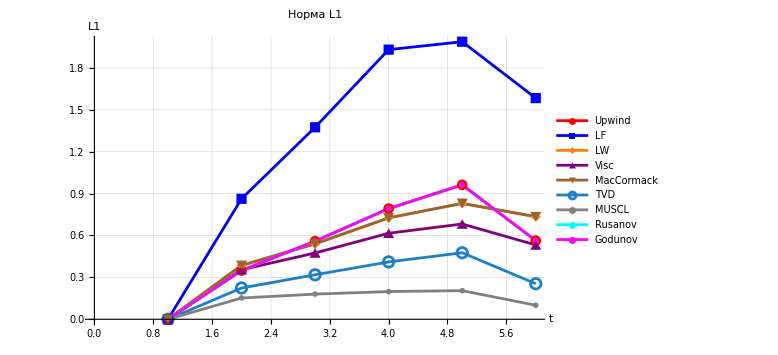

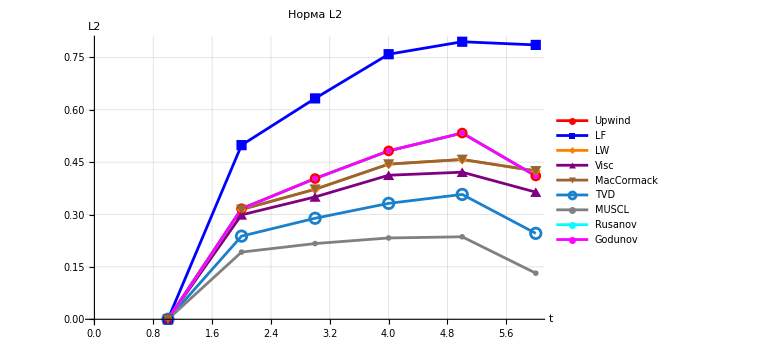

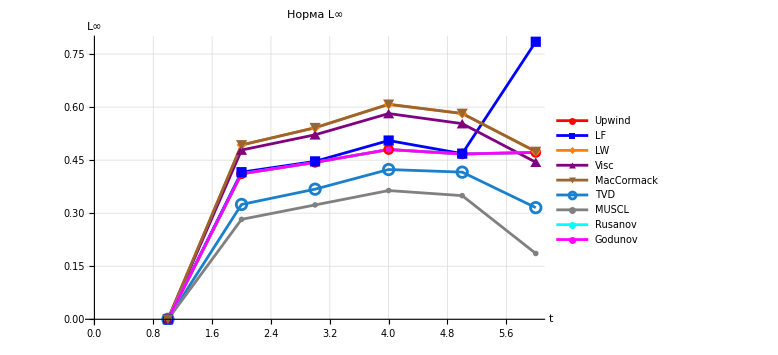

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

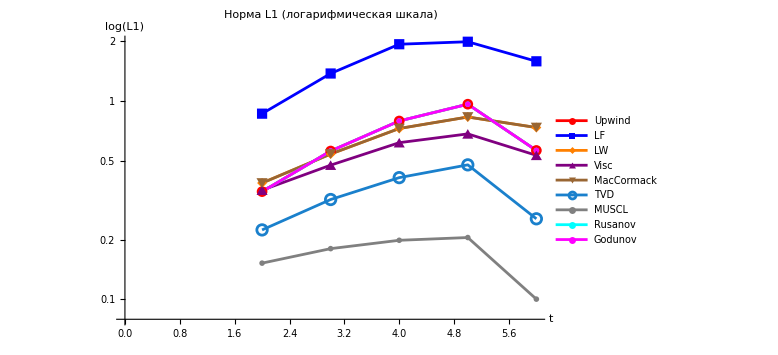

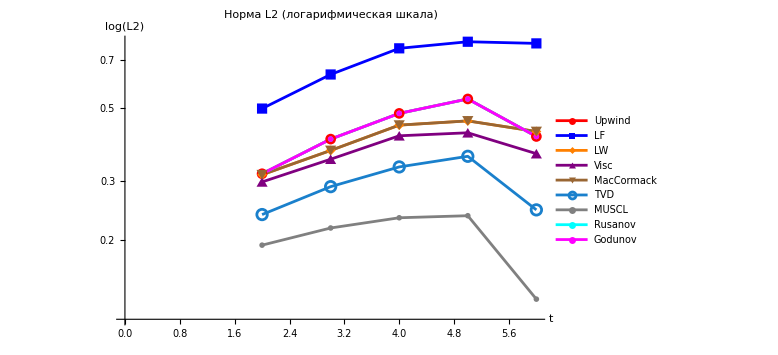

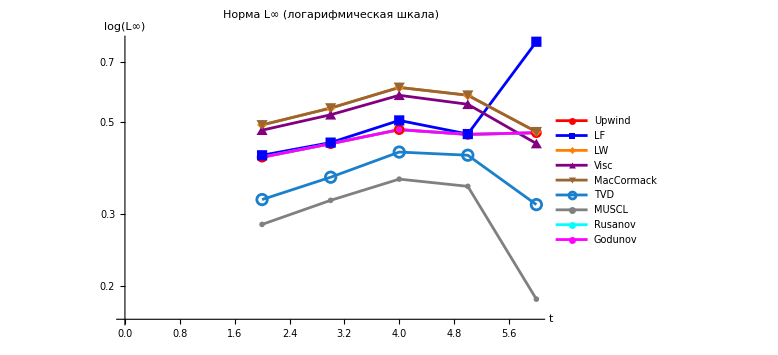

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=3/4T"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 3/4T",14],ImageSize->Large]
```

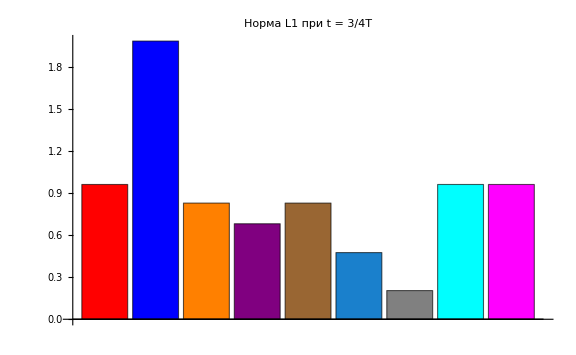

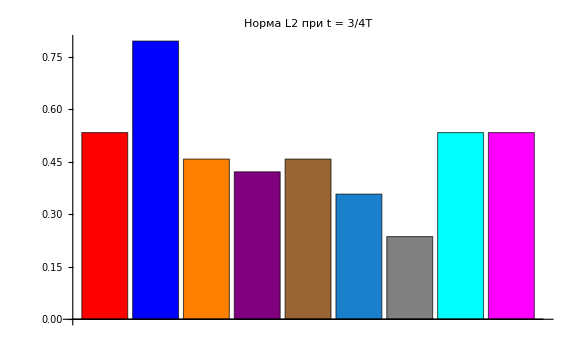

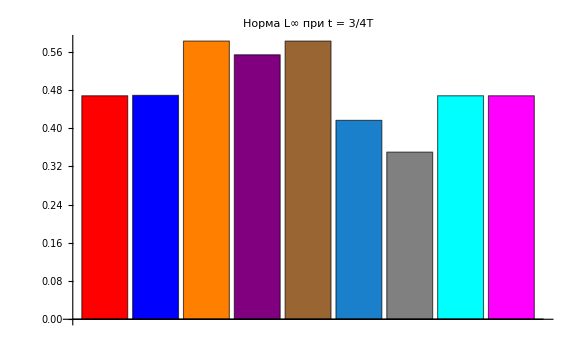

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
heatMapNorm[normIndex_,normName_]:=ArrayPlot[getNormData[normIndex],ColorFunction->"ThermometerColors",FrameTicks->{Thread[{Range[Length[Keys[schemes]]],Keys[schemes]}],Thread[{Range[Length[times]],times}]},PlotLabel->Style["Тепловая карта нормы "<>normName,14],ImageSize->Large]
```

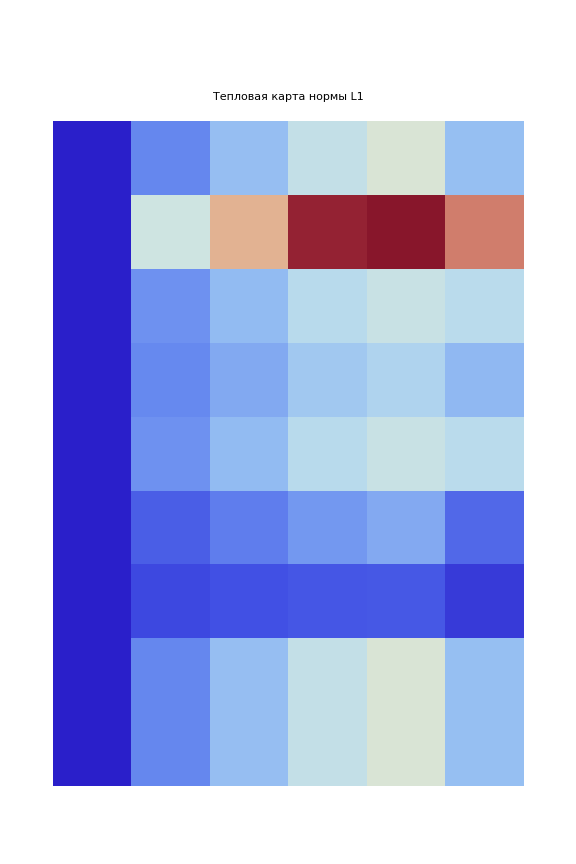

```mathematica
heatMapNorm[1,"L1"]
```

```mathematica
stepForFrames=1;

activeSchemes={
{uJavnmeth,Red},
{uJavnLaxFrid,Blue},
{uJavnLaxVander,Orange},
(*{uJavnLax,Green},*)
{uJavnVisc,Purple},
{uJavnMc,Brown},
{uJavnTVD,RGBColor[0.1,0.5,0.8]},
{uMUSCL,Gray},
{uJavnRus,Cyan},
{uJavnGod,Magenta},
{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow}};


plotAt[n_]:=Module[{lines},lines=Map[Function[{dataCol},Module[{data=dataCol[[1]],col=dataCol[[2]],yvals},yvals=If[Head[data]===Function,data[n],data[[n]]];
Transpose[{xgrid,yvals}]]],activeSchemes];
ListLinePlot[lines,PlotStyle->activeSchemes[[All,2]],PlotRange->{{-1,xmax},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];

frames=Table[plotAt[n],{n,1,nstep,stepForFrames}];


Export["transport_schemes_javn_a_const.gif",frames,"DisplayDurations"->0.05,"AnimationRepetitions"->Infinity];
(*Export["transport_schemes_javn_a_const.mp4",frames,"FrameRate"->30];*)
```

```mathematica
plotAtTime[n_]:=ListLinePlot[DeleteCases[{If[showUpwind,Transpose[{xgrid,uJavnmeth[[n]]}],Nothing],If[showLF,Transpose[{xgrid,uJavnLaxFrid[[n]]}],Nothing],If[showLW,Transpose[{xgrid,uJavnLaxVander[[n]]}],Nothing],(*If[showLax,Transpose[{xgrid,uJavnLax[[n]]}],Nothing],*)If[showVisc,Transpose[{xgrid,uJavnVisc[[n]]}],Nothing],If[showMC,Transpose[{xgrid,uJavnMc[[n]]}],Nothing],If[showTVDmin,Transpose[{xgrid,uJavnTVD[[n]]}],Nothing],If[showMUSCL,Transpose[{xgrid,uMUSCL[[n]]}],Nothing],If[showRus,Transpose[{xgrid,uJavnRus[[n]]}],Nothing],If[showGod,Transpose[{xgrid,uJavnGod[[n]]}],Nothing],If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[{If[showUpwind,Red,Nothing],
If[showLF,Blue,Nothing],
If[showLW,Orange,Nothing],
(*If[showLax,Green,Nothing],*)
If[showVisc,Purple,Nothing],
If[showMC,Brown,Nothing],
If[showRus,Cyan,Nothing],
If[showGod,Magenta,Nothing],
If[showTVDmin,RGBColor[0.1,0.5,0.8],Nothing],
If[showMUSCL,Gray,Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotLegends->Placed[LineLegend[DeleteCases[{If[showUpwind,"2.1 Против потока",Nothing],If[showLF,"2.2 Лакс–Фридрихс",Nothing],If[showLW,"2.3 Лакс–Вендрофф",Nothing],(*If[showLax,"Схема Лакса",Nothing],*)If[showVisc,"2.4 Центральная с вязкостью",Nothing],If[showMC,"2.5 Мак-Кормак",Nothing],If[showRus,"2.6 Русанова",Nothing], If[showGod,"2.7 Годунова",Nothing], If[showTVDmin,"2.8 TVD minmod",Nothing],If[showMUSCL,"2.9 MUSCL-схема",Nothing],If[showExact,"Аналитическое решение",Nothing]},Nothing]],Right],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotRange->{{x0-sx,x0+sx},{y0-sy,y0+sy}},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]];
```

```mathematica
x0=4.2;y0=0.5;sx=3.9;sy=0.555;
showUpwind=showLF=showLW=showLax=True;
showVisc=showMC=showTVDmin=showMUSCL=showRus=showGod=True;
showExact=True;

Export["solution_t20.pdf",plotAtTime[70]]
```

solution_t20.pdf

```mathematica
Manipulate[plotAtTime[n],{n,1,nstep,1}]
```

```mathematica
(*При a=a(x)*)
ClearAll["Global`*"]
h=0.25;
tau=0.05;
xmax=20;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)
a[x_]:=1+0.5 Sin[x];
probfunc[x_]:=UnitStep[x]
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-xmax,xmax}][[1]];
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[-t+(f[x]/. fsol)];xgrid=Range[-xmax,xmax,h];
```

```mathematica
(*---Явная схема (против потока)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnmeth=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmeth[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[xgrid[[i]]];
If[ai>0,
uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(ai*tau/h) (uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]),uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(ai*tau/h) (uJavnmeth[[n,i+1]]-uJavnmeth[[n,i]])];
,{i,2,Length[xgrid]-1}];
uJavnmeth[[n+1,1]]=uLeft[n*tau];
uJavnmeth[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Фридрихс)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxFrid=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxFrid[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[xgrid[[i]]];
lambdaax=ai*tau/h;
uJavnLaxFrid[[n+1,i]]=1/2*(uJavnLaxFrid[[n,i+1]]+uJavnLaxFrid[[n,i-1]])-lambdaax/2*(uJavnLaxFrid[[n,i+1]]-uJavnLaxFrid[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxFrid[[n+1,1]]=uLeft[n*tau];
uJavnLaxFrid[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Вендрофф)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxVander=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxVander[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[xgrid[[i]]];
lambdaax=ai*tau/h;
uJavnLaxVander[[n+1,i]]=uJavnLaxVander[[n,i]]-lambdaax/2*(uJavnLaxVander[[n,i+1]]-uJavnLaxVander[[n,i-1]])+lambdaax^2/2*(uJavnLaxVander[[n,i+1]]-2*uJavnLaxVander[[n,i]]+uJavnLaxVander[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxVander[[n+1,1]]=uLeft[n*tau];
uJavnLaxVander[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема Лакса---*)
uJavnLax=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLax[[1]]=probfunc/@xgrid;

Do[
Do[ai=a[xgrid[[i]]];
uJavnLax[[n+1,i]]=(uJavnLax[[n,i+1]]+uJavnLax[[n,i-1]])/2-(tau/(2 h))*(ai*uJavnLax[[n,i+1]]-ai*uJavnLax[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLax[[n+1,1]]=uLeft[n*tau];
uJavnLax[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Центральная схема с модифицированной вязкостью---*)
uJavnVisc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnVisc[[1]]=probfunc/@xgrid;

Do[
Do[ai=a[xgrid[[i]]];
central=-(tau/(2 h))*(ai*uJavnVisc[[n,i+1]]-ai*uJavnVisc[[n,i-1]]);
visc=(h^2/(2 tau))*(uJavnVisc[[n,i+1]]-2*uJavnVisc[[n,i]]+uJavnVisc[[n,i-1]]);
uJavnVisc[[n+1,i]]=uJavnVisc[[n,i]]+central+tau*visc;,{i,2,Length[xgrid]-1}];
uJavnVisc[[n+1,1]]=uLeft[n*tau];
uJavnVisc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Мак-Кормака---*)
uJavnMc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnMc[[1]]=probfunc/@xgrid;
uStar=ConstantArray[0,Length[xgrid]];

Do[
(*predictor*)Do[ai=a[xgrid[[i]]];
uStar[[i]]=uJavnMc[[n,i]]-(tau/h)*(ai*uJavnMc[[n,i+1]]-ai*uJavnMc[[n,i]]);,{i,1,Length[xgrid]-1}];
(*corrector*)Do[ai=a[xgrid[[i]]];
uJavnMc[[n+1,i]]=(uJavnMc[[n,i]]+uStar[[i]]-(tau/h)*(ai*uStar[[i]]-ai*uStar[[i-1]]))/2;,{i,2,Length[xgrid]-1}];
uJavnMc[[n+1,1]]=uLeft[n*tau];
uJavnMc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Русанова с учетом направления потока---*)
uJavnRus=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnRus[[1]]=probfunc/@xgrid;

Do[
Do[
ai=a[xgrid[[i]]];
If[ai>0,
fluxR=(ai*(uJavnRus[[n,i]]+uJavnRus[[n,i+1]])/2-ai*(uJavnRus[[n,i+1]]-uJavnRus[[n,i]])/2);
fluxL=(ai*(uJavnRus[[n,i-1]]+uJavnRus[[n,i]])/2-ai*(uJavnRus[[n,i]]-uJavnRus[[n,i-1]])/2);,

fluxR=(ai*(uJavnRus[[n,i+1]]+uJavnRus[[n,i]])/2-ai*(uJavnRus[[n,i]]-uJavnRus[[n,i+1]])/2);
fluxL=(ai*(uJavnRus[[n,i]]+uJavnRus[[n,i-1]])/2-ai*(uJavnRus[[n,i-1]]-uJavnRus[[n,i]])/2);];
uJavnRus[[n+1,i]]=uJavnRus[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];
(*граничные условия*)uJavnRus[[n+1,1]]=uLeft[n*tau];
uJavnRus[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
(*---Схема Годунова---*)
uJavnGod=ConstantArray[0,{1+nstep,Length[xgrid]}];uJavnGod[[1]]=probfunc/@xgrid;Do[Do[ai=a[xgrid[[i]]];fluxR=If[ai>0,ai*uJavnGod[[n,i]],ai*uJavnGod[[n,i+1]]];fluxL=If[ai>0,ai*uJavnGod[[n,i-1]],ai*uJavnGod[[n,i]]];uJavnGod[[n+1,i]]=uJavnGod[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];uJavnGod[[n+1,1]]=uLeft[n*tau];uJavnGod[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (TVD) с учетом a>0 или a<0---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnTVD=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnTVD[[1]]=probfunc/@xgrid;

Do[
Do[
ai=a[xgrid[[i]]];
lambdaax=Abs[ai]*tau/h;
If[ai>0,
delm=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delp=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
delmleft=uJavnTVD[[n,i-1]]-uJavnTVD[[n,i-2]];
delpleft=delm;,

delm=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
delp=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delmleft=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delpleft=delm;];

r=If[delp==0,0,delm/delp];
phi=Max[0,Min[1,r]];
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[1,rleft]];
correction=phi*delp-phileft*delm;
uJavnTVD[[n+1,i]]=uJavnTVD[[n,i]]-Sign[ai]*lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-2}];uJavnTVD[[n+1,1]]=uLeft[n*tau];
uJavnTVD[[n+1,2]]=uJavnTVD[[n+1,3]];
uJavnTVD[[n+1,-2]]=uJavnTVD[[n+1,-3]];
uJavnTVD[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
(*---Явная схема (MUSCL)*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uMUSCL=ConstantArray[0,{1+nstep,Length[xgrid]}];
uMUSCL[[1]]=probfunc/@xgrid;

Do[
Do[
ai=a[xgrid[[i]]];lambdaax=Abs[ai]*tau/h;
If[
ai>0,
delm=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delp=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
delmleft=uMUSCL[[n,i-1]]-uMUSCL[[n,i-2]];
delpleft=delm;,

delm=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
delp=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delmleft=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delpleft=delm;];

r=If[delp==0,0,delm/delp];
phi=Max[0,Min[2 r,1],Min[r,2]];
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[2 rleft,1],Min[rleft,2]];
correction=phi*delp-phileft*delm;
uMUSCL[[n+1,i]]=uMUSCL[[n,i]]-Sign[ai]*lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-2}];
uMUSCL[[n+1,1]]=uLeft[n*tau];
uMUSCL[[n+1,2]]=uMUSCL[[n+1,3]];
uMUSCL[[n+1,-2]]=uMUSCL[[n+1,-3]];
uMUSCL[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
Manipulate[ListLinePlot[{
Transpose[{xgrid,uJavnmeth[[n]]}],
Transpose[{xgrid,uJavnLaxFrid[[n]]}],
Transpose[{xgrid,uJavnLaxVander[[n]]}],
Transpose[{xgrid,uJavnLax[[n]]}],
Transpose[{xgrid,uJavnVisc[[n]]}],
Transpose[{xgrid,uJavnMc[[n]]}],
Transpose[{xgrid,uJavnTVD[[n]]}],
Transpose[{xgrid,uMUSCL[[n]]}],
Transpose[{xgrid,uJavnRus[[n]]}],
Transpose[{xgrid,uJavnGod[[n]]}],
Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->{{-xmax,xmax},{-0.1,1.2}},PlotStyle->{
{Red,Thick},
{Blue,Thick},
{Orange,Thick},
{Green,Thick},
{Brown,Thick},
{Purple,Thick},
{Cyan,Thick},
{Magenta,Thick},
{Yellow,Thick},
{Darker[Magenta],Thick},
{Black,Dashed,Thick},
{Gray,Dashed,Thick}},PlotLegends->Placed[
{"Явная схема (против потока)",
"Явная схема (Лакса–Фридрихса)",
"Явная схема (Лакса–Вендроффа)",
"Схема Лакса",
"Центральная схема с модифицированной вязкостью",
"Схема Мак-Кормака",
"TVD minmod",
"MUSCL",
"Схема Русанова",
"Схема Годунова",
"Аналитическое решение"},Right],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1}]
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[
{If[showUpwind,Transpose[{xgrid,uJavnmeth[[n]]}],Nothing],
If[showLF,Transpose[{xgrid,uJavnLaxFrid[[n]]}],Nothing],
If[showLW,Transpose[{xgrid,uJavnLaxVander[[n]]}],Nothing],
If[showLax,Transpose[{xgrid,uJavnLax[[n]]}],Nothing],
If[showVisc,Transpose[{xgrid,uJavnVisc[[n]]}],Nothing],
If[showMC,Transpose[{xgrid,uJavnMc[[n]]}],Nothing],
If[showTVDmin,Transpose[{xgrid,uJavnTVD[[n]]}],Nothing],
If[showMUSCL,Transpose[{xgrid,uMUSCL[[n]]}],Nothing],
If[showRus,Transpose[{xgrid,uJavnRus[[n]]}],Nothing],
If[showGod,Transpose[{xgrid,uJavnGod[[n]]}],Nothing],
If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[
{If[showUpwind,Red,Nothing],
If[showLF,Blue,Nothing],
If[showLW,Orange,Nothing],
If[showLax,Green,Nothing],
If[showVisc,Purple,Nothing],
If[showMC,Brown,Nothing],
If[showTVDmin,RGBColor[0.1,0.5,0.8],Nothing],
If[showMUSCL,Gray,Nothing],
If[showRus,Cyan,Nothing],
If[showGod,Magenta,Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep+1,1},Delimiter,
{{showUpwind,True,Row[{Style["■",Red]," Явная схема (против потока)"}]},{True,False}},{{showLF,True,Row[{Style["■",Blue],"Явная схема (Лакса-Фридрихса)"}]},{True,False}},{{showLW,True,Row[{Style["■",Orange],"Явная схема (Лакса-Вендроффа)"}]},{True,False}},{{showLax,True,Row[{Style["■",Green],"Схема Лакса"}]},{True,False}},
{{showVisc,True,Row[{Style["■",Purple],"Центральная с вязкостью"}]},{True,False}},{{showMC,True,Row[{Style["■",Brown],"Схема Мак-Кормака"}]},{True,False}},
{{showTVDmin,True,Row[{Style["■",RGBColor[0.1,0.5,0.8]],"TVD minmod"}]},{True,False}},
{{showMUSCL,True,Row[{Style["■",Gray],"MUSCL"}]},{True,False}},
{{showRus,True,Row[{Style["■",Cyan],"Схема Русанова"}]},{True,False}},
{{showGod,True,Row[{Style["■",Magenta],"Схема Годунова"}]},{True,False}},{{showExact,True,Row[{Style["■",Yellow],"Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-50,50},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax,"Масштаб X"},1,50},{{sy,0.6,"Масштаб Y"},0.1,2},
TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showLF,showLW,showLax,showVisc,showMC,showTVDmin,showMUSCL,showRus,showGod,showExact}
]
```

```mathematica
ClearAll[normL1,normL2,normLinf]
normL1[err_,h_]:=h Total[Abs[err]]
normL2[err_,h_]:=Sqrt[h Total[err^2]]
normLinf[err_]:=Max[Abs[err]]

t[n_]:=(n-1) tau;

nstep=Length[uJavnmeth];

timeIndices=<|
"t=2.5"->51,"t=5"->101,"t=9"->181,"t=13"->261,"t=16"->321,"t=20"->401|>;

ClearAll[computeErrors]

computeErrors[uNum_,n_]:=Module[
{uEx,err},uEx=uAnalytic[#,t[n]]&/@xgrid;
err=uNum-uEx;
{normL1[err,h],normL2[err,h],normLinf[err]}];

schemes=<|
"Upwind"->uJavnmeth,
"LF"->uJavnLaxFrid,
"LW"->uJavnLaxVander,
"Visc"->uJavnVisc,
"MacCormack"->uJavnMc,
"TVD"->uJavnTVD,
"MUSCL"->uMUSCL,
"Rusanov"->uJavnRus,
"Godunov"->uJavnGod|>;

errors=Association@Table[scheme->Association@Table[time->computeErrors[schemes[scheme][[timeIndices[time]]],timeIndices[time]],{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];

norms={"L1","L2","Linf"};
times={"t=2.5","t=5","t=9","t=13","t=16","t=20"};

rowForScheme[scheme_]:=Flatten@Table[errors[scheme][time][[norm]],{norm,3},{time,times}];

header1=Join[{""},Flatten@Table[ConstantArray[norm,6],{norm,norms}]];

header2=Join[{"Схема"},Flatten@Table[times,{Length[norms]}]];

tableData=Join[{header1,header2},Table[Prepend[rowForScheme[scheme],scheme],{scheme,Keys[errors]}]];

Grid[tableData,Frame->All,Alignment->Center,ItemStyle->Directive[14],Background->{None,{LightGray,None}}]
```

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | Linf | Linf | Linf | Linf | Linf | Linf
Схема | t=2.5 | t=5 | t=9 | t=13 | t=16 | t=20 | t=2.5 | t=5 | t=9 | t=13 | t=16 | t=20 | t=2.5 | t=5 | t=9 | t=13 | t=16 | t=20
Upwind | 0.494798 | 0.519127 | 1.36741 | 1.06797 | 1.74639 | 1.2087 | 0.377581 | 0.402506 | 0.662286 | 0.527692 | 0.76586 | 0.583561 | 0.463456 | 0.553613 | 0.496716 | 0.4621 | 0.507056 | 0.502078
LF | 1.41426 | 1.83265 | 2.79841 | 3.29206 | 3.38356 | 2.54098 | 0.638222 | 0.701547 | 0.925416 | 0.998603 | 1.05347 | 0.885104 | 0.556267 | 0.486944 | 0.545623 | 0.520893 | 0.564616 | 0.53714
LW | 0.586033 | 0.593072 | 1.18669 | 0.779632 | 1.46256 | 1.05414 | 0.385127 | 0.453468 | 0.618047 | 0.411806 | 0.711625 | 0.502705 | 0.570328 | 0.704803 | 0.653737 | 0.554001 | 0.679856 | 0.642745
Visc | 0.473724 | 0.407901 | 0.957419 | 0.596127 | 1.26629 | 0.706791 | 0.376935 | 0.362969 | 0.555405 | 0.398992 | 0.652502 | 0.448419 | 0.587265 | 0.594932 | 0.531764 | 0.446226 | 0.541504 | 0.508897
MacCormack | 0.605667 | 0.596641 | 1.18829 | 0.774259 | 1.46044 | 1.047 | 0.393152 | 0.446557 | 0.622517 | 0.407359 | 0.714621 | 0.497569 | 0.576531 | 0.695003 | 0.658419 | 0.545228 | 0.683345 | 0.635763
TVD | 0.273037 | 0.2896 | 0.795279 | 0.442655 | 0.998021 | 0.505806 | 0.265274 | 0.315856 | 0.481873 | 0.334522 | 0.552598 | 0.35946 | 0.383832 | 0.547689 | 0.495911 | 0.412303 | 0.521247 | 0.453288
MUSCL | 0.147284 | 0.185653 | 0.467027 | 0.190399 | 0.528646 | 0.1916 | 0.186942 | 0.275132 | 0.380887 | 0.229362 | 0.415684 | 0.236066 | 0.307655 | 0.531153 | 0.475589 | 0.36892 | 0.515132 | 0.407937
Rusanov | 0.494798 | 0.519127 | 1.36741 | 1.06797 | 1.74639 | 1.2087 | 0.377581 | 0.402506 | 0.662286 | 0.527692 | 0.76586 | 0.583561 | 0.463456 | 0.553613 | 0.496716 | 0.4621 | 0.507056 | 0.502078
Godunov | 0.494798 | 0.519127 | 1.36741 | 1.06797 | 1.74639 | 1.2087 | 0.377581 | 0.402506 | 0.662286 | 0.527692 | 0.76586 | 0.583561 | 0.463456 | 0.553613 | 0.496716 | 0.4621 | 0.507056 | 0.502078

```mathematica
schemeColors=<|"Upwind"->Red,"LF"->Blue,"LW"->Orange,"Visc"->Purple,"MacCormack"->Brown,"TVD"->RGBColor[0.1,0.5,0.8],"MUSCL"->Gray,"Rusanov"->Cyan,"Godunov"->Magenta|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

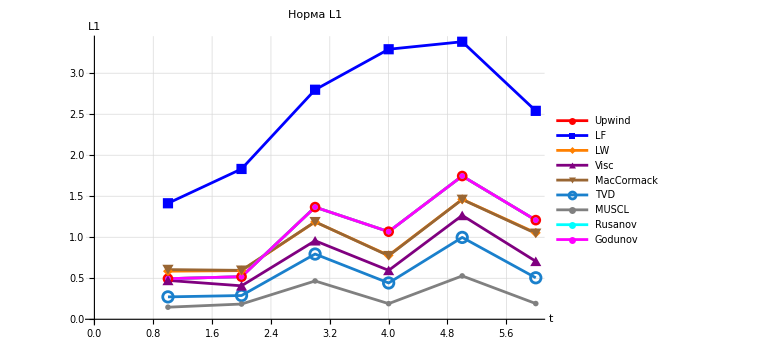

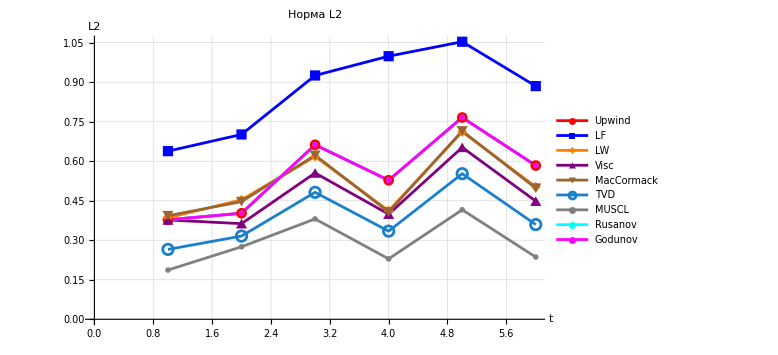

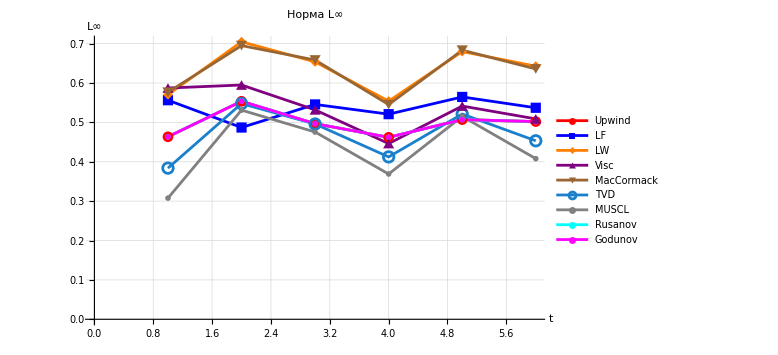

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

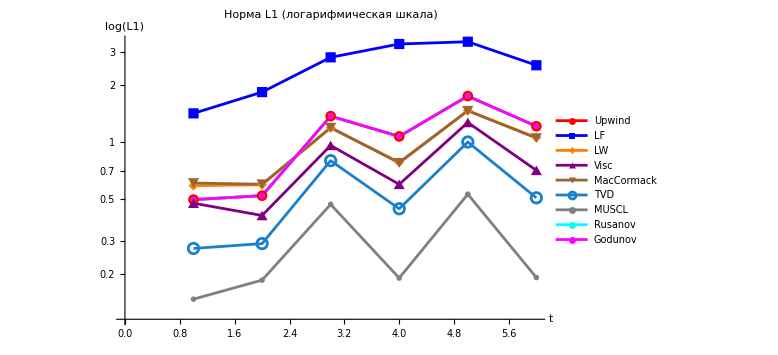

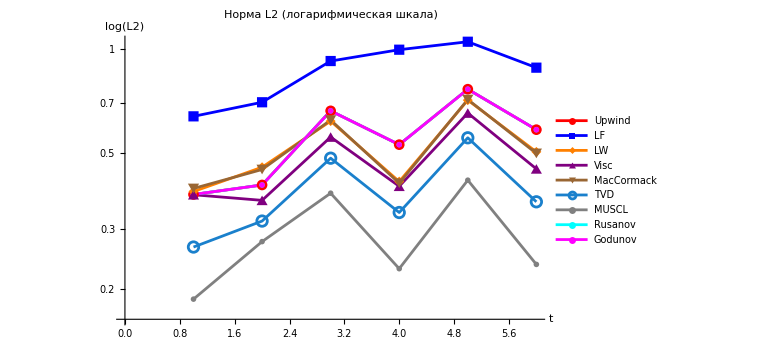

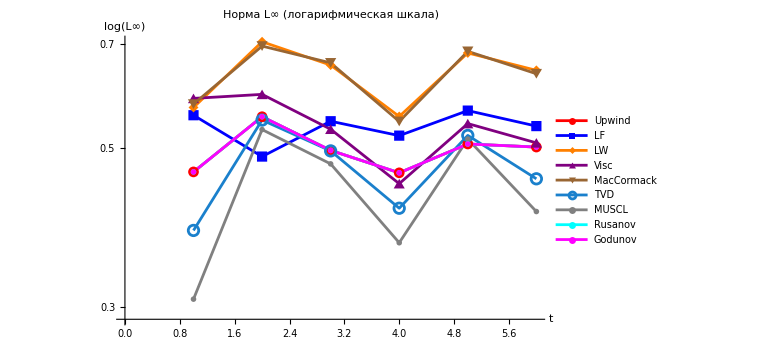

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=16"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 16",14],ImageSize->Large]
```

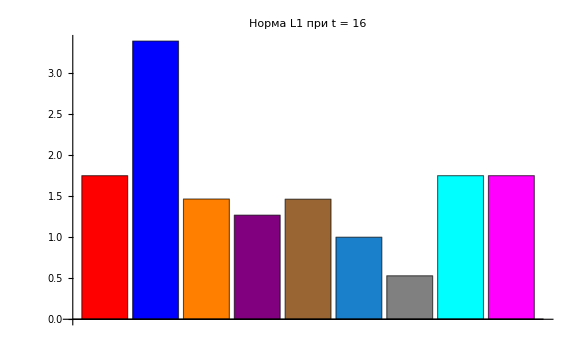

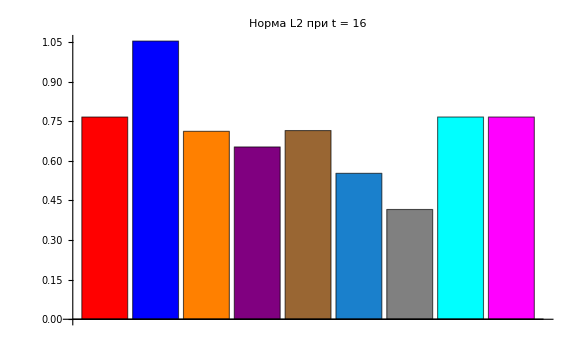

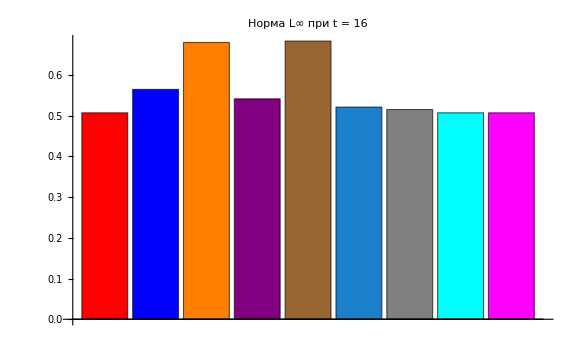

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
stepForFrames=1;

activeSchemes={
{uJavnmeth,Red},
{uJavnLaxFrid,Blue},
{uJavnLaxVander,Orange},
(*{uJavnLax,Green},*)
{uJavnVisc,Purple},
{uJavnMc,Brown},
{uJavnTVD,RGBColor[0.1,0.5,0.8]},
{uMUSCL,Gray},
{uJavnRus,Cyan},
{uJavnGod,Magenta},
{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow}};


plotAt[n_]:=Module[{lines},lines=Map[Function[{dataCol},Module[{data=dataCol[[1]],col=dataCol[[2]],yvals},yvals=If[Head[data]===Function,data[n],data[[n]]];
Transpose[{xgrid,yvals}]]],activeSchemes];
ListLinePlot[lines,PlotStyle->activeSchemes[[All,2]],PlotRange->{{-3,xmax},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];

frames=Table[plotAt[n],{n,1,nstep,stepForFrames}];


Export["transport_schemes_javn_a(x).gif",frames,"DisplayDurations"->0.03,"AnimationRepetitions"->Infinity];
(*Export["transport_schemes_javn_a(x).mp4",frames,"FrameRate"->30];*)
```

```mathematica
(*При a=x-t*)
ClearAll["Global`*"]

(*
h=0.25;        (*шаг по пространству*)
tau=0.015;    (*шаг по времени,CFL~0.9*)
xmax=10;      (*границы сетки*)
nstep=1333;   (*шаги по времени,t_max=nstep*tau≈20*)
*)

h=0.5;
tau=0.012;     (*CFL≈0.72*)
xmax=10;
nstep=1667;    (*t_max≈20*)
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)
a[x_]:=1+0.5 Sin[x];
probfunc[x_]:=UnitStep[x]
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[Exp[-t]*(x-1-t)+Exp[-t]];xgrid=Range[-xmax,xmax,h];
```

```mathematica
(*---Явная схема (против потока)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnmeth=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmeth[[1]]=probfunc/@xgrid;
Do[
tCurr=(n-1)*tau;
Do[
ai=xgrid[[i]]-tCurr;
If[ai>0,
uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(Abs[ai] tau/h) (uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]),uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(Abs[ai] tau/h) (uJavnmeth[[n,i+1]]-uJavnmeth[[n,i]])]
,{i,2,Length[xgrid]-1}];
uJavnmeth[[n+1,1]]=uLeft[tCurr];
uJavnmeth[[n+1,-1]]=uRight[tCurr];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема консервативная (против потока)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];
uJavnmethCons=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmethCons[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
Do[aiLeft=(xgrid[[i-1]]-tCurr+xgrid[[i]]-tCurr)/2;(*a на левой границе*)aiRight=(xgrid[[i]]-tCurr+xgrid[[i+1]]-tCurr)/2;(*a на правой границе*)FLeft=If[aiLeft>0,aiLeft*uJavnmethCons[[n,i-1]],aiLeft*uJavnmethCons[[n,i]]];
FRight=If[aiRight>0,aiRight*uJavnmethCons[[n,i]],aiRight*uJavnmethCons[[n,i+1]]];
uJavnmethCons[[n+1,i]]=uJavnmethCons[[n,i]]-(tau/h)*(FRight-FLeft);,{i,2,Length[xgrid]-1}];
uJavnmethCons[[n+1,1]]=uLeft[tCurr];
uJavnmethCons[[n+1,-1]]=uRight[tCurr];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Фридрихс)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxFrid=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxFrid[[1]]=probfunc/@xgrid;
Do[
tCurr=(n-1)*tau;
Do[
ai=xgrid[[i]]-tCurr;
lambdaai=ai*tau/h;
uJavnLaxFrid[[n+1,i]]=1/2*(uJavnLaxFrid[[n,i+1]]+uJavnLaxFrid[[n,i-1]])-lambdaai/2*(uJavnLaxFrid[[n,i+1]]-uJavnLaxFrid[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxFrid[[n+1,1]]=uLeft[tCurr];
uJavnLaxFrid[[n+1,-1]]=uRight[tCurr];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Вендрофф)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxVander=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxVander[[1]]=probfunc/@xgrid;
Do[
tCurr=(n-1)*tau;
Do[
ai=xgrid[[i]]-tCurr;
lambdaax=ai*tau/h;
uJavnLaxVander[[n+1,i]]=uJavnLaxVander[[n,i]]-lambdaax/2*(uJavnLaxVander[[n,i+1]]-uJavnLaxVander[[n,i-1]])+lambdaax^2/2*(uJavnLaxVander[[n,i+1]]-2*uJavnLaxVander[[n,i]]+uJavnLaxVander[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxVander[[n+1,1]]=uLeft[n*tau];
uJavnLaxVander[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема Лакса---*)
uJavnLax=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLax[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
Do[ai=xgrid[[i]]-tCurr;
uJavnLax[[n+1,i]]=(uJavnLax[[n,i+1]]+uJavnLax[[n,i-1]])/2-(tau/(2 h))*(ai*uJavnLax[[n,i+1]]-ai*uJavnLax[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLax[[n+1,1]]=uLeft[n*tau];
uJavnLax[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Центральная схема с модифицированной вязкостью---*)
uJavnVisc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnVisc[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
Do[ai=xgrid[[i]]-tCurr;
central=-(tau/(2 h))*(ai*uJavnVisc[[n,i+1]]-ai*uJavnVisc[[n,i-1]]);
visc=(h^2/(2 tau))*(uJavnVisc[[n,i+1]]-2*uJavnVisc[[n,i]]+uJavnVisc[[n,i-1]]);
uJavnVisc[[n+1,i]]=uJavnVisc[[n,i]]+central+tau*visc;,{i,2,Length[xgrid]-1}];
uJavnVisc[[n+1,1]]=uLeft[n*tau];
uJavnVisc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Мак-Кормака---*)
uJavnMc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnMc[[1]]=probfunc/@xgrid;
uStar=ConstantArray[0,Length[xgrid]];

Do[tCurr=(n-1)*tau;
(*predictor*)Do[ai=xgrid[[i]]-tCurr;
uStar[[i]]=uJavnMc[[n,i]]-(tau/h)*(ai*uJavnMc[[n,i+1]]-ai*uJavnMc[[n,i]]);,{i,1,Length[xgrid]-1}];
(*corrector*)Do[ai=xgrid[[i]]-tCurr;
uJavnMc[[n+1,i]]=(uJavnMc[[n,i]]+uStar[[i]]-(tau/h)*(ai*uStar[[i]]-ai*uStar[[i-1]]))/2;,{i,2,Length[xgrid]-1}];
uJavnMc[[n+1,1]]=uLeft[n*tau];
uJavnMc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Русанова ---*)
uJavnRus=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnRus[[1]]=probfunc/@xgrid;

Do[
tCurr=(n-1) tau;
Do[ai=xgrid[[i]]-tCurr;
If[ai>0,
fluxR=(ai*(uJavnRus[[n,i]]+uJavnRus[[n,i+1]])/2-ai*(uJavnRus[[n,i+1]]-uJavnRus[[n,i]])/2),fluxR=(ai*(uJavnRus[[n,i]]+uJavnRus[[n,i+1]])/2+Abs[ai]*(uJavnRus[[n,i+1]]-uJavnRus[[n,i]])/2)];
If[ai>0,
fluxL=(ai*(uJavnRus[[n,i-1]]+uJavnRus[[n,i]])/2-ai*(uJavnRus[[n,i]]-uJavnRus[[n,i-1]])/2),fluxL=(ai*(uJavnRus[[n,i-1]]+uJavnRus[[n,i]])/2+Abs[ai]*(uJavnRus[[n,i]]-uJavnRus[[n,i-1]])/2)];
uJavnRus[[n+1,i]]=uJavnRus[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];
uJavnRus[[n+1,1]]=uLeft[n*tau];
uJavnRus[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
(*---Схема Годунова---*)
uJavnGod=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnGod[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
Do[ai=xgrid[[i]]-tCurr;
fluxR=If[ai>0,ai*uJavnGod[[n,i]],ai*uJavnGod[[n,i+1]]];
fluxL=If[ai>0,ai*uJavnGod[[n,i-1]],ai*uJavnGod[[n,i]]];
uJavnGod[[n+1,i]]=uJavnGod[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];
uJavnGod[[n+1,1]]=uLeft[n*tau];
uJavnGod[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (TVD) ---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

phiMinmod[r_]:=Max[0,Min[1,r]];
phiSuperbee[r_]:=Max[0,Min[2 r,1],Min[r,2]];

uJavnTVD=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnTVD[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1) tau;
Do[ai=xgrid[[i]]-tCurr;
lambdaax=Abs[ai] tau/h;
If[ai>0,
delm=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delp=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
delmleft=uJavnTVD[[n,i-1]]-uJavnTVD[[n,i-2]];
delpleft=delm;,

delm=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
delp=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delmleft=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delpleft=delm;];

r=If[delp==0,0,delm/delp];
phi=phiMinmod[r];
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=phiMinmod[rleft];

correction=phi*delp-phileft*delm;
uJavnTVD[[n+1,i]]=uJavnTVD[[n,i]]-Sign[ai]*lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-1}];uJavnTVD[[n+1,1]]=uLeft[n*tau];
uJavnTVD[[n+1,2]]=uJavnTVD[[n+1,3]];
uJavnTVD[[n+1,-2]]=uJavnTVD[[n+1,-3]];
uJavnTVD[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
(*---Явная схема (MUSCL)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

phiMinmod[r_]:=Max[0,Min[1,r]];
phiSuperbee[r_]:=Max[0,Min[2 r,1],Min[r,2]];  

uMUSCL=ConstantArray[0,{1+nstep,Length[xgrid]}];
uMUSCL[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1) tau;
Do[ai=xgrid[[i]]-tCurr;
lambdaax=Abs[ai] tau/h;
If[ai>0,
delm=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delp=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
delmleft=uMUSCL[[n,i-1]]-uMUSCL[[n,i-2]];
delpleft=delm;,

delm=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
delp=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delmleft=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delpleft=delm;];
r=If[delp==0,0,delm/delp];
phi=phiSuperbee[r];
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=phiSuperbee[rleft];
correction=phi*delp-phileft*delm;

uMUSCL[[n+1,i]]=uMUSCL[[n,i]]-Sign[ai]*lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-1}];uMUSCL[[n+1,1]]=uLeft[n*tau];
uMUSCL[[n+1,2]]=uMUSCL[[n+1,3]];
uMUSCL[[n+1,-2]]=uMUSCL[[n+1,-3]];
uMUSCL[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
Manipulate[ListLinePlot[{
Transpose[{xgrid,uJavnmeth[[n]]}],
Transpose[{xgrid,uJavnLaxFrid[[n]]}],
Transpose[{xgrid,uJavnLaxVander[[n]]}],
Transpose[{xgrid,uJavnLax[[n]]}],
Transpose[{xgrid,uJavnVisc[[n]]}],
Transpose[{xgrid,uJavnMc[[n]]}],
Transpose[{xgrid,uJavnTVD[[n]]}],
Transpose[{xgrid,uMUSCL[[n]]}],
Transpose[{xgrid,uJavnRus[[n]]}],
Transpose[{xgrid,uJavnGod[[n]]}],
Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->{{-xmax,xmax},{-0.1,1.2}},PlotStyle->{
{Red,Thick},
{Blue,Thick},
{Orange,Thick},
{Green,Thick},
{Brown,Thick},
{Purple,Thick},
{Cyan,Thick},
{Magenta,Thick},
{Yellow,Thick},
{Darker[Magenta],Thick},
{Black,Dashed,Thick},
{Gray,Dashed,Thick}},PlotLegends->Placed[
{"Явная схема (против потока)",
"Явная схема (Лакса–Фридрихса)",
"Явная схема (Лакса–Вендроффа)",
"Схема Лакса",
"Центральная схема с модифицированной вязкостью",
"Схема Мак-Кормака",
"TVD minmod",
"MUSCL",
"Схема Русанова",
"Схема Годунова",
"Аналитическое решение"},Right],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1}]
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[
{If[showUpwind,Transpose[{xgrid,uJavnmeth[[n]]}],Nothing],
If[showLF,Transpose[{xgrid,uJavnLaxFrid[[n]]}],Nothing],
If[showLW,Transpose[{xgrid,uJavnLaxVander[[n]]}],Nothing],
If[showLax,Transpose[{xgrid,uJavnLax[[n]]}],Nothing],
If[showVisc,Transpose[{xgrid,uJavnVisc[[n]]}],Nothing],
If[showMC,Transpose[{xgrid,uJavnMc[[n]]}],Nothing],
If[showTVDmin,Transpose[{xgrid,uJavnTVD[[n]]}],Nothing],
If[showMUSCL,Transpose[{xgrid,uMUSCL[[n]]}],Nothing],
If[showRus,Transpose[{xgrid,uJavnRus[[n]]}],Nothing],
If[showGod,Transpose[{xgrid,uJavnGod[[n]]}],Nothing],
If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[
{If[showUpwind,Red,Nothing],
If[showLF,Blue,Nothing],
If[showLW,Orange,Nothing],
If[showLax,Green,Nothing],
If[showVisc,Purple,Nothing],
If[showMC,Brown,Nothing],
If[showTVDmin,RGBColor[0.1,0.5,0.8],Nothing],
If[showMUSCL,Gray,Nothing],
If[showRus,Cyan,Nothing],
If[showGod,Magenta,Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1},Delimiter,
{{showUpwind,True,Row[{Style["■",Red]," Явная схема (против потока)"}]},{True,False}},{{showLF,True,Row[{Style["■",Blue],"Явная схема (Лакса-Фридрихса)"}]},{True,False}},{{showLW,True,Row[{Style["■",Orange],"Явная схема (Лакса-Вендроффа)"}]},{True,False}},{{showLax,True,Row[{Style["■",Green],"Схема Лакса"}]},{True,False}},
{{showVisc,True,Row[{Style["■",Purple],"Центральная с вязкостью"}]},{True,False}},{{showMC,True,Row[{Style["■",Brown],"Схема Мак-Кормака"}]},{True,False}},
{{showTVDmin,True,Row[{Style["■",RGBColor[0.1,0.5,0.8]],"TVD minmod"}]},{True,False}},
{{showMUSCL,True,Row[{Style["■",Gray],"MUSCL"}]},{True,False}},
{{showRus,True,Row[{Style["■",Cyan],"Схема Русанова"}]},{True,False}},
{{showGod,True,Row[{Style["■",Magenta],"Схема Годунова"}]},{True,False}},{{showExact,True,Row[{Style["■",Yellow],"Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-50,50},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax,"Масштаб X"},1,50},{{sy,0.6,"Масштаб Y"},0.1,2},
TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showLF,showLW,showLax,showVisc,showMC,showTVDmin,showMUSCL,showRus,showGod,showExact}
]
```

```mathematica
ClearAll[normL1,normL2,normLinf]
normL1[err_,h_]:=h Total[Abs[err]]
normL2[err_,h_]:=Sqrt[h Total[err^2]]
normLinf[err_]:=Max[Abs[err]]

t[n_]:=(n-1) tau;

nstep=Length[uJavnmeth];

timeIndices=<|"t=0.5"->43,"t=0.7"->59,"t=1.5"->126,"t=2.6"->218,"t=6"->501,"t=10"->834|>;

ClearAll[computeErrors]

computeErrors[uNum_,n_]:=Module[
{uEx,err},uEx=uAnalytic[#,t[n]]&/@xgrid;
err=uNum-uEx;
{normL1[err,h],normL2[err,h],normLinf[err]}];

schemes=<|
(*"Upwind"->uJavnmeth,*)
"LF"->uJavnLaxFrid,
"LW"->uJavnLaxVander,
"Visc"->uJavnVisc,
"MacCormack"->uJavnMc,
"TVD"->uJavnTVD,
"MUSCL"->uMUSCL,
(*"Rusanov"->uJavnRus,*)
"Godunov"->uJavnGod|>;

errors=Association@Table[scheme->Association@Table[time->computeErrors[schemes[scheme][[timeIndices[time]]],timeIndices[time]],{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];

norms={"L1","L2","Linf"};
times={"t=0.5","t=0.7","t=1.5","t=2.6","t=6","t=10"};

rowForScheme[scheme_]:=Flatten@Table[errors[scheme][time][[norm]],{norm,3},{time,times}];

header1=Join[{""},Flatten@Table[ConstantArray[norm,6],{norm,norms}]];

header2=Join[{"Схема"},Flatten@Table[times,{Length[norms]}]];

tableData=Join[{header1,header2},Table[Prepend[rowForScheme[scheme],scheme],{scheme,Keys[errors]}]];

Grid[tableData,Frame->All,Alignment->Center,ItemStyle->Directive[14],Background->{None,{LightGray,None}}]
```

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | Linf | Linf | Linf | Linf | Linf | Linf
Схема | t=0.5 | t=0.7 | t=1.5 | t=2.6 | t=6 | t=10 | t=0.5 | t=0.7 | t=1.5 | t=2.6 | t=6 | t=10 | t=0.5 | t=0.7 | t=1.5 | t=2.6 | t=6 | t=10
LF | 3.49667 | 4.40016 | 7.07733 | 8.84581 | 11.7375 | 18.6469 | 1.07222 | 1.21331 | 1.72555 | 2.13824 | 2.90189 | 4.2327 | 0.590671 | 0.592219 | 0.630923 | 0.677765 | 0.83124 | 0.998462
LW | 1.3135 | 1.55944 | 4.35884 | 12.836 | 15.6509 | 19.6326 | 1.08658 | 1.16994 | 1.95468 | 3.65131 | 3.9913 | 4.45427 | 1.09483 | 1.15305 | 1.18674 | 1.17429 | 1.44529 | 1.36001
Visc | 2.00628 | 2.56878 | 5.91306 | 9.69812 | 12.8316 | 17.486 | 0.897764 | 0.993935 | 1.61771 | 2.43669 | 3.09495 | 3.96755 | 0.691197 | 0.679091 | 0.718444 | 0.764563 | 0.924284 | 1.09403
MacCormack | 1.31221 | 1.5566 | 4.33504 | 12.7815 | 15.6478 | 19.6304 | 1.0858 | 1.16842 | 1.94786 | 3.63556 | 3.98979 | 4.45333 | 1.09365 | 1.15113 | 1.18367 | 1.17031 | 1.43731 | 1.35192
TVD | 1.47156 | 1.80013 | 5.11333 | 11.8528 | 15.5 | 19.5 | 1.08486 | 1.1689 | 1.95283 | 3.36066 | 3.937 | 4.41588 | 1. | 1. | 1. | 1. | 1. | 1.
MUSCL | 1.47156 | 1.80013 | 5.11333 | 11.8528 | 15.5 | 19.5 | 1.08486 | 1.1689 | 1.95283 | 3.36066 | 3.937 | 4.41588 | 1. | 1. | 1. | 1. | 1. | 1.
Godunov | 1.47156 | 1.80013 | 5.10852 | 11.8401 | 15.5 | 19.5 | 1.08486 | 1.1689 | 1.95273 | 3.35768 | 3.937 | 4.41588 | 1. | 1. | 1. | 1. | 1. | 1.

```mathematica
schemeColors=<|(*"Upwind"->Red,*)"LF"->Blue,"LW"->Orange,"Visc"->Purple,"MacCormack"->Brown,"TVD"->RGBColor[0.1,0.5,0.8],"MUSCL"->Gray,"Rusanov"->Cyan,"Godunov"->Magenta|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

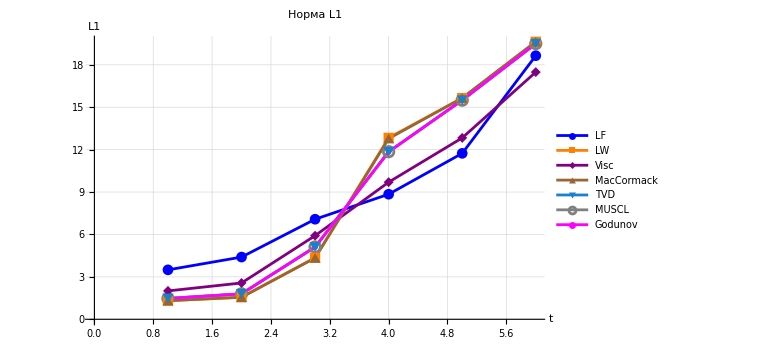

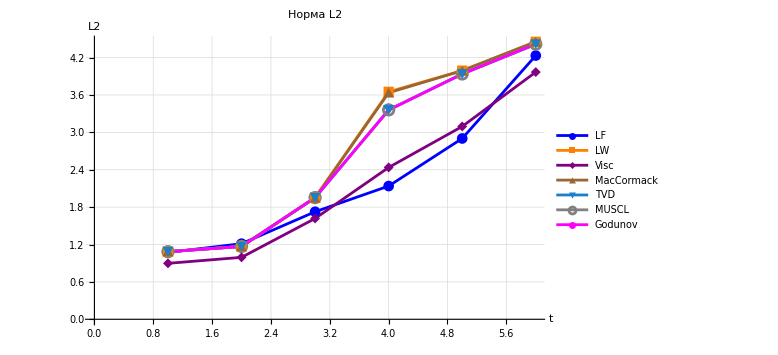

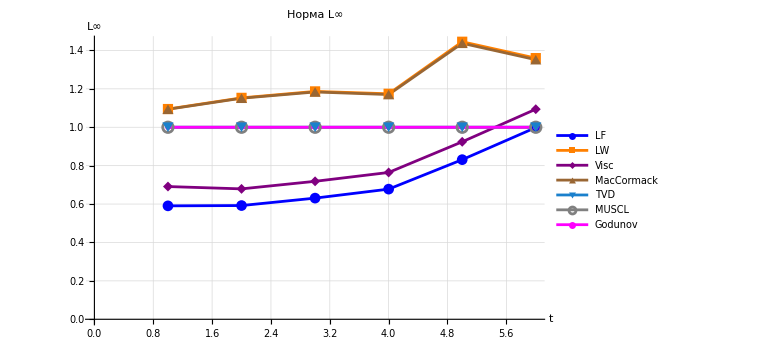

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

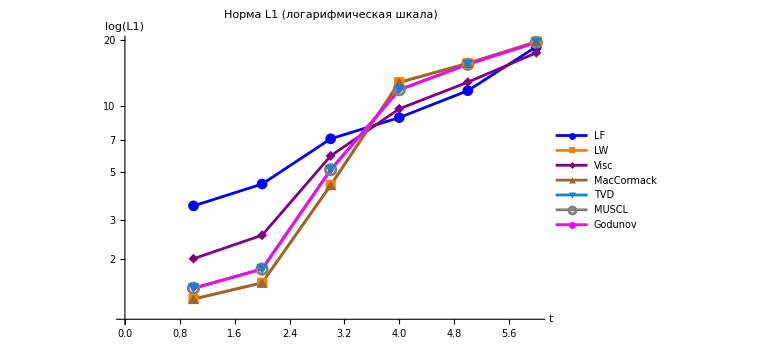

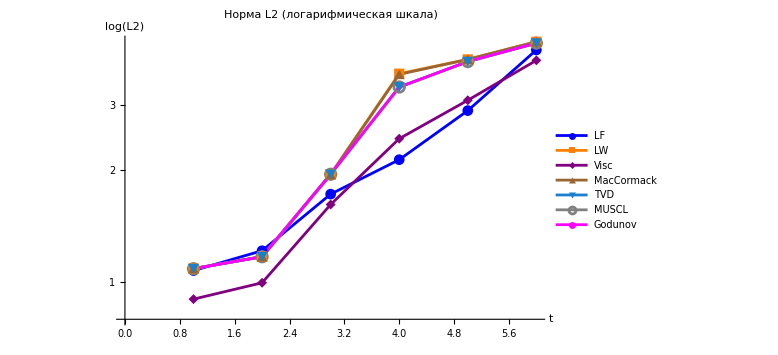

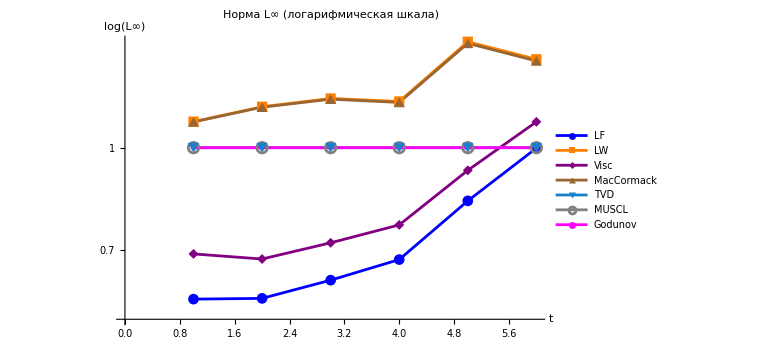

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=6"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 6",14],ImageSize->Large]
```

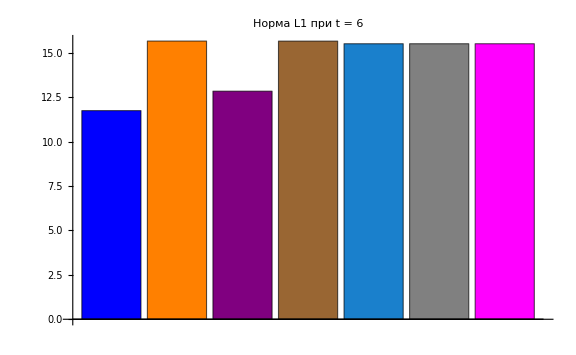

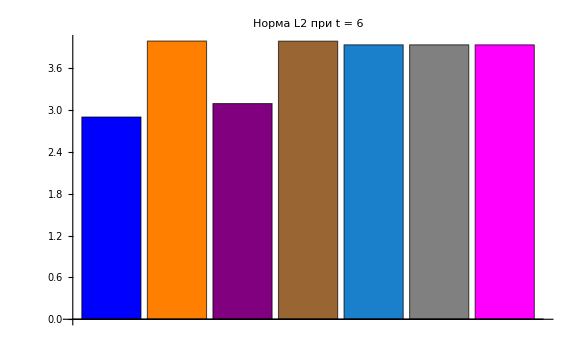

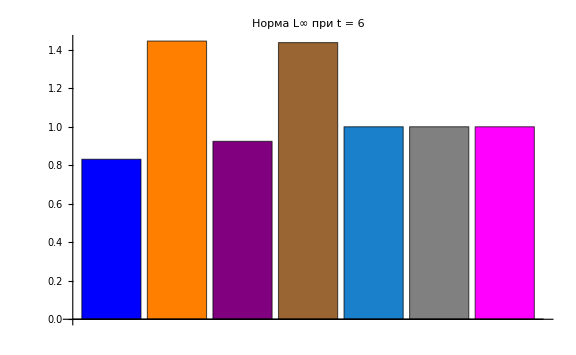

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
stepForFrames=5; 

activeSchemes={{uJavnmeth,Red},{uJavnLaxFrid,Blue},{uJavnLaxVander,Orange},(*{uJavnLax,Green},*){uJavnVisc,Purple},{uJavnMc,Brown},{uJavnTVD,RGBColor[0.1,0.5,0.8]},{uMUSCL,Gray},{uJavnRus,Cyan},{uJavnGod,Magenta},{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow}};

plotAt[n_]:=Module[{lines},lines=Map[Function[{dataCol},Module[{data=dataCol[[1]],col=dataCol[[2]],yvals},yvals=If[Head[data]===Function,data[n],data[[n]]];
Transpose[{xgrid,yvals}]]],activeSchemes];
ListLinePlot[lines,PlotStyle->activeSchemes[[All,2]],PlotRange->{{-xmax,xmax},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];


frames=Table[plotAt[n],{n,1,nstep,stepForFrames}];

Export["transport_schemes_a_x-t.gif",frames,"DisplayDurations"->0.03,"AnimationRepetitions"->Infinity];
(*Export["transport_schemes_a_x-t.mp4",frames,"FrameRate"->30];*)
```

```mathematica
(*При a=a(t)*)
ClearAll["Global`*"]
h=0.025;
tau=0.02;
xmax=3;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);
v[t_]:=(-1)^IntegerPart[t]
a[t_]:=Piecewise[{
{FractionalPart[t],EvenQ[IntegerPart[t]]},
{1-FractionalPart[t],OddQ[IntegerPart[t]]}
}]*)
a[t_]:=(-1)^IntegerPart[t]
fsol=NDSolve[{s'[t]==a[t],s[0]==0},s,{t,0,nstep*tau} ][[1]];

(*probfunc[x_]:=UnitStep[x]-UnitStep[x-1]+UnitStep[x-2]-UnitStep[x-3]+UnitStep[x-4]-UnitStep[x-5]*)
probfunc[x_]:=UnitStep[x]-UnitStep[x-1]

uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[x-(s[t]/. fsol)]

xgrid=Range[-xmax,xmax,h];
```

```mathematica
(*---Явная схема (против потока)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnmeth=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmeth[[1]]=probfunc/@xgrid;

Do[
Do[
ai=a[n*tau];
If[ai>0,uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(ai*tau/h) (uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]),uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(ai*tau/h) (uJavnmeth[[n,i+1]]-uJavnmeth[[n,i]])];,{i,2,Length[xgrid]-1}];
uJavnmeth[[n+1,1]]=uLeft[n*tau];
uJavnmeth[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Фридрихс)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxFrid=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxFrid[[1]]=probfunc/@xgrid;

Do[
Do[
ai=a[n*tau];
lambdaax=ai*tau/h;
uJavnLaxFrid[[n+1,i]]=1/2*(uJavnLaxFrid[[n,i+1]]+uJavnLaxFrid[[n,i-1]])-lambdaax/2*(uJavnLaxFrid[[n,i+1]]-uJavnLaxFrid[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxFrid[[n+1,1]]=uLeft[n*tau];
uJavnLaxFrid[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Вендрофф)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxVander=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxVander[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[n*tau];
lambdaax=a[n*tau]*tau/h;
uJavnLaxVander[[n+1,i]]=uJavnLaxVander[[n,i]]-lambdaax/2*(uJavnLaxVander[[n,i+1]]-uJavnLaxVander[[n,i-1]])+lambdaax^2/2*(uJavnLaxVander[[n,i+1]]-2*uJavnLaxVander[[n,i]]+uJavnLaxVander[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxVander[[n+1,1]]=uLeft[n*tau];
uJavnLaxVander[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Явная схема Лакса---*)
uJavnLax=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLax[[1]]=probfunc/@xgrid;

Do[
Do[
ai=a[n*tau];
uJavnLax[[n+1,i]]=(uJavnLax[[n,i+1]]+uJavnLax[[n,i-1]])/2-(tau/(2 h))*(ai*uJavnLax[[n,i+1]]-ai*uJavnLax[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLax[[n+1,1]]=uLeft[n*tau];
uJavnLax[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Центральная схема с модифицированной вязкостью---*)uJavnVisc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnVisc[[1]]=probfunc/@xgrid;

Do[Do[ai=a[n*tau];
central=-(tau/(2 h))*(ai*uJavnVisc[[n,i+1]]-ai*uJavnVisc[[n,i-1]]);
visc=(h^2/(2 tau))*(uJavnVisc[[n,i+1]]-2*uJavnVisc[[n,i]]+uJavnVisc[[n,i-1]]);
uJavnVisc[[n+1,i]]=uJavnVisc[[n,i]]+central+tau*visc;,{i,2,Length[xgrid]-1}];
uJavnVisc[[n+1,1]]=uLeft[n*tau];
uJavnVisc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Мак-Кормака---*)
uJavnMc=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnMc[[1]]=probfunc/@xgrid;
uStar=ConstantArray[0,Length[xgrid]];

Do[(*predictor*)Do[ai=a[n*tau];
uStar[[i]]=uJavnMc[[n,i]]-(tau/h)*(ai*uJavnMc[[n,i+1]]-ai*uJavnMc[[n,i]]);,{i,1,Length[xgrid]-1}];
(*corrector*)Do[ai=a[n*tau];
uJavnMc[[n+1,i]]=(uJavnMc[[n,i]]+uStar[[i]]-(tau/h)*(ai*uStar[[i]]-ai*uStar[[i-1]]))/2;,{i,2,Length[xgrid]-1}];
uJavnMc[[n+1,1]]=uLeft[n*tau];
uJavnMc[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Схема Русанова с учетом направления потока---*)
uJavnRus=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnRus[[1]]=probfunc/@xgrid;

Do[Do[ai=a[n*tau];
If[ai>0,fluxR=(ai*(uJavnRus[[n,i]]+uJavnRus[[n,i+1]])/2-ai*(uJavnRus[[n,i+1]]-uJavnRus[[n,i]])/2);
fluxL=(ai*(uJavnRus[[n,i-1]]+uJavnRus[[n,i]])/2-ai*(uJavnRus[[n,i]]-uJavnRus[[n,i-1]])/2);,fluxR=(ai*(uJavnRus[[n,i+1]]+uJavnRus[[n,i]])/2-ai*(uJavnRus[[n,i]]-uJavnRus[[n,i+1]])/2);
fluxL=(ai*(uJavnRus[[n,i]]+uJavnRus[[n,i-1]])/2-ai*(uJavnRus[[n,i-1]]-uJavnRus[[n,i]])/2);];
uJavnRus[[n+1,i]]=uJavnRus[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];
(*граничные условия*)uJavnRus[[n+1,1]]=uLeft[n*tau];
uJavnRus[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
(*---Схема Годунова---*)
uJavnGod=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnGod[[1]]=probfunc/@xgrid;

Do[Do[ai=a[n*tau];
fluxR=If[ai>0,ai*uJavnGod[[n,i]],ai*uJavnGod[[n,i+1]]];
fluxL=If[ai>0,ai*uJavnGod[[n,i-1]],ai*uJavnGod[[n,i]]];
uJavnGod[[n+1,i]]=uJavnGod[[n,i]]-(tau/h)*(fluxR-fluxL);,{i,2,Length[xgrid]-1}];
uJavnGod[[n+1,1]]=uLeft[n*tau];
uJavnGod[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (TVD) с учетом a>0 или a<0---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnTVD=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnTVD[[1]]=probfunc/@xgrid;

Do[Do[ai=a[n*tau];
lambdaax=Abs[ai]*tau/h;
If[ai>0,delm=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delp=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
delmleft=uJavnTVD[[n,i-1]]-uJavnTVD[[n,i-2]];
delpleft=delm;,delm=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
delp=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delmleft=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delpleft=delm;];
r=If[delp==0,0,delm/delp];
phi=Max[0,Min[1,r]];
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[1,rleft]];
correction=phi*delp-phileft*delm;
uJavnTVD[[n+1,i]]=uJavnTVD[[n,i]]-Sign[ai]*lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-2}];
uJavnTVD[[n+1,1]]=uLeft[n*tau];
uJavnTVD[[n+1,2]]=uJavnTVD[[n+1,3]];
uJavnTVD[[n+1,-2]]=uJavnTVD[[n+1,-3]];
uJavnTVD[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
(*---Явная схема (MUSCL)*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uMUSCL=ConstantArray[0,{1+nstep,Length[xgrid]}];
uMUSCL[[1]]=probfunc/@xgrid;

Do[
Do[
ai=a[n*tau];
lambdaax=Abs[ai]*tau/h;
If[
ai>0,
delm=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delp=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
delmleft=uMUSCL[[n,i-1]]-uMUSCL[[n,i-2]];
delpleft=delm;,

delm=uMUSCL[[n,i+1]]-uMUSCL[[n,i]];
delp=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delmleft=uMUSCL[[n,i]]-uMUSCL[[n,i-1]];
delpleft=delm;];

r=If[delp==0,0,delm/delp];
phi=Max[0,Min[2 r,1],Min[r,2]];
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[2 rleft,1],Min[rleft,2]];
correction=phi*delp-phileft*delm;
uMUSCL[[n+1,i]]=uMUSCL[[n,i]]-Sign[ai]*lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-2}];
uMUSCL[[n+1,1]]=uLeft[n*tau];
uMUSCL[[n+1,2]]=uMUSCL[[n+1,3]];
uMUSCL[[n+1,-2]]=uMUSCL[[n+1,-3]];
uMUSCL[[n+1,-1]]=uRight[n*tau];,{n,1,nstep}];
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[{If[showUpwind,Transpose[{xgrid,uJavnmeth[[n]]}],Nothing],If[showLF,Transpose[{xgrid,uJavnLaxFrid[[n]]}],Nothing],If[showLW,Transpose[{xgrid,uJavnLaxVander[[n]]}],Nothing],If[showLax,Transpose[{xgrid,uJavnLax[[n]]}],Nothing],If[showVisc,Transpose[{xgrid,uJavnVisc[[n]]}],Nothing],If[showMC,Transpose[{xgrid,uJavnMc[[n]]}],Nothing],If[showTVDmin,Transpose[{xgrid,uJavnTVD[[n]]}],Nothing],If[showMUSCL,Transpose[{xgrid,uMUSCL[[n]]}],Nothing],If[showRus,Transpose[{xgrid,uJavnRus[[n]]}],Nothing],If[showGod,Transpose[{xgrid,uJavnGod[[n]]}],Nothing],If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[{If[showUpwind,Red,Nothing],If[showLF,Blue,Nothing],If[showLW,Orange,Nothing],If[showLax,Green,Nothing],If[showVisc,Purple,Nothing],If[showMC,Brown,Nothing],If[showTVDmin,RGBColor[0.1,0.5,0.8],Nothing],If[showMUSCL,Gray,Nothing],If[showRus,Cyan,Nothing],If[showGod,Magenta,Nothing],If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep+1,1},Delimiter,{{showUpwind,True,Row[{Style["■",Red]," Явная схема (против потока)"}]},{True,False}},{{showLF,True,Row[{Style["■",Blue],"Явная схема (Лакса-Фридрихса)"}]},{True,False}},{{showLW,True,Row[{Style["■",Orange],"Явная схема (Лакса-Вендроффа)"}]},{True,False}},{{showLax,True,Row[{Style["■",Green],"Схема Лакса"}]},{True,False}},{{showVisc,True,Row[{Style["■",Purple],"Центральная с вязкостью"}]},{True,False}},{{showMC,True,Row[{Style["■",Brown],"Схема Мак-Кормака"}]},{True,False}},{{showTVDmin,True,Row[{Style["■",RGBColor[0.1,0.5,0.8]],"TVD minmod"}]},{True,False}},{{showMUSCL,True,Row[{Style["■",Gray],"MUSCL"}]},{True,False}},{{showRus,True,Row[{Style["■",Cyan],"Схема Русанова"}]},{True,False}},{{showGod,True,Row[{Style["■",Magenta],"Схема Годунова"}]},{True,False}},{{showExact,True,Row[{Style["■",Yellow],"Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-50,50},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax,"Масштаб X"},1,50},{{sy,0.6,"Масштаб Y"},0.1,2},TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showLF,showLW,showLax,showVisc,showMC,showTVDmin,showMUSCL,showRus,showGod,showExact}]
```

```mathematica
ClearAll[normL1,normL2,normLinf]
normL1[err_,h_]:=h Total[Abs[err]]
normL2[err_,h_]:=Sqrt[h Total[err^2]]
normLinf[err_]:=Max[Abs[err]]

t[n_]:=(n-1) tau;

nstep=Length[uJavnmeth];

timeIndices=<|"t=0.05"->2,"t=0.50"->11,"t=3.60"->73,"t=10.70"->215,"t=17"->341,"t=25"->501|>;

ClearAll[computeErrors]

computeErrors[uNum_,n_]:=Module[{uEx,err},uEx=uAnalytic[#,t[n]]&/@xgrid;
err=uNum-uEx;
{normL1[err,h],normL2[err,h],normLinf[err]}];

schemes=<|"Upwind"->uJavnmeth,"LF"->uJavnLaxFrid,"LW"->uJavnLaxVander,(*"Lax"->uJavnLax,*)"Visc"->uJavnVisc,"MacCormack"->uJavnMc,"TVD"->uJavnTVD,"MUSCL"->uMUSCL,"Rusanov"->uJavnRus,"Godunov"->uJavnGod|>;

errors=Association@Table[scheme->Association@Table[time->computeErrors[schemes[scheme][[timeIndices[time]]],timeIndices[time]],{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];

norms={"L1","L2","Linf"};
times={"t=0.05","t=0.50","t=3.60","t=10.70","t=17","t=25"};

rowForScheme[scheme_]:=Flatten@Table[errors[scheme][time][[norm]],{norm,3},{time,times}];

header1=Join[{""},Flatten@Table[ConstantArray[norm,6],{norm,norms}]];

header2=Join[{"Схема"},Flatten@Table[times,{Length[norms]}]];

tableData=Join[{header1,header2},Table[Prepend[rowForScheme[scheme],scheme],{scheme,Keys[errors]}]];

Grid[tableData,Frame->All,Alignment->Center,ItemStyle->Directive[14],Background->{None,{LightGray,None}}]
```

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | Linf | Linf | Linf | Linf | Linf | Linf
Схема | t=0.05 | t=0.50 | t=3.60 | t=10.70 | t=17 | t=25 | t=0.05 | t=0.50 | t=3.60 | t=10.70 | t=17 | t=25 | t=0.05 | t=0.50 | t=3.60 | t=10.70 | t=17 | t=25
Upwind | 0.4 | 0.482711 | 1.16979 | 1.47395 | 1.57757 | 1.65275 | 0.565685 | 0.37278 | 0.696666 | 0.814462 | 0.853717 | 0.882057 | 0.8 | 0.382179 | 0.638363 | 0.743067 | 0.793021 | 0.831953
LF | 0.4 | 1.08271 | 1.62432 | 1.76488 | 1.75954 | 1.70481 | 0.4 | 0.652439 | 0.871133 | 0.926035 | 0.940775 | 0.950184 | 0.4 | 0.548519 | 0.814239 | 0.890327 | 0.912176 | 0.928608
LW | 0.48 | 0.56064 | 0.542626 | 0.530269 | 0.65487 | 0.959645 | 0.62482 | 0.412724 | 0.516228 | 0.39885 | 0.468672 | 0.688691 | 0.88 | 0.47882 | 0.690344 | 0.512462 | 0.591969 | 0.76734
Visc | 0.46875 | 0.479778 | 0.644031 | 0.882752 | 1.04636 | 1.22291 | 0.61622 | 0.372074 | 0.514757 | 0.567228 | 0.64316 | 0.731965 | 0.86875 | 0.440214 | 0.616582 | 0.513108 | 0.579906 | 0.682846
MacCormack | 0.48 | 0.56064 | 0.542626 | 0.530269 | 0.65487 | 0.959645 | 0.62482 | 0.412724 | 0.516228 | 0.39885 | 0.468672 | 0.688691 | 0.88 | 0.47882 | 0.690344 | 0.512462 | 0.591969 | 0.76734
TVD | 0.4 | 0.336618 | 1.0231 | 1.33678 | 1.45557 | 1.5471 | 0.565685 | 0.284989 | 0.63459 | 0.762251 | 0.808939 | 0.844535 | 0.8 | 0.288568 | 0.586125 | 0.674582 | 0.732632 | 0.781677
MUSCL | 0.4 | 0.253035 | 0.944024 | 1.2671 | 1.39859 | 1.50334 | 0.565685 | 0.236268 | 0.602612 | 0.734399 | 0.786738 | 0.828258 | 0.8 | 0.239902 | 0.559756 | 0.639904 | 0.704206 | 0.763049
Rusanov | 0.4 | 0.482711 | 1.16979 | 1.47395 | 1.57757 | 1.65275 | 0.565685 | 0.37278 | 0.696666 | 0.814462 | 0.853717 | 0.882057 | 0.8 | 0.382179 | 0.638363 | 0.743067 | 0.793021 | 0.831953
Godunov | 0.4 | 0.482711 | 1.16979 | 1.47395 | 1.57757 | 1.65275 | 0.565685 | 0.37278 | 0.696666 | 0.814462 | 0.853717 | 0.882057 | 0.8 | 0.382179 | 0.638363 | 0.743067 | 0.793021 | 0.831953

```mathematica
schemeColors=<|"Upwind"->Red,"LF"->Blue,"LW"->Orange,"Visc"->Purple,"MacCormack"->Brown,"TVD"->RGBColor[0.1,0.5,0.8],"MUSCL"->Gray,"Rusanov"->Cyan,"Godunov"->Magenta|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

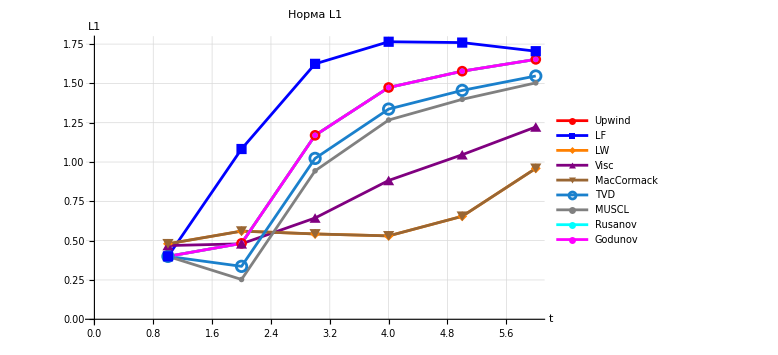

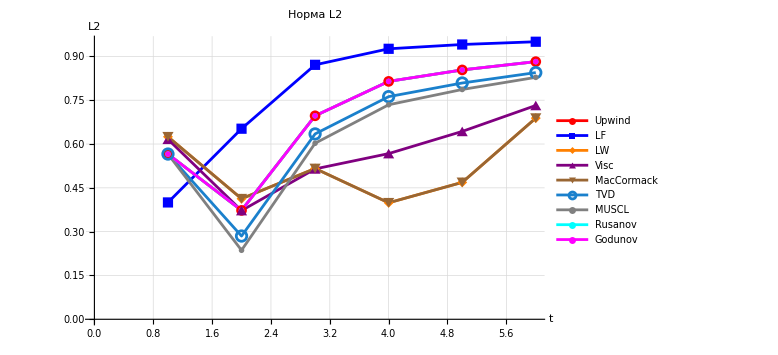

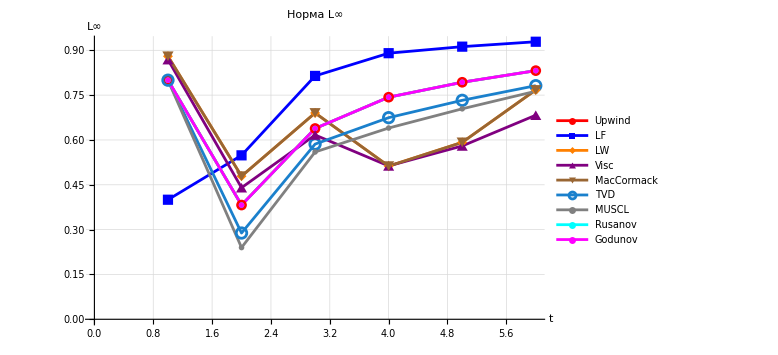

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

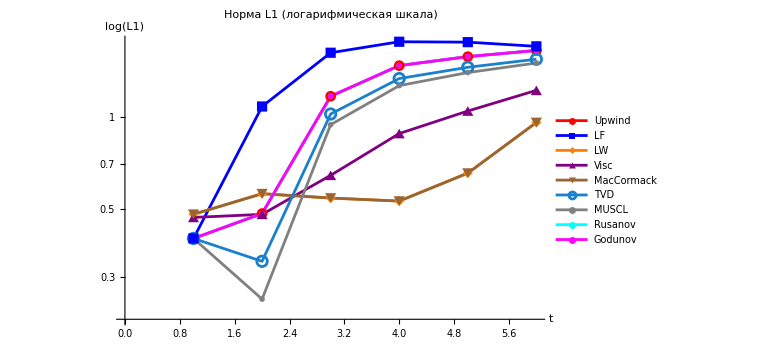

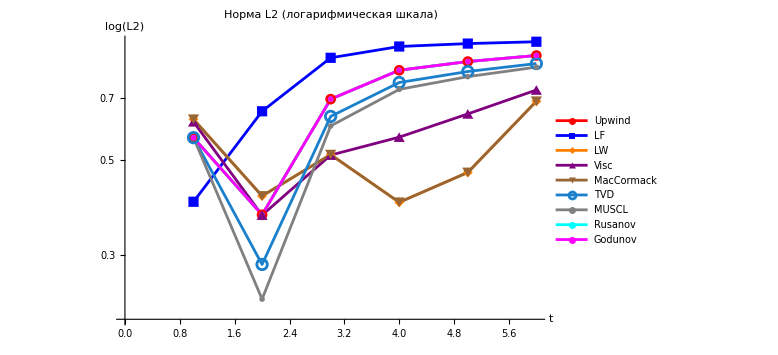

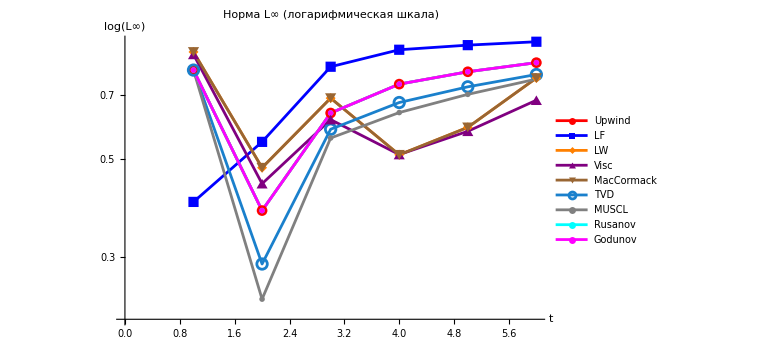

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=3.60"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 3.60",14],ImageSize->Large]
```

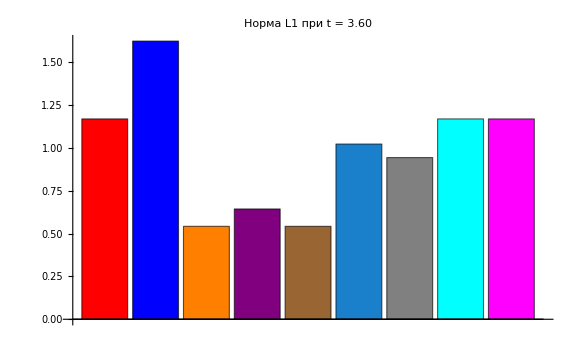

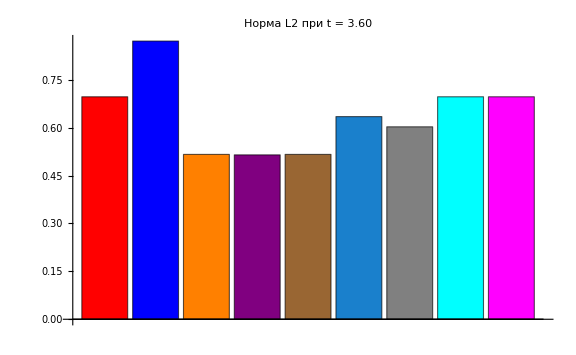

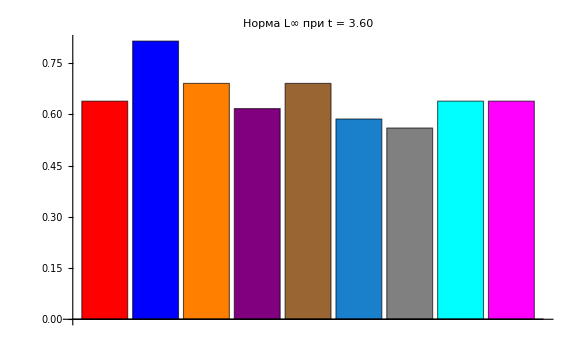

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
stepForFrames=5;

activeSchemes={{uJavnmeth,Red},{uJavnLaxFrid,Blue},{uJavnLaxVander,Orange},(*{uJavnLax,Green},*){uJavnVisc,Purple},{uJavnMc,Brown},{uJavnTVD,RGBColor[0.1,0.5,0.8]},{uMUSCL,Gray},{uJavnRus,Cyan},{uJavnGod,Magenta},{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow}};


plotAt[n_]:=Module[{lines},lines=Map[Function[{dataCol},Module[{data=dataCol[[1]],col=dataCol[[2]],yvals},yvals=If[Head[data]===Function,data[n],data[[n]]];
Transpose[{xgrid,yvals}]]],activeSchemes];
ListLinePlot[lines,PlotStyle->activeSchemes[[All,2]],PlotRange->{{-2,10},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];

frames=Table[plotAt[n],{n,1,nstep,stepForFrames}];


Export["transport_schemes_javn_a(t).gif",frames,"DisplayDurations"->0.08,"AnimationRepetitions"->Infinity];
(*Export["transport_schemes_javn_a(t).mp4",frames,"FrameRate"->30];*)
```

```mathematica
(*a=const*)
ClearAll["Global`*"]
a=1;
h=0.25;
tau=0.5;
lambda=a*tau/h;
xmax=280;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)
probfunc[x_]:=UnitStep[x]
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[x-a t];
xgrid=Range[-xmax,xmax,h];
len=Length[xgrid];
```

```mathematica
(*Неявная схема против потока*)
A=SparseArray[{
Band[{1,1}]->(1+lambda),
Band[{2,1}]->-lambda},
{len,len}];

uImplicit=ConstantArray[0,{nstep,len}];
uImplicit[[1]]=probfunc/@xgrid;

Do[uImplicit[[n+1]]=LinearSolve[A,uImplicit[[n]]],{n,1,nstep-1}];
```

```mathematica
(*Неявная центральная схема*)
Agen=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->-lambda/2,
Band[{1,2}]->lambda/2},
{len,len}];

uImplicitgen=ConstantArray[0,{nstep,len}];
uImplicitgen[[1]]=probfunc/@xgrid;

Do[uImplicitgen[[n+1]]=LinearSolve[Agen,uImplicitgen[[n]]],{n,1,nstep-1}];
```

```mathematica
(*Неявная схема Лакса-Вендроффа*)
ALW=SparseArray[{
Band[{1,2}]->lambda/2-(lambda^2)/2,
Band[{1,1}]->1+lambda^2,
Band[{2,1}]->-lambda/2-(lambda^2)/2},
{len,len}];

uImplicitlaksven=ConstantArray[0,{nstep,len}];
uImplicitlaksven[[1]]=probfunc/@xgrid;

Do[
uImplicitlaksven[[n+1]]=LinearSolve[ALW,uImplicitlaksven[[n]]]
,{n,1,nstep-1}];
```

```mathematica
(*Неявная схема Кранк-Николсон*)
ACN=SparseArray[{
Band[{1,1}]->(1+lambda/2),
Band[{2,1}]->(-lambda/2)},
{len,len}];

uImplicitkraknic=ConstantArray[0,{nstep,len}];
uImplicitkraknic[[1]]=probfunc/@xgrid;
Do[
rhs=ConstantArray[0,len];
rhs[[1]]=uImplicitkraknic[[n,1]];rhs[[2;;]]=(1-lambda/2) uImplicitkraknic[[n,2;;]]+(lambda/2) uImplicitkraknic[[n,1;;-2]];
uImplicitkraknic[[n+1]]=LinearSolve[ACN,rhs]
,{n,1,nstep-1}]
```

```mathematica
(*Неявная апвинд (3.17)*)
alpha=UnitStep[-lambda];  (*a<0*)
beta=UnitStep[lambda];  (*a>0*)

lowerdig=-beta*lambda;
upperdig=alpha*lambda;
generaldig=1+Abs[lambda];
ALW=SparseArray[{
Band[{1,2}]->upperdig,
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig},
{len,len}];

uImplicitupwid=ConstantArray[0,{nstep,len}];
uImplicitupwid[[1]]=probfunc/@xgrid;
Do[
uImplicitupwid[[n+1]]=LinearSolve[ALW,uImplicitupwid[[n]]];
If[lambda>0,uImplicitupwid[[n+1,1]]=uAnalytic[-xmax,n tau],uImplicitupwid[[n+1,-1]]=uAnalytic[xmax,n tau]];
,{n,1,nstep-1}];
```

```mathematica
(*Линейная вязкость (3.20)*)
omega=0.2;
upper=lambda/2-omega;
lower=-lambda/2-omega;
diag=1+2*omega;

A320=SparseArray[{
Band[{1,1}]->diag,
Band[{1,2}]->upper,
Band[{2,1}]->lower}
,{len,len}];
u320=ConstantArray[0,{nstep,len}];
u320[[1]]=probfunc/@xgrid;

Do[u320[[n+1]]=LinearSolve[A320,u320[[n]]];
u320[[n+1,1]]=uAnalytic[-xmax,n tau];
,{n,1,nstep-1}]
```

```mathematica
(*Вязкость 4-го порядка (3.18)*)
omega=0.3;
lambda=a tau/h;

D4=SparseArray[{
Band[{1,1}]->6 omega/8+1,
Band[{1,2}]->-4 omega/8+lambda/2,
Band[{1,3}]->omega/8,
Band[{2,1}]->-4 omega/8-lambda/2,
Band[{3,1}]->omega/8}
,{len,len}];

A318=D4;

u318=ConstantArray[0,{nstep,len}];
u318[[1]]=probfunc/@xgrid;

Do[u318[[n+1]]=LinearSolve[A318,u318[[n]]];
u318[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Регуляриз.Лакс-Вендрофф (3.19)*)
coef=tau a^2/(2 h^2); 
upperLW=lambda/2-coef;
lowerLW=-lambda/2-coef;
diagLW=1+2 coef;
A319=SparseArray[{
Band[{1,1}]->diagLW,
Band[{1,2}]->upperLW,
Band[{2,1}]->lowerLW}
,{len,len}];

u319=ConstantArray[0,{nstep,len}];
u319[[1]]=probfunc/@xgrid;

Do[u319[[n+1]]=LinearSolve[A319,u319[[n]]];
u319[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Нелинейная вязкость (3.21)*)
omega=0.1;
lambda=a tau/h;      (*переноса*)
coef=omega tau^2 a^2/h^2;  (*искусственная вязкость*)

upper=lambda/2-coef;
lower=-lambda/2-coef;
diag=1+2 coef;

A321=SparseArray[{Band[{1,1}]->diag,Band[{1,2}]->upper,Band[{2,1}]->lower},{len,len}];

u321=ConstantArray[0,{nstep,len}];
u321[[1]]=probfunc/@xgrid;

Do[u321[[n+1]]=LinearSolve[A321,u321[[n]]];
u321[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*параметры*)lambdaGrid=a*tau/h;len=Length[xgrid];(*коэффициенты схемы (3.15)*)diag315=1+lambdaGrid/2;lower315=-3 lambdaGrid/4;upper315=lambdaGrid/4;A315=SparseArray[{Band[{1,1}]->diag315,Band[{2,1}]->lower315,Band[{1,2}]->upper315},{len,len}];u315=ConstantArray[0,{nstep,len}];u315[[1]]=probfunc/@xgrid;Do[u315[[n+1]]=LinearSolve[A315,u315[[n]]];u315[[n+1,1]]=uAnalytic[-xmax,n*tau];,{n,1,nstep-1}];
```

```mathematica
(*параметры*)lambdaGrid=a*tau/h;
len=Length[xgrid];

(*матрица схемы (3.16)*)
diag316=1+lambdaGrid/2;
lower316=-lambdaGrid/2;

A316=SparseArray[{Band[{1,1}]->diag316,Band[{2,1}]->lower316},{len,len}];

(*решение*)
u316=ConstantArray[0,{nstep,len}];
u316[[1]]=probfunc/@xgrid;

Do[rhs=ConstantArray[0,len];
rhs[[1;;-2]]=(1+lambdaGrid/2) u316[[n,1;;-2]]-(lambdaGrid/2) u316[[n,2;;]];
rhs[[-1]]=u316[[n,-1]];(*граничное*)u316[[n+1]]=LinearSolve[A316,rhs];
u316[[n+1,1]]=uAnalytic[-xmax,n*tau];,{n,1,nstep-1}];
```

```mathematica
(*Неявная схема Годунова*)
lambda=(tau/h)*a;

Agod=SparseArray[{
Band[{1,1}]->1+lambda,
Band[{2,1}]->-lambda}
,{len,len}];

uImplicitGod=ConstantArray[0,{nstep,len}];
uImplicitGod[[1]]=probfunc/@xgrid;
Do[
uImplicitGod[[n+1]]=LinearSolve[Agod,uImplicitGod[[n]]];
uImplicitGod[[n+1,1]]=uAnalytic[-xmax,n*tau];
,{n,1,nstep-1}];
```

```mathematica
Manipulate[ListLinePlot[{
Transpose[{xgrid,uImplicit[[n]]}],
Transpose[{xgrid,uImplicitgen[[n]]}],
Transpose[{xgrid,uImplicitlaksven[[n]]}],
Transpose[{xgrid,uImplicitkraknic[[n]]}],
Transpose[{xgrid,uImplicitupwid[[n]]}],
Transpose[{xgrid,u320[[n]]}],
Transpose[{xgrid,u318[[n]]}],
Transpose[{xgrid,u321[[n]]}],
Transpose[{xgrid,u319[[n]]}],
(*Transpose[{xgrid,u[[n]]}],*)
(*Transpose[{xgrid,uImplicitMUSCL[[n]]}],*)
Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->All,PlotStyle->{Red,Blue, Orange,Green, White, Yellow,Purple,Brown},PlotLegends->{
"Неявная против потока (3.14)",
"Неявная Лакс–Вендроффа (3.19)",
"Кранк–Николсон (3.15)",
"Неявная апвинд (3.17)",
"Линейная вязкость (3.20)",
"Вязкость 4-го порядка (3.18)",
"Нелинейная вязкость (3.21)",
"Регуляриз. Лакс–Вендрофф (3.19)",
(*"TVD",*)
(*"MUSCL",*)
"Аналитическое решение"},GridLines->Automatic],{n,1,nstep,1}]
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[
{If[showUpwind,Transpose[{xgrid,uImplicit[[n]]}],Nothing],
If[showGen,Transpose[{xgrid,uImplicitgen[[n]]}],Nothing],
If[showLaxVen,Transpose[{xgrid,uImplicitlaksven[[n]]}],Nothing],
If[showCrank,Transpose[{xgrid,uImplicitkraknic[[n]]}],Nothing],
If[showUpwid,Transpose[{xgrid,uImplicitupwid[[n]]}],Nothing],
If[show320,Transpose[{xgrid,u320[[n]]}],Nothing],
If[show318,Transpose[{xgrid,u318[[n]]}],Nothing],
If[show321,Transpose[{xgrid,u321[[n]]}],Nothing],
If[show319,Transpose[{xgrid,u319[[n]]}],Nothing],
If[show315,Transpose[{xgrid,u315[[n]]}],Nothing],
If[show316,Transpose[{xgrid,u316[[n]]}],Nothing],
If[godun,Transpose[{xgrid,uImplicitGod[[n]]}],Nothing],
(*If[TVD,Transpose[{xgrid,u[[n]]}],Nothing],
If[MUSCL,Transpose[{xgrid,uImplicitMUSCL[[n]]}],Nothing],*)
If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[
{If[showUpwind,Red,Nothing],
If[showGen,RGBColor[0.1,0.5,0.8],Nothing],
If[showLaxVen,Magenta,Nothing],
If[showCrank,Orange,Nothing],
If[showUpwid,Green,Nothing],
If[show320,Brown,Nothing],
If[show318,Cyan,Nothing],
If[show321,Purple,Nothing],
If[show319,Brown,Nothing],
If[show315,Gray,Nothing],
If[show316,Black,Nothing],
If[godun,Blue,Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1},Delimiter,{{showUpwind,True,Row[{Style["■",Red]," Неявная против потока (3.14)"}]},{True,False}},{{showGen,False,Row[{Style["■",RGBColor[0.1,0.5,0.8]]," Неявная gen"}]},{True,False}},{{showLaxVen,True,Row[{Style["■",Magenta]," Неявная Лакс-Вендроффа (3.19)"}]},{True,False}},{{showCrank,True,Row[{Style["■",Orange]," Кранк-Николсон (3.15)"}]},{True,False}},{{showUpwid,True,Row[{Style["■",Green]," Неявная апвинд (3.17)"}]},{True,False}},{{show320,False,Row[{Style["■",Brown]," Линейная вязкость (3.20)"}]},{True,False}},{{show318,False,Row[{Style["■",Cyan]," Вязкость 4-го порядка (3.18)"}]},{True,False}},{{show321,True,Row[{Style["■",Purple]," Нелинейная вязкость (3.21)"}]},{True,False}},
{{show315,True,Row[{Style["■",Gray]," (3.15)"}]},{True,False}},
{{godun,True,Row[{Style["■",Blue]," Годунов"}]},{True,False}},
{{show316,True,Row[{Style["■",Black]," (3.16)"}]},{True,False}},{{show319,True,Row[{Style["■",Brown]," Регуляриз. Лакс-Вендрофф (3.19)"}]},{True,False}},

(*{{TVD,True,Row[{Style["■",Black]," TVD"}]},{True,False}},

{{MUSCL,True,Row[{Style["■",Gray]," MUSCL"}]},{True,False}},*)
{{showExact,True,Row[{Style["■",Yellow]," Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-xmax,xmax},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax,"Масштаб X"},1,xmax},{{sy,0.6,"Масштаб Y"},0.1,2},TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showGen,showLaxVen,showCrank,showUpwid,show320,show318,show321,show319,show315,show316,showExact}]
```

```mathematica
uAnalyticGrid[t_]:=uAnalytic[#,t]&/@xgrid;

ClearAll[normL1,normL2,normLinf];
normL1[err_]:=h Total[Abs[err]];
normL2[err_]:=Sqrt[h Total[err^2]];
normLinf[err_]:=Max[Abs[err]];

timeIndices=<|"t=20"->40,"t=50"->101,"t=100"->201,"t=150"->301,"t=200"->401,"t=250"->500|>;


computeNorms[uNum_,k_]:=Module[
{t,err},t=(k-1) tau;
err=uNum[[k]]-uAnalyticGrid[t];
{normL1[err],normL2[err],normLinf[err]}];


schemes=<|
"Против потока "->uImplicit,
(*"Центральная "->uImplicitgen,*)
"ЛВ"->uImplicitlaksven,
"КН"->uImplicitkraknic,
"Общая пртв птк"->uImplicitupwid,
"Лин. вязкость"->u320,
"Вяз. 4-го поряд. "->u318,
"Нелин. вязкость"->u321,
"Годунов "->uImplicitGod|>;

errors=Association@Table[
scheme->Association@Table[
time->computeNorms[schemes[scheme],timeIndices[time]]
,{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];


norms={"L1","L2","L∞"};
times={"t=20","t=50","t=100","t=150","t=200","t=250"};

header1=Join[{""},Flatten@Table[ConstantArray[Style[norm,Bold],Length[times]],{norm,norms}]];

header2=Join[{Style["Схема",Bold]},Flatten@Table[times,{Length[norms]}]];


rowForScheme[scheme_]:=Prepend[Flatten@Table[errors[scheme][time][[i]],{i,3},{time,times}],Style[scheme,Bold]];

tableData=Join[{header1,header2},rowForScheme/@Keys[errors]];

Grid[tableData,Frame->All,Alignment->Center,Spacings->{1.4,1.2},ItemStyle->Directive[14],Background->{None,{Lighter[Gray,.9],LightGray,None}},Dividers->{{False,True},{False,True,False}}]
```

General::munfl: (1.41742×10^-191)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.79396×10^-189)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.09025×10^-187)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | L∞ | L∞ | L∞ | L∞ | L∞ | L∞
Схема | t=20 | t=50 | t=100 | t=150 | t=200 | t=250 | t=20 | t=50 | t=100 | t=150 | t=200 | t=250 | t=20 | t=50 | t=100 | t=150 | t=200 | t=250
Против потока  | 3.04372 | 4.88128 | 6.90652 | 8.4601 | 9.76968 | 10.8384 | 0.945305 | 1.19625 | 1.42261 | 1.57438 | 1.69178 | 1.7878 | 0.508704 | 0.505432 | 0.50384 | 0.503135 | 0.502715 | 0.502431
ЛВ | 3.63947 | 5.76133 | 8.09991 | 9.89384 | 11.406 | 12.5416 | 1.03055 | 1.2973 | 1.53873 | 1.70088 | 1.82643 | 1.93003 | 0.508484 | 0.505293 | 0.503741 | 0.503054 | 0.502645 | 0.502368
КН | 1.75604 | 2.81742 | 3.98693 | 4.88399 | 5.64013 | 6.2997 | 0.717874 | 0.908752 | 1.08083 | 1.19618 | 1.28541 | 1.35849 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5
Общая пртв птк | 3.04372 | 4.88128 | 6.90652 | 8.4601 | 9.76968 | 10.8384 | 0.945305 | 1.19625 | 1.42261 | 1.57438 | 1.69178 | 1.7878 | 0.508704 | 0.505432 | 0.50384 | 0.503135 | 0.502715 | 0.502431
Лин. вязкость | 3.10633 | 4.67998 | 6.41432 | 7.74474 | 8.8662 | 9.79175 | 0.982777 | 1.19408 | 1.39045 | 1.52408 | 1.62824 | 1.71306 | 0.666667 | 0.666667 | 0.666667 | 0.666667 | 0.666667 | 0.657465
Вяз. 4-го поряд.  | 3.25 | 4.7504 | 6.40403 | 7.67253 | 8.7418 | 9.62529 | 1.04359 | 1.23595 | 1.41826 | 1.54363 | 1.6419 | 1.72211 | 0.81128 | 0.81128 | 0.81128 | 0.81128 | 0.81128 | 0.804207
Нелин. вязкость | 2.90981 | 4.5534 | 6.36485 | 7.75441 | 8.92574 | 9.8995 | 0.925211 | 1.15607 | 1.36624 | 1.50779 | 1.61752 | 1.70694 | 0.508518 | 0.505314 | 0.503757 | 0.503067 | 0.502656 | 0.502378
Годунов  | 3.04372 | 4.88128 | 6.90652 | 8.4601 | 9.76968 | 10.8384 | 0.945305 | 1.19625 | 1.42261 | 1.57438 | 1.69178 | 1.7878 | 0.508704 | 0.505432 | 0.50384 | 0.503135 | 0.502715 | 0.502431

```mathematica
schemeColors=<|"Против потока "->Red,"Центральная "->RGBColor[0.1,0.5,0.8],"ЛВ"->Magenta,"КН"->Orange,"Общая пртв птк"->Green,"Лин. вязкость"->Brown,"Вяз. 4-го поряд. "->Cyan,"Нелин. вязкость"->Purple,"Годунов "->Blue|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

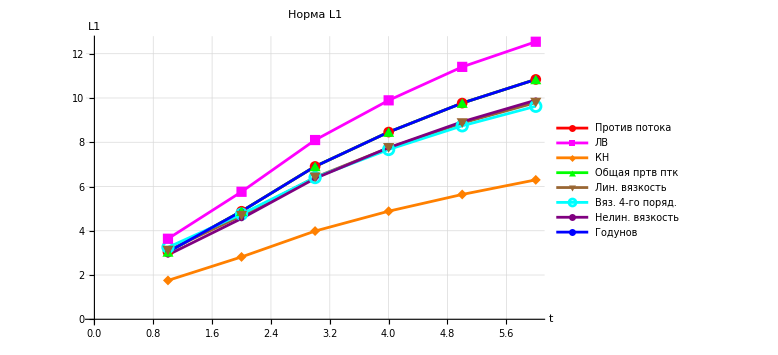

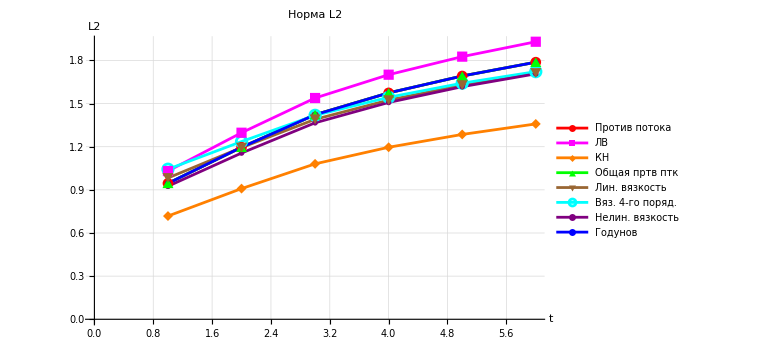

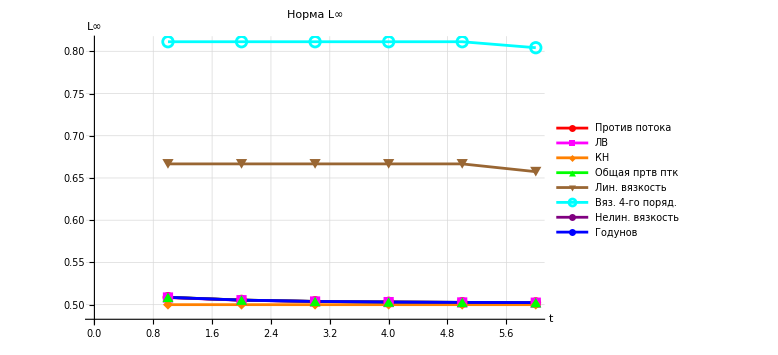

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

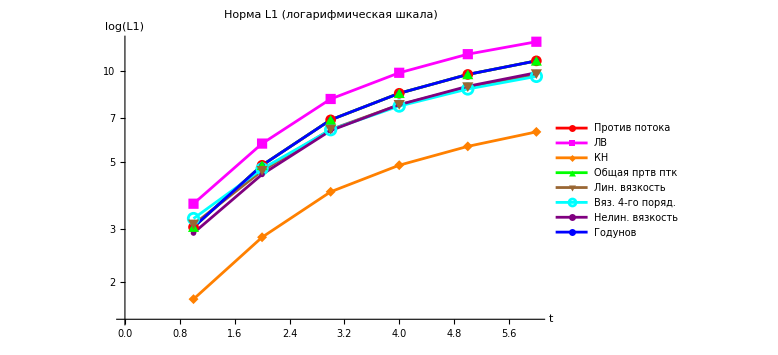

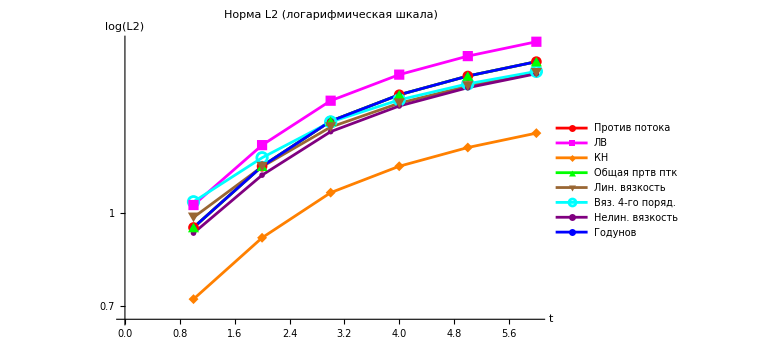

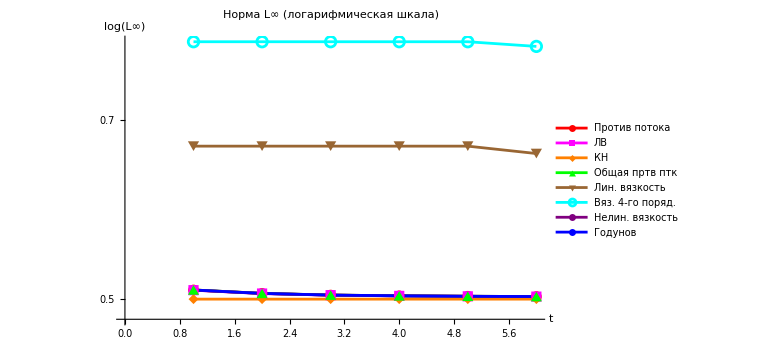

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=250"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 250",14],ImageSize->Large]
```

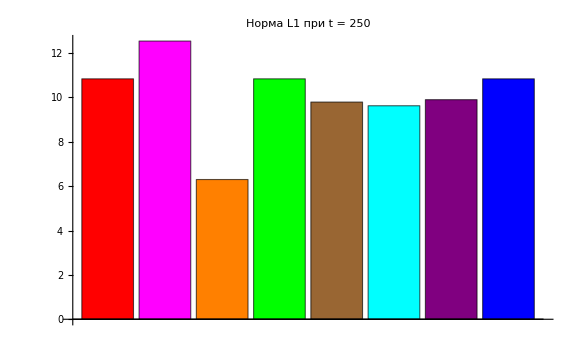

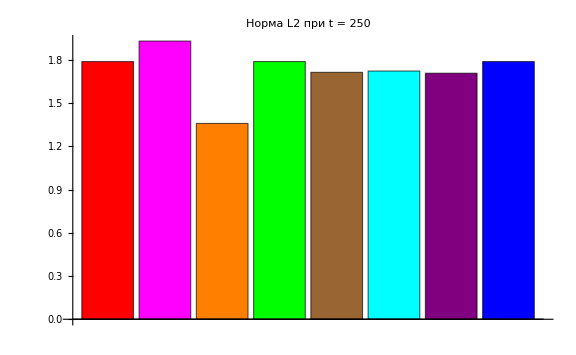

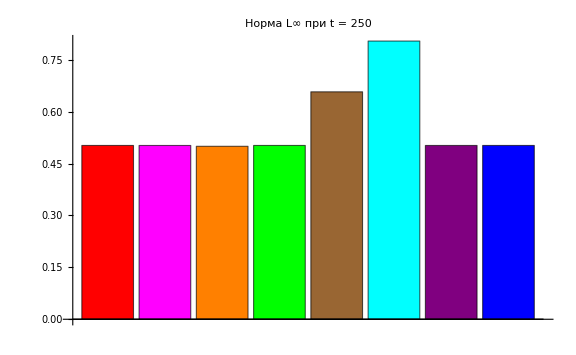

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
schemeNames=<|"Неявная против потока (3.14)"->{uImplicit,Red,True},"Неявная gen"->{uImplicitgen,Blue,False},"Неявная Лакс-Вендроффа (3.19)"->{uImplicitlaksven,Magenta,True},"Кранк-Николсон (3.15)"->{uImplicitkraknic,Orange,True},"Неявная апвинд (3.17)"->{uImplicitupwid,Green,True},"Линейная вязкость (3.20)"->{u320,White,True},"Вязкость 4-го порядка (3.18)"->{u318,Cyan,True},"Нелинейная вязкость (3.21)"->{u321,Purple,True},"Регуляриз. Лакс-Вендрофф (3.19)"->{u319,Brown,True},"Аналитическое решение"->{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow,True}|>;
follow=True;  (*False—весь диапазон*)
xWindow=40;   (*половина ширины окна*)

plotAt[n_]:=
Module[
{lines={},colors={},data,col,flag,yvals},
Do[
{data,col,flag}=schemeNames[name];
If[flag,yvals=If[Head[data]===Function,data[n],data[[n]]];
If[Length[yvals]===Length[xgrid],AppendTo[lines,Transpose[{xgrid,yvals}]];
AppendTo[colors,col]]],{name,Keys[schemeNames]}];
ListLinePlot[lines,PlotStyle->colors,PlotRange->{{130,200},{-0.1,1.2}},
GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];

stepForFrames=1; 
frameIndices=Range[1,nstep,stepForFrames];

frames=Table[plotAt[n],{n,frameIndices}];

Export["transport_schemes_nejavn_a_const.gif",frames,"DisplayDurations"->0.02,"AnimationRepetitions"->Infinity];

(*Export["ttransport_schemes_nejavn_a_const.mp4",frames,"FrameRate"->15];*)
```

```mathematica
(*Функция построения графика для заданного шага n*)plotImplicitAtTime[n_]:=ListLinePlot[DeleteCases[{If[showUpwind,Transpose[{xgrid,uImplicit[[n]]}],Nothing],If[showGen,Transpose[{xgrid,uImplicitgen[[n]]}],Nothing],If[showLaxVen,Transpose[{xgrid,uImplicitlaksven[[n]]}],Nothing],If[showCrank,Transpose[{xgrid,uImplicitkraknic[[n]]}],Nothing],If[showUpwid,Transpose[{xgrid,uImplicitupwid[[n]]}],Nothing],If[show320,Transpose[{xgrid,u320[[n]]}],Nothing],If[show318,Transpose[{xgrid,u318[[n]]}],Nothing],If[show321,Transpose[{xgrid,u321[[n]]}],Nothing],If[godun,Transpose[{xgrid,uImplicitGod[[n]]}],Nothing],If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[{If[showUpwind,Red,Nothing],If[showGen,RGBColor[0.1,0.5,0.8],Nothing],If[showLaxVen,Magenta,Nothing],If[showCrank,Orange,Nothing],If[showUpwid,Green,Nothing],If[show320,Brown,Nothing],If[show318,Cyan,Nothing],If[show321,Purple,Nothing],If[godun,Blue,Nothing],If[showExact,Yellow,Nothing]},Nothing],PlotLegends->Placed[LineLegend[DeleteCases[{If[showUpwind,"3.1 Неявная схема против потока",Nothing],If[showGen,"3.2 Неявная центральная схема",Nothing],If[showLaxVen,"3.3 Неявная Лакс-Вендроффа",Nothing],If[showCrank,"3.4 Кранк-Николсон",Nothing],If[showUpwid,"3.5 Общая неявная противопоточная схема",Nothing],If[show320,"3.6 Схема с линейной вязкостью",Nothing],If[show318,"3.7 Схема с вязкостью 4-го порядка",Nothing],If[show321,"3.8 Схема с нелинейной вязкостью",Nothing],
If[godun,"3.9 Схема Годунова",Nothing],If[showExact,"Аналитическое решение",Nothing]},Nothing]],Right],PlotRange->{{x0-sx,x0+sx},{y0-sy,y0+sy}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]];

(*Параметры видимости*)
x0=4.2;y0=0.5;sx=3.9;sy=0.555;
showUpwind=showGen=showLaxVen=showCrank=True;
showUpwid=show320=show318=show321=show319=show315=show316=True;
godun=True;showExact=True;

(*Экспорт в PDF для шага n=70*)
Export["implicit_schemes_t70.pdf",plotImplicitAtTime[70]];
```

```mathematica
(*a=a(x)*)
ClearAll["Global`*"]
h=0.25;
tau=0.5;
lambda=a*tau/h;
xmax=280;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)
a[x_]:=1+0.5 Sin[x];
probfunc[x_]:=UnitStep[x]
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-xmax,xmax}][[1]];
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[-t+(f[x]/. fsol)];
xgrid=Range[-xmax,xmax,h];
len=Length[xgrid];
aGrid = a/@xgrid;
lambdaGrid=aGrid*tau/h;
```

```mathematica
(*Неявная схема против потока*)
epsilon=0.02;
generaldig=1+lambdaGrid+2 epsilon;
lowerdig=-lambdaGrid[[2;;]]-epsilon;
upperdig=-epsilon;

A=SparseArray[{
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig,
Band[{1,2}]->upperdig},
{len,len}];

uImplicit=ConstantArray[0,{nstep,len}];
uImplicit[[1]]=probfunc/@xgrid;
Do[
uImplicit[[n+1]]=LinearSolve[A,uImplicit[[n]]];
uImplicit[[n+1,1]]=uAnalytic[-xmax,n*tau];
,{n,1,nstep-1}];
```

```mathematica
(*Неявная центральная схема*)
upperdig=lambdaGrid[[1;;-2]]/2;
generaldig=1;
lowerdig=-lambdaGrid[[2;;]]/2;
Agen=SparseArray[{
Band[{1,2}]->upperdig,
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig},
{len,len}];

uImplicitgen=ConstantArray[0,{nstep,len}];
uImplicitgen[[1]]=probfunc/@xgrid;
Do[
uImplicitgen[[n+1]]=LinearSolve[Agen,uImplicitgen[[n]]];
uImplicitgen[[n+1,1]]=uAnalytic[-xmax,n*tau];
,{n,1,nstep-1}];
```

```mathematica
(*Неявная схема Лакса-Вендроффа*)
upperdig=lambdaGrid[[1;;-2]]/2-(lambdaGrid[[1;;-2]]^2)/2;
generaldig=1+lambdaGrid^2;
lowerdig=-lambdaGrid[[2;;]]/2-(lambdaGrid[[2;;]]^2)/2;
ALW=SparseArray[{
Band[{1,2}]->upperdig,
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig},
{len,len}];

uImplicitlaksven=ConstantArray[0,{nstep,len}];
uImplicitlaksven[[1]]=probfunc/@xgrid;
Do[
uImplicitlaksven[[n+1]]=LinearSolve[ALW,uImplicitlaksven[[n]]]
,{n,1,nstep-1}];
```

```mathematica
(*Неявная схема Кранк-Николсон*)
generaldig=1+lambdaGrid/2;
lowerdig=-lambdaGrid[[2;;]]/2;

ACN=SparseArray[{
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig}
,{len,len}];

uImplicitkraknic=ConstantArray[0,{nstep,len}];uImplicitkraknic[[1]]=probfunc/@xgrid;Do[rhs=ConstantArray[0,len];rhs[[1]]=uImplicitkraknic[[n,1]];rhs[[2;;]]=(1-lambdaGrid[[2;;]]/2) uImplicitkraknic[[n,2;;]]+(lambdaGrid[[2;;]]/2) uImplicitkraknic[[n,1;;-2]];uImplicitkraknic[[n+1]]=LinearSolve[ACN,rhs],{n,1,nstep-1}]
```

```mathematica
(*(*0. Подготовка*)uP=lambdaGrid+Abs[lambdaGrid]; (*u_i+ |u_i|*)
uM=lambdaGrid-Abs[lambdaGrid]; (*u_i- |u_i|*)

(*ВАЖНО:lambdaGrid уже содержит tau/h,поэтому множитель из уравнения (9) при разделении 1/2h становится просто 0.5*)
C1=0.5;

(*1. Формируем диагонали матрицы (I+tau*A) строго по формуле (9)*)

(*Диагональ для узла i:1+0.5*((u_{i+1}+|u_{i+1}|)-(u_i-|u_i|))*)
(*Для последнего узла i=len используем u_{len} вместо u_{len+1}*)
diag=Table[1+C1*((If[i<len,uP[[i+1]],uP[[len]]])-uM[[i]]),{i,1,len}];

(*Нижняя диагональ (коэффициент при rho_{i-1} в уравнении для rho_i)*)
(*Согласно формуле (9),это-0.5*(u_i+ |u_i|)*)
low=Table[-C1*uP[[i]],{i,2,len}];

(*Верхняя диагональ (коэффициент при rho_{i+1} в уравнении для rho_i)*)
(*Согласно формуле (9),это-0.5*(-u_{i+1}+ |u_{i+1}|),что равно+0.5*(u_{i+1}- |u_{i+1}|)*)
upp=Table[C1*uM[[i]],{i,2,len}];

(*2. Сборка матрицы*)
ALW=SparseArray[{Band[{1,1}]->diag,Band[{2,1}]->low,Band[{1,2}]->upp},{len,len}];

(*3. Граничные условия:жестко вшиваем Dirichlet в матрицу*)
(*Так как твоя скорость a(x)>0,поток идет слева направо.Граница-слева (индекс 1)*)
If[lambdaGrid[[1]]>0,ALW[[1,1]]=1;
ALW[[1,2]]=0;];
(*На правой границе (выход) ничего не фиксируем,схема сама "выдует" поток,либо можно занулить последний коэффициент для стабильности*)

(*4. Цикл решения*)
uImplicitupwid=ConstantArray[0,{nstep,len}];
uImplicitupwid[[1]]=probfunc/@xgrid;

Do[rhs=uImplicitupwid[[n]];
(*Значение на входе (левая граница) берем из аналитики*)If[lambdaGrid[[1]]>0,rhs[[1]]=uAnalytic[xgrid[[1]],n*tau]];
uImplicitupwid[[n+1]]=LinearSolve[ALW,rhs];,{n,1,nstep-1}];*)

(*Неявная апвинд (3.17)*)alpha=UnitStep[-lambdaGrid];  (*a<0*)
beta=UnitStep[lambdaGrid];  (*a>0*)

lowerdig=-beta[[2;;]] lambdaGrid[[2;;]];
upperdig=alpha[[1;;-2]] lambdaGrid[[1;;-2]];
generaldig=1+Abs[lambdaGrid];
ALW=SparseArray[{Band[{1,2}]->upperdig,Band[{1,1}]->generaldig,Band[{2,1}]->lowerdig},{len,len}];

uImplicitupwid=ConstantArray[0,{nstep,len}];
uImplicitupwid[[1]]=probfunc/@xgrid;
Do[uImplicitupwid[[n+1]]=LinearSolve[ALW,uImplicitupwid[[n]]];
If[lambdaGrid[[1]]>0,uImplicitupwid[[n+1,1]]=uAnalytic[-xmax,n tau],uImplicitupwid[[n+1,-1]]=uAnalytic[xmax,n tau]];,{n,1,nstep-1}];
```

```mathematica
upperC=lambdaGrid[[1;;-2]]/2;lowerC=-lambdaGrid[[2;;]]/2;diagC=ConstantArray[1,len];Acentral=SparseArray[{
Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];
```

```mathematica
(*Линейная вязкость (3.20)*)
omega=0.2;
viscDiag=2 omega;
viscUpper=-omega;
viscLower=-omega;

Avisc=SparseArray[{Band[{1,1}]->viscDiag,Band[{1,2}]->viscUpper,Band[{2,1}]->viscLower},{len,len}];

A320=Acentral+Avisc;
u320=ConstantArray[0,{nstep,len}];
u320[[1]]=probfunc/@xgrid;
Do[u320[[n+1]]=LinearSolve[A320,u320[[n]]];
u320[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Вязкость 4-го порядка (3.18)*)
omega=0.3;
D4=SparseArray[{Band[{1,1}]->6 omega/8,Band[{1,2}]->-4 omega/8,Band[{1,3}]->omega/8,Band[{2,1}]->-4 omega/8,Band[{3,1}]->omega/8},{len,len}];

A318=Acentral+tau D4;
u318=ConstantArray[0,{nstep,len}];
u318[[1]]=probfunc/@xgrid;
Do[u318[[n+1]]=LinearSolve[A318,u318[[n]]];
u318[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Регуляриз. Лакс-Вендрофф (3.19)*)
coef=(tau/2) (aGrid^2/h^2);
upperLW=-coef[[1;;-2]];
lowerLW=-coef[[2;;]];
diagLW=2 coef;

DLW=SparseArray[{Band[{1,1}]->diagLW,Band[{1,2}]->upperLW,Band[{2,1}]->lowerLW},{len,len}];
A319=Acentral+DLW;
u319=ConstantArray[0,{nstep,len}];
u319[[1]]=probfunc/@xgrid;
Do[u319[[n+1]]=LinearSolve[A319,u319[[n]]];
u319[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Нелинейная вязкость (3.21)*)
omega=0.5;
u321=ConstantArray[0,{nstep,len}];
u321[[1]]=probfunc/@xgrid;
Do[ux=(RotateLeft[u321[[n]]]-RotateRight[u321[[n]]])/(2 h);
coef=omega tau (aGrid^2 Abs[ux])/h^2;
upper=-coef[[1;;-2]];
lower=-coef[[2;;]];
diag=2 coef;
A321=Acentral+SparseArray[{Band[{1,1}]->diag,Band[{1,2}]->upper,Band[{2,1}]->lower},{len,len}];
u321[[n+1]]=LinearSolve[A321,u321[[n]]];
u321[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Неявная схема Годунова*)
aHalf=(Most[aGrid]+Rest[aGrid])/2;
lambdaPlus=(tau/h)*aHalf;
lambdaMinus=Prepend[lambdaPlus[[;;-2]],0];
Agod=SparseArray[{
Band[{1,1}]->Join[{1},1+lambdaPlus],
Band[{2,1}]->-lambdaMinus[[2;;]]}
,{len,len}];

uImplicitGod=ConstantArray[0,{nstep,len}];
uImplicitGod[[1]]=probfunc/@xgrid;
Do[
uImplicitGod[[n+1]]=LinearSolve[Agod,uImplicitGod[[n]]];
uImplicitGod[[n+1,1]]=uAnalytic[-xmax,n*tau];
,{n,1,nstep-1}];
```

```mathematica
Manipulate[ListLinePlot[{
Transpose[{xgrid,uImplicit[[n]]}],
(*Transpose[{xgrid,uImplicitgen[[n]]}],*)
Transpose[{xgrid,uImplicitlaksven[[n]]}],
Transpose[{xgrid,uImplicitkraknic[[n]]}],
(*Transpose[{xgrid,uImplicitoper[[n]]}],*)
Transpose[{xgrid,uImplicitupwid[[n]]}],
Transpose[{xgrid,u320[[n]]}],
Transpose[{xgrid,u318[[n]]}],
Transpose[{xgrid,u321[[n]]}],
Transpose[{xgrid,u319[[n]]}],
Transpose[{xgrid,uImplicitGod[[n]]}],
Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->All,PlotStyle->{Red,Blue, Orange,Green, White, Yellow,Purple,Gray,Brown},PlotLegends->{
"Неявная против потока (3.14)",
"Неявная Лакс–Вендроффа (3.19)",
"Кранк–Николсон (3.15)",
"Неявная апвинд (3.17)",
"Линейная вязкость (3.20)",
"Вязкость 4-го порядка (3.18)",
"Нелинейная вязкость (3.21)",
"Регуляриз. Лакс–Вендрофф (3.19)",
"Аналитическое решение"}
,GridLines->Automatic],{n,1,nstep,1}]
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[
{If[showUpwind,Transpose[{xgrid,uImplicit[[n]]}],Nothing],
If[showGen,Transpose[{xgrid,uImplicitgen[[n]]}],Nothing],
If[showLaxVen,Transpose[{xgrid,uImplicitlaksven[[n]]}],Nothing],
If[showCrank,Transpose[{xgrid,uImplicitkraknic[[n]]}],Nothing],
If[showUpwid,Transpose[{xgrid,uImplicitupwid[[n]]}],Nothing],
If[show320,Transpose[{xgrid,u320[[n]]}],Nothing],
If[show318,Transpose[{xgrid,u318[[n]]}],Nothing],
If[show321,Transpose[{xgrid,u321[[n]]}],Nothing],
If[show319,Transpose[{xgrid,u319[[n]]}],Nothing],
If[godunov,Transpose[{xgrid,uImplicitGod[[n]]}],Nothing],
If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[
{If[showUpwind,Red,Nothing],
If[showGen,Blue,Nothing],
If[showLaxVen,Magenta,Nothing],
If[showCrank,Orange,Nothing],
If[showUpwid,Green,Nothing],
If[show320,Brown,Nothing],
If[show318,Cyan,Nothing],
If[show321,Purple,Nothing],
If[show319,Brown,Nothing],
If[godunov,RGBColor[0.1,0.5,0.8],Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1},Delimiter,{{showUpwind,True,Row[{Style["■",Red]," Неявная против потока (3.14)"}]},{True,False}},{{showGen,False,Row[{Style["■",Blue]," Неявная gen"}]},{True,False}},{{showLaxVen,True,Row[{Style["■",Magenta]," Неявная Лакс-Вендроффа (3.19)"}]},{True,False}},{{showCrank,True,Row[{Style["■",Orange]," Кранк-Николсон (3.15)"}]},{True,False}},{{showUpwid,True,Row[{Style["■",Green]," Неявная апвинд (3.17)"}]},{True,False}},{{show320,False,Row[{Style["■",Brown]," Линейная вязкость (3.20)"}]},{True,False}},{{show318,False,Row[{Style["■",Cyan]," Вязкость 4-го порядка (3.18)"}]},{True,False}},{{show321,True,Row[{Style["■",Purple]," Нелинейная вязкость (3.21)"}]},{True,False}},{{show319,True,Row[{Style["■",Brown]," Регуляриз. Лакс-Вендрофф (3.19)"}]},{True,False}},
{{godunov,True,Row[{Style["■",RGBColor[0.1,0.5,0.8]]," Схема Годунова"}]},{True,False}},{{showExact,True,Row[{Style["■",Yellow]," Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-xmax,xmax},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax,"Масштаб X"},1,xmax},{{sy,0.6,"Масштаб Y"},0.1,2},TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showGen,showLaxVen,showCrank,showUpwid,show320,show318,show321,show319,godunov,showExact}]
```

```mathematica
uAnalyticGrid[t_]:=uAnalytic[#,t]&/@xgrid;

ClearAll[normL1,normL2,normLinf];
normL1[err_]:=h Total[Abs[err]];
normL2[err_]:=Sqrt[h Total[err^2]];
normLinf[err_]:=Max[Abs[err]];

timeIndices=<|"t=10"->21,"t=20"->41,"t=100"->201,"t=150"->301,"t=200"->401,"t=250"->500|>;


computeNorms[uNum_,k_]:=Module[
{t,err},t=(k-1) tau;
err=uNum[[k]]-uAnalyticGrid[t];
{normL1[err],normL2[err],normLinf[err]}];


schemes=<|
"Против потока "->uImplicit,
(*"Центральная "->uImplicitgen,*)
"ЛВ"->uImplicitlaksven,
"КН"->uImplicitkraknic,
"Общая пртв птк"->uImplicitupwid,
"Лин. вязкость"->u320,
"Вяз. 4-го поряд. "->u318,
"Нелин. вязкость"->u321,
"Годунов "->uImplicitGod|>;

errors=Association@Table[
scheme->Association@Table[
time->computeNorms[schemes[scheme],timeIndices[time]]
,{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];


norms={"L1","L2","L∞"};
times={"t=10","t=20","t=100","t=150","t=200","t=250"};

header1=Join[{""},Flatten@Table[ConstantArray[Style[norm,Bold],Length[times]],{norm,norms}]];

header2=Join[{Style["Схема",Bold]},Flatten@Table[times,{Length[norms]}]];


rowForScheme[scheme_]:=Prepend[Flatten@Table[errors[scheme][time][[i]],{i,3},{time,times}],Style[scheme,Bold]];

tableData=Join[{header1,header2},rowForScheme/@Keys[errors]];

Grid[tableData,Frame->All,Alignment->Center,Spacings->{1.4,1.2},ItemStyle->Directive[14],Background->{None,{Lighter[Gray,.9],LightGray,None}},Dividers->{{False,True},{False,True,False}}]
```

General::munfl: (2.6×10^-322)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.2954×10^-320)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.12561×10^-318)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | L∞ | L∞ | L∞ | L∞ | L∞ | L∞
Схема | t=10 | t=20 | t=100 | t=150 | t=200 | t=250 | t=10 | t=20 | t=100 | t=150 | t=200 | t=250 | t=10 | t=20 | t=100 | t=150 | t=200 | t=250
Против потока  | 2.06686 | 2.69975 | 6.29645 | 7.72434 | 8.94074 | 10.0281 | 0.789657 | 0.848874 | 1.3473 | 1.49436 | 1.61197 | 1.71561 | 0.510128 | 0.520082 | 0.511081 | 0.503808 | 0.498707 | 0.503932
ЛВ | 2.3542 | 3.08846 | 6.99536 | 8.57657 | 9.93251 | 11.1647 | 0.838017 | 0.913016 | 1.42392 | 1.584 | 1.71408 | 1.83342 | 0.52048 | 0.534959 | 0.539815 | 0.539295 | 0.539851 | 0.548666
КН | 1.27596 | 1.54042 | 3.90946 | 4.80695 | 5.58418 | 6.30252 | 0.608275 | 0.627472 | 1.04832 | 1.16631 | 1.26567 | 1.36128 | 0.492571 | 0.514862 | 0.510359 | 0.500243 | 0.493095 | 0.502179
Общая пртв птк | 2.05461 | 2.6798 | 6.25598 | 7.67563 | 8.88527 | 9.96714 | 0.788164 | 0.845765 | 1.34312 | 1.48986 | 1.60727 | 1.71087 | 0.510378 | 0.520292 | 0.511459 | 0.504164 | 0.499114 | 0.504485
Лин. вязкость | 2.25908 | 2.69158 | 5.76291 | 6.97079 | 8.00413 | 8.93573 | 0.836402 | 0.853271 | 1.29098 | 1.4221 | 1.52891 | 1.6256 | 0.586116 | 0.586116 | 0.586116 | 0.586116 | 0.586116 | 0.586116
Вяз. 4-го поряд.  | 3.34358 | 3.68573 | 6.50957 | 7.61423 | 8.56229 | 9.42288 | 1.13713 | 1.13605 | 1.46674 | 1.57439 | 1.66482 | 1.74944 | 0.864787 | 0.864786 | 0.864786 | 0.864786 | 0.864786 | 0.864786
Нелин. вязкость | 2.22058 | 2.68522 | 6.45433 | 8.1399 | 8.88266 | 8.79027 | 0.838603 | 0.826529 | 1.25109 | 1.38104 | 1.48332 | 1.56621 | 0.54454 | 0.546343 | 0.530663 | 0.53063 | 0.530602 | 0.53058
Годунов  | 2.32743 | 2.9269 | 6.51336 | 7.93573 | 9.14531 | 10.2178 | 0.941843 | 0.979302 | 1.43338 | 1.57207 | 1.68335 | 1.77958 | 1. | 1. | 1. | 1. | 1. | 1.

```mathematica
schemeColors=<|"Против потока "->Red,"Центральная "->RGBColor[0.1,0.5,0.8],"ЛВ"->Magenta,"КН"->Orange,"Общая пртв птк"->Green,"Лин. вязкость"->Brown,"Вяз. 4-го поряд. "->Cyan,"Нелин. вязкость"->Purple,"Годунов "->Blue|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

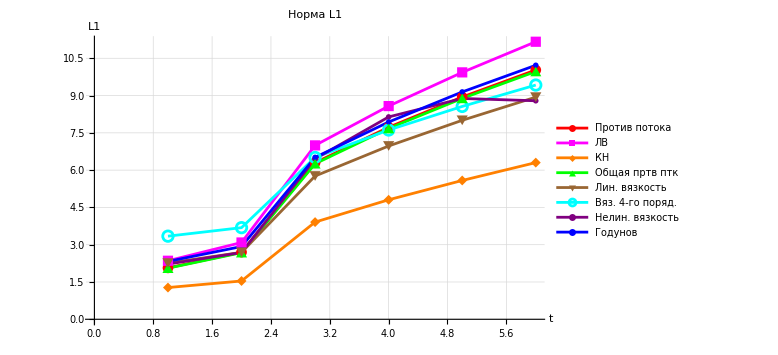

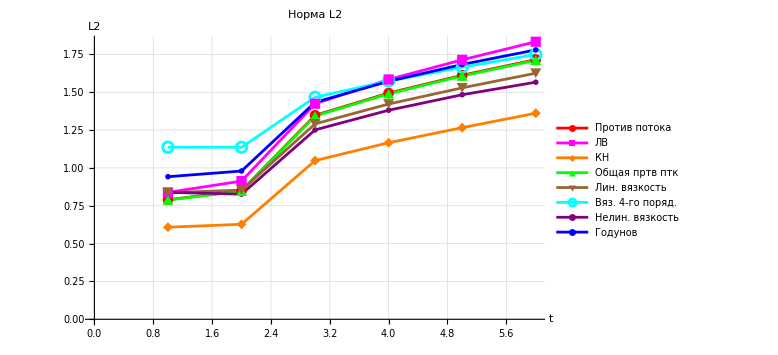

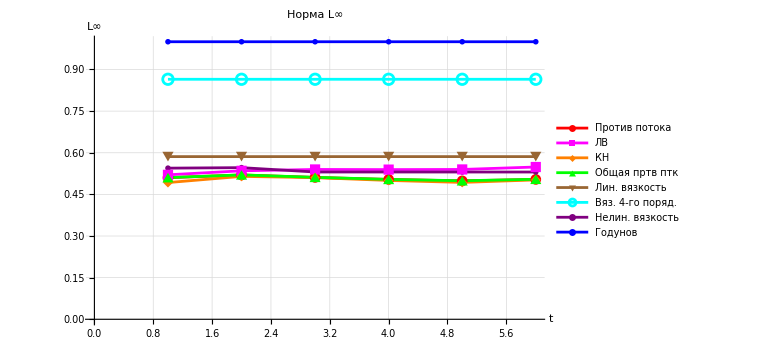

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

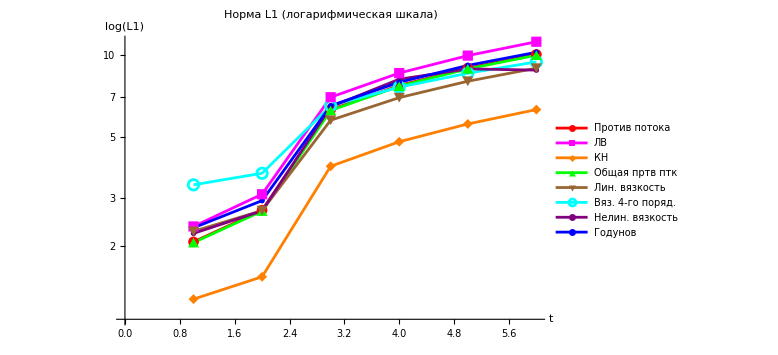

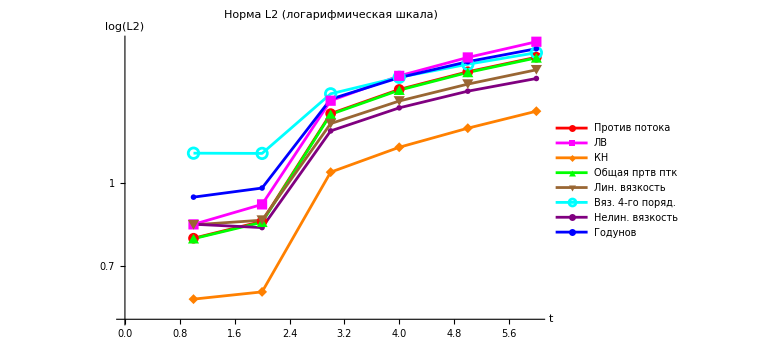

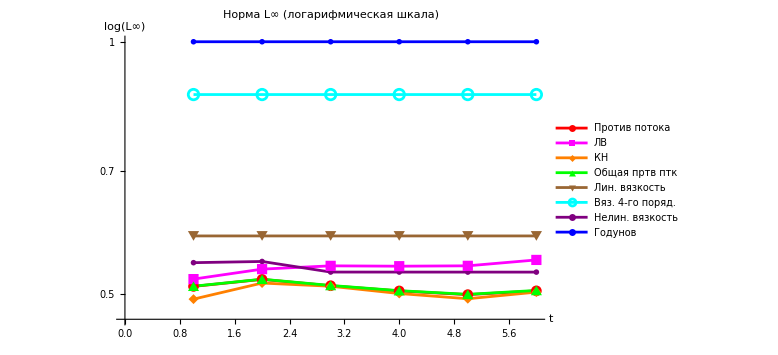

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=250"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 250",14],ImageSize->Large]
```

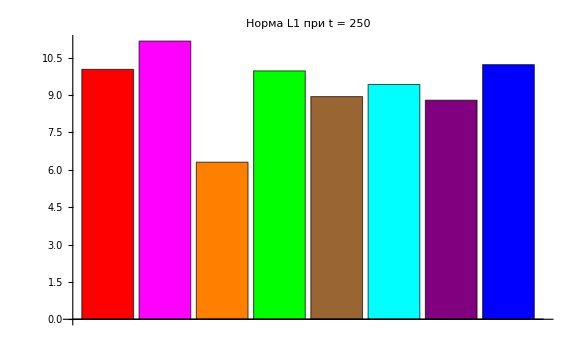

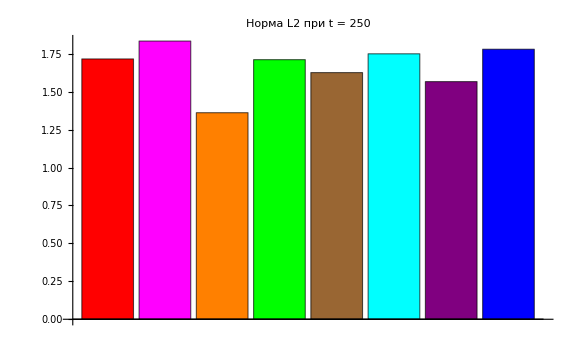

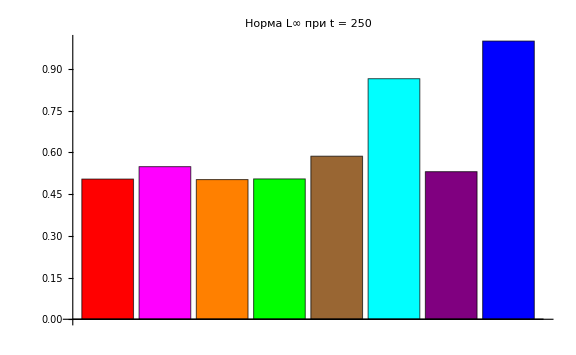

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
schemeNames=<|(*"Неявная против потока (3.14)"->{uImplicit,Red,True},(*"Неявная gen"->{uImplicitgen,Blue,False},*)"Неявная Лакс-Вендроффа (3.19)"->{uImplicitlaksven,Magenta,True},"Кранк-Николсон (3.15)"->{uImplicitkraknic,Orange,True},*)"Неявная апвинд (3.17)"->{uImplicitupwid,Green,True},(*"Линейная вязкость (3.20)"->{u320,White,True},"Вязкость 4-го порядка (3.18)"->{u318,Cyan,False},"Нелинейная вязкость (3.21)"->{u321,Purple,True},"Регуляриз. Лакс-Вендрофф (3.19)"->{u319,Brown,True},"Схема Годунова"->{uImplicitGod,RGBColor[0.1,0.5,0.8],True},*)"Аналитическое решение"->{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow,True}|>;
(*
plotAt[n_]:=
Module[
{lines={},colors={},data,col,flag,yvals},
Do[
{data,col,flag}=schemeNames[name];
If[flag,yvals=If[Head[data]===Function,data[n],data[[n]]];
If[Length[yvals]===Length[xgrid],AppendTo[lines,Transpose[{xgrid,yvals}]];
AppendTo[colors,col]]],{name,Keys[schemeNames]}];
ListLinePlot[lines,PlotStyle->colors,PlotRange->{{-2,280},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];
*)

plotAt[n_]:=Module[{lines={},colors={},data,col,flag,yvals,t,xCenter,xHalfWidth},t=(n-1) tau;
xCenter=t;
xHalfWidth=12;
Do[{data,col,flag}=schemeNames[name];
If[flag,yvals=If[Head[data]===Function,data[n],data[[n]]];
If[Length[yvals]===Length[xgrid],AppendTo[lines,Transpose[{xgrid,yvals}]];
AppendTo[colors,col]]],{name,Keys[schemeNames]}];
ListLinePlot[lines,PlotStyle->colors,PlotRange->{{-10,xmax},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[t,{3,2}]}],14,Bold]]];

stepForFrames=1; 
frameIndices=Range[1,nstep,stepForFrames];

frames=Table[plotAt[n],{n,frameIndices}];

Export["transport_schemes_nejavn_a(x).gif",frames,"DisplayDurations"->0.02,"AnimationRepetitions"->Infinity];

(*Export["transport_schemes_nejavn_a(x).mp4",frames,"FrameRate"->15];*)
```

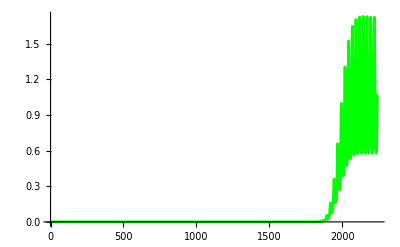

```mathematica
h=0.25;tau=0.5;xmax=280;nstep=500;
a[x_]:=1+0.5 Sin[x];
probfunc[x_]:=UnitStep[x];
xgrid=Range[-xmax,xmax,h];
len=Length[xgrid];
u=a/@xgrid;
C1=tau/(2*h);

(*Используем правила для SparseArray,это самый надежный способ*)
rules=Flatten[Table[{(*Диагональ A_{i,i}*){i,i}->1+C1*((u[[Min[i+1,len]]]+Abs[u[[Min[i+1,len]]]])-(u[[i]]-Abs[u[[i]]])),(*Нижняя диагональ A_{i,i-1}*)If[i>1,{i,i-1}->-C1*(u[[i]]+Abs[u[[i]]]),Nothing],(*Верхняя диагональ A_{i,i+1}*)If[i<len,{i,i+1}->C1*(u[[Min[i+1,len]]]-Abs[u[[Min[i+1,len]]]]),Nothing]},{i,1,len}]];

ALW=SparseArray[rules,{len,len}];

(*Граничное условие Dirichlet на входе*)
ALW[[1,1]]=1;
ALW[[1,2]]=0;

uImpl=ConstantArray[0,{nstep,len}];
uImpl[[1]]=probfunc/@xgrid;

Do[rhs=uImpl[[n]];
rhs[[1]]=0;(*Вход*)uImpl[[n+1]]=LinearSolve[ALW,rhs];,{n,1,nstep-1}];

ListLinePlot[uImpl[[nstep]],PlotRange->All,PlotStyle->Green]
```

```mathematica
(*При a=x-t*)
ClearAll["Global`*"]
h=0.025;        (*шаг по пространству*)
tau=0.05;    (*шаг по времени,CFL~0.9*)
xmax=20;      (*границы сетки*)
nstep=500;   (*шаги по времени,t_max=nstep*tau≈20*)
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)
a[x_]:=1+0.5 Sin[x];
probfunc[x_]:=UnitStep[x]
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[Exp[-t]*(x-1-t)+Exp[-t]];
xgrid=Range[-xmax,xmax,h];
len=Length[xgrid];
aGrid = a/@xgrid;
```

```mathematica
(*Неявная схема против потока*)
uImplicit=ConstantArray[0,{nstep,len}];
uImplicit[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
lambdaGrid=(xgrid-tCurr)*tau/h;
generaldig=ConstantArray[0.,len];
lowerdig=ConstantArray[0.,len-1];
upperdig=ConstantArray[0.,len-1];
rhs=uImplicit[[n]];
Do[
If[lambdaGrid[[i]]>=0,generaldig[[i]]=1+lambdaGrid[[i]];
If[i>1,lowerdig[[i-1]]=-lambdaGrid[[i]]];,
generaldig[[i]]=1-lambdaGrid[[i]];
If[i<len,upperdig[[i]]=lambdaGrid[[i]]];],{i,1,len}];
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];
rhs[[-1]]=uAnalytic[xgrid[[-1]],tCurr];

A=SparseArray[{
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig,
Band[{1,2}]->upperdig}
,{len,len}];

uImplicit[[n+1]]=LinearSolve[A,rhs];
,{n,1,nstep-1}];
```

```mathematica
(*Неявная центральная схема*)
uImplicitgen=ConstantArray[0,{nstep,len}];
uImplicitgen[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
lambdaGrid=(xgrid-tCurr)*tau/h;
generaldig=ConstantArray[1.,len];
lowerdig=-lambdaGrid[[2;;]]/2;
upperdig=lambdaGrid[[1;;-2]]/2;
generaldig[[1]]=1;generaldig[[-1]]=1;
lowerdig[[1]]=0;upperdig[[-1]]=0;
Agen=SparseArray[{Band[{1,1}]->generaldig,Band[{2,1}]->lowerdig,Band[{1,2}]->upperdig},{len,len}];
rhs=uImplicitgen[[n]];
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];
rhs[[-1]]=uAnalytic[xgrid[[-1]],tCurr];
uImplicitgen[[n+1]]=LinearSolve[Agen,rhs];,{n,1,nstep-1}];
```

```mathematica
(*Неявная схема Лакса-Вендроффа*)
uImplicitlaksven=ConstantArray[0,{nstep,len}];
uImplicitlaksven[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
lambdaGridCurr=(xgrid-tCurr)*tau/h;

upperdig=lambdaGridCurr[[1;;-2]]/2-(lambdaGridCurr[[1;;-2]]^2)/2;
generaldig=1+lambdaGridCurr^2;
lowerdig=-lambdaGridCurr[[2;;]]/2-(lambdaGridCurr[[2;;]]^2)/2;

ALW=SparseArray[{
Band[{1,2}]->upperdig,
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig}
,{len,len}];

uImplicitlaksven[[n+1]]=LinearSolve[ALW,uImplicitlaksven[[n]]];
uImplicitlaksven[[n+1,1]]=uAnalytic[-xmax,n*tau];
uImplicitlaksven[[n+1,-1]]=uAnalytic[xmax,n*tau];
,{n,1,nstep-1}]
```

```mathematica
(*Неявная схема Кранк-Николсон*)
uImplicitCN=ConstantArray[0,{nstep,len}];
uImplicitCN[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
lambdaGrid=(xgrid-tCurr)*tau/h;
generaldig=ConstantArray[0.,len];
lowerdig=ConstantArray[0.,len-1];
upperdig=ConstantArray[0.,len-1];
rhs=ConstantArray[0.,len];

Do[
If[lambdaGrid[[i]]>=0,
generaldig[[i]]=1+lambdaGrid[[i]]/2;

If[i>1,lowerdig[[i-1]]=-lambdaGrid[[i]]/2];
rhs[[i]]=(1-lambdaGrid[[i]]/2)*uImplicitCN[[n,i]]+If[i>1,(lambdaGrid[[i]]/2)*uImplicitCN[[n,i-1]],0];,
generaldig[[i]]=1-lambdaGrid[[i]]/2;
If[i<len,upperdig[[i]]=lambdaGrid[[i]]/2];
rhs[[i]]=(1+lambdaGrid[[i]]/2)*uImplicitCN[[n,i]]-If[i<len,(lambdaGrid[[i]]/2)*uImplicitCN[[n,i+1]],0];],{i,1,len}];
generaldig[[1]]=1;lowerdig[[1]]=0;upperdig[[1]]=0;
generaldig[[-1]]=1;lowerdig[[-1]]=0;upperdig[[-1]]=0;


ACN=SparseArray[{
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig,
Band[{1,2}]->upperdig}
,{len,len}];

uImplicitCN[[n+1]]=LinearSolve[ACN,rhs];
uImplicitCN[[n+1,1]]=uAnalytic[-xmax,n*tau];
uImplicitCN[[n+1,-1]]=uAnalytic[xmax,n*tau];
,{n,1,nstep-1}];
```

```mathematica
(*Неявная апвинд (3.17)*)
uImplicitupwid=ConstantArray[0,{nstep,len}];
uImplicitupwid[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
lambdaGrid=(xgrid-tCurr)*tau/h;
alpha=UnitStep[-lambdaGrid];  (*a<0*)
beta=UnitStep[lambdaGrid];  (*a>0*)

lowerdig=-beta[[2;;]] lambdaGrid[[2;;]];
upperdig=alpha[[1;;-2]] lambdaGrid[[1;;-2]];
generaldig=1+Abs[lambdaGrid];
ALW=SparseArray[{
Band[{1,2}]->upperdig,
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig},
{len,len}];


uImplicitupwid[[n+1]]=LinearSolve[ALW,uImplicitupwid[[n]]];
If[lambdaGrid[[1]]>0,uImplicitupwid[[n+1,1]]=uAnalytic[-xmax,n tau],uImplicitupwid[[n+1,-1]]=uAnalytic[xmax,n tau]];
,{n,1,nstep-1}];
```

```mathematica
u320=ConstantArray[0.,{nstep,len}];
omega=0.2;
u320[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
aCurr=xgrid-tCurr;
lambdaGrid=aCurr*tau/h;
upperC=lambdaGrid[[1;;-2]]/2;
lowerC=-lambdaGrid[[2;;]]/2;
diagC=ConstantArray[1.,len];
Acentral=SparseArray[{Band[{1,2}]->upperC,Band[{1,1}]->diagC,Band[{2,1}]->lowerC},{len,len}];
viscDiag=ConstantArray[2*omega,len];
viscUpper=ConstantArray[-omega,len-1];
viscLower=ConstantArray[-omega,len-1];
Avisc=SparseArray[{Band[{1,1}]->viscDiag,Band[{1,2}]->viscUpper,Band[{2,1}]->viscLower},{len,len}];
A320=Acentral+Avisc;
rhs=u320[[n]];
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];rhs[[-1]]=uAnalytic[xgrid[[-1]],tCurr];u320[[n+1]]=LinearSolve[A320,rhs];,{n,1,nstep-1}];
```

```mathematica
(*Вязкость 4-го порядка (3.18)*)
omega=0.3;
u318=ConstantArray[0,{nstep,len}];
u318[[1]]=probfunc/@xgrid;
Do[tCurr=(n-1)*tau;
aCurr=xgrid-tCurr;
lambdaGrid=aCurr*tau/h;
upperC=lambdaGrid[[1;;-2]]/2;
lowerC=-lambdaGrid[[2;;]]/2;
diagC=ConstantArray[1.,len];
Acentral=SparseArray[{
Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];

D4=SparseArray[{
Band[{1,1}]->6 omega/8,
Band[{1,2}]->-4 omega/8,
Band[{1,3}]->omega/8,
Band[{2,1}]->-4 omega/8,
Band[{3,1}]->omega/8}
,{len,len}];

A318=Acentral+tau D4;

u318[[n+1]]=LinearSolve[A318,u318[[n]]];
u318[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Регуляриз. Лакс-Вендрофф (3.19)*)
u319=ConstantArray[0,{nstep,len}];
u319[[1]]=probfunc/@xgrid;
Do[tCurr=(n-1)*tau;
aCurr=xgrid-tCurr;
lambdaGrid=aCurr*tau/h;
upperC=lambdaGrid[[1;;-2]]/2;
lowerC=-lambdaGrid[[2;;]]/2;
diagC=ConstantArray[1.,len];
Acentral=SparseArray[{
Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];

coef=(tau/2) (aCurr^2/h^2);
upperLW=-coef[[1;;-2]];
lowerLW=-coef[[2;;]];
diagLW=2 coef;

DLW=SparseArray[{Band[{1,1}]->diagLW,Band[{1,2}]->upperLW,Band[{2,1}]->lowerLW},{len,len}];
A319=Acentral+DLW;

u319[[n+1]]=LinearSolve[A319,u319[[n]]];,{n,1,nstep-1}]
```

```mathematica
(*Нелинейная вязкость (3.21)*)
omega=0.5;
u321=ConstantArray[0,{nstep,len}];
u321[[1]]=probfunc/@xgrid;
Do[tCurr=(n)*tau;
aCurr=xgrid-tCurr;
lambdaGrid=aCurr*tau/h;
upperC=lambdaGrid[[1;;-2]]/2;
lowerC=-lambdaGrid[[2;;]]/2;
diagC=ConstantArray[1.,len];
Acentral=SparseArray[{
Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];

ux=(RotateLeft[u321[[n]]]-RotateRight[u321[[n]]])/(2 h);
coef=omega tau (aCurr^2 Abs[ux])/h^2;
upper=-coef[[1;;-2]];
lower=-coef[[2;;]];
diag=2 coef;

A321=Acentral+SparseArray[{Band[{1,1}]->diag,Band[{1,2}]->upper,Band[{2,1}]->lower},{len,len}];
u321[[n+1]]=LinearSolve[A321,u321[[n]]];
u321[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Неявная схема Годунова*)
uImplicitGod=ConstantArray[0,{nstep,len}];
uImplicitGod[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
aGrid=xgrid-tCurr;
aHalf=(Most[aGrid]+Rest[aGrid])/2;
lambda=(tau/h)*aHalf;
mainDiag=ConstantArray[1,len];
lowerDiag=ConstantArray[0,len-1];
upperDiag=ConstantArray[0,len-1];
Do[If[aHalf[[i]]>0,
(*поток слева*)mainDiag[[i+1]]+=lambda[[i]];
lowerDiag[[i]]-=lambda[[i]],
(*поток справа*)mainDiag[[i]]-=lambda[[i]];
upperDiag[[i]]+=lambda[[i]]],{i,1,len-1}];
A=SparseArray[{Band[{1,1}]->mainDiag,Band[{2,1}]->lowerDiag,Band[{1,2}]->upperDiag},{len,len}];
uImplicitGod[[n+1]]=LinearSolve[A,uImplicitGod[[n]]];
,{n,1,nstep-1}];
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[
{If[showUpwind,Transpose[{xgrid,uImplicit[[n]]}],Nothing],
If[showGen,Transpose[{xgrid,uImplicitgen[[n]]}],Nothing],
If[showLaxVen,Transpose[{xgrid,uImplicitlaksven[[n]]}],Nothing],
If[showCrank,Transpose[{xgrid,uImplicitCN[[n]]}],Nothing],
If[showUpwid,Transpose[{xgrid,uImplicitupwid[[n]]}],Nothing],
If[show320,Transpose[{xgrid,u320[[n]]}],Nothing],
If[show318,Transpose[{xgrid,u318[[n]]}],Nothing],
If[show321,Transpose[{xgrid,u321[[n]]}],Nothing],
If[show319,Transpose[{xgrid,u319[[n]]}],Nothing],
If[godunov,Transpose[{xgrid,uImplicitGod[[n]]}],Nothing],
If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[
{If[showUpwind,Red,Nothing],
If[showGen,Blue,Nothing],
If[showLaxVen,Magenta,Nothing],
If[showCrank,Orange,Nothing],
If[showUpwid,Green,Nothing],
If[show320,Brown,Nothing],
If[show318,Cyan,Nothing],
If[show321,Purple,Nothing],
If[show319,Brown,Nothing],
If[godunov,RGBColor[0.1,0.5,0.8],Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1},Delimiter,{{showUpwind,True,Row[{Style["■",Red]," Неявная против потока (3.14)"}]},{True,False}},{{showGen,False,Row[{Style["■",Blue]," Неявная gen"}]},{True,False}},{{showLaxVen,True,Row[{Style["■",Magenta]," Неявная Лакс-Вендроффа (3.19)"}]},{True,False}},{{showCrank,True,Row[{Style["■",Orange]," Кранк-Николсон (3.15)"}]},{True,False}},{{showUpwid,True,Row[{Style["■",Green]," Неявная апвинд (3.17)"}]},{True,False}},{{show320,False,Row[{Style["■",Brown]," Линейная вязкость (3.20)"}]},{True,False}},{{show318,False,Row[{Style["■",Cyan]," Вязкость 4-го порядка (3.18)"}]},{True,False}},{{show321,True,Row[{Style["■",Purple]," Нелинейная вязкость (3.21)"}]},{True,False}},{{show319,True,Row[{Style["■",Brown]," Регуляриз. Лакс-Вендрофф (3.19)"}]},{True,False}},
{{godunov,True,Row[{Style["■",RGBColor[0.1,0.5,0.8]]," Схема Годунова "}]},{True,False}},{{showExact,True,Row[{Style["■",Yellow]," Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-xmax,xmax},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax+10,"Масштаб X"},1,xmax+10},{{sy,0.6,"Масштаб Y"},0.1,2},TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showGen,showLaxVen,showCrank,showUpwid,show320,show318,show321,show319,godunov,showExact}]
```

```mathematica
uAnalyticGrid[t_]:=uAnalytic[#,t]&/@xgrid;

ClearAll[normL1,normL2,normLinf];
normL1[err_]:=h Total[Abs[err]];
normL2[err_]:=Sqrt[h Total[err^2]];
normLinf[err_]:=Max[Abs[err]];

timeIndices=<|"t=1"->21,"t=2.25"->46,"t=3"->61,"t=10"->201,"t=22"->441,"t=24"->481|>;


computeNorms[uNum_,k_]:=Module[{t,err},t=(k-1) tau;
err=uNum[[k]]-uAnalyticGrid[t];
{normL1[err],normL2[err],normLinf[err]}];


schemes=<|"Против потока "->uImplicit,"Центральная "->uImplicitgen,"ЛВ"->uImplicitlaksven,"КН"->uImplicitCN,"Общая пртв птк"->uImplicitupwid,"Лин. вязкость"->u320,"Вяз. 4-го поряд. "->u318,"Нелин. вязкость"->u321,"Годунов "->uImplicitGod|>;

errors=Association@Table[scheme->Association@Table[time->computeNorms[schemes[scheme],timeIndices[time]],{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];


norms={"L1","L2","L∞"};
times={"t=1","t=2.25","t=3","t=10","t=22","t=24"};

header1=Join[{""},Flatten@Table[ConstantArray[Style[norm,Bold],Length[times]],{norm,norms}]];

header2=Join[{Style["Схема",Bold]},Flatten@Table[times,{Length[norms]}]];


rowForScheme[scheme_]:=Prepend[Flatten@Table[errors[scheme][time][[i]],{i,3},{time,times}],Style[scheme,Bold]];

tableData=Join[{header1,header2},rowForScheme/@Keys[errors]];

Grid[tableData,Frame->All,Alignment->Center,Spacings->{1.4,1.2},ItemStyle->Directive[14],Background->{None,{Lighter[Gray,.9],LightGray,None}},Dividers->{{False,True},{False,True,False}}]
```

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | L∞ | L∞ | L∞ | L∞ | L∞ | L∞
Схема | t=1 | t=2.25 | t=3 | t=10 | t=22 | t=24 | t=1 | t=2.25 | t=3 | t=10 | t=22 | t=24 | t=1 | t=2.25 | t=3 | t=10 | t=22 | t=24
Против потока  | 1.83425 | 9.27705 | 19.0874 | 29.9996 | 35.0488 | 2.0685 | 1.27814 | 2.7973 | 4.11813 | 5.47715 | 5.83289 | 0.576285 | 1. | 1. | 1. | 1. | 1. | 0.264169
Центральная  | 14.8347 | 26.4557 | 37.1169 | 42. | 42.2 | 42.4 | 6.99583 | 7.44373 | 8.23493 | 13.0362 | 16.025 | 16.5891 | 38. | 35.5 | 34. | 60. | 84. | 88.
ЛВ | 2.28968 | 10.2737 | 19.2998 | 29.5017 | 33.6898 | 2.53416 | 1.35289 | 2.84197 | 4.10275 | 5.38834 | 5.63852 | 0.609196 | 1. | 1. | 1. | 1. | 0.999868 | 0.212894
КН | 1.80479 | 8.9168 | 19.8043 | 29.975 | 35.2805 | 0.415955 | 1.29921 | 2.88749 | 4.32661 | 5.47494 | 5.9024 | 0.139603 | 1. | 1.01713 | 1.03997 | 1. | 1. | 0.0694287
Общая пртв птк | 1.83425 | 9.27705 | 19.0875 | 30. | 35.0756 | 2.09679 | 1.27814 | 2.7973 | 4.11814 | 5.47723 | 5.83569 | 0.583502 | 1. | 1. | 1. | 1. | 1. | 0.267495
Лин. вязкость | 2.7806 | 9.69992 | 19.4232 | 30.5436 | 35.4534 | 2.41145 | 1.44031 | 2.81715 | 4.09541 | 5.57227 | 5.97788 | 0.767792 | 1. | 1. | 1. | 1.92296 | 1.94438 | 0.594098
Вяз. 4-го поряд.  | 11.2485 | 19.831 | 29.4182 | 36.5024 | 36.7921 | 20.6911 | 3.00197 | 3.95997 | 4.93853 | 6.81234 | 7.26875 | 3.6533 | 1.01659 | 1.00123 | 1.05988 | 1.93409 | 1.9525 | 0.963317
Нелин. вязкость | 3.48374 | 12.4939 | 20.3074 | 29.2378 | 29.0039 | 1.17668 | 1.58091 | 3.04889 | 4.19844 | 5.30659 | 5.03155 | 0.302435 | 1.0001 | 1. | 1. | 1. | 0.998748 | 0.121155
Годунов  | 1.81188 | 9.16457 | 18.9511 | 30. | 40.025 | 40.025 | 1.27115 | 2.78125 | 4.09788 | 5.47723 | 6.32653 | 6.32653 | 1. | 1. | 1. | 1. | 1. | 1.

```mathematica
schemeColors=<|"Против потока "->Red,"Центральная "->RGBColor[0.1,0.5,0.8],"ЛВ"->Magenta,"КН"->Orange,"Общая пртв птк"->Green,"Лин. вязкость"->Brown,"Вяз. 4-го поряд. "->Cyan,"Нелин. вязкость"->Purple,"Годунов "->Blue|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

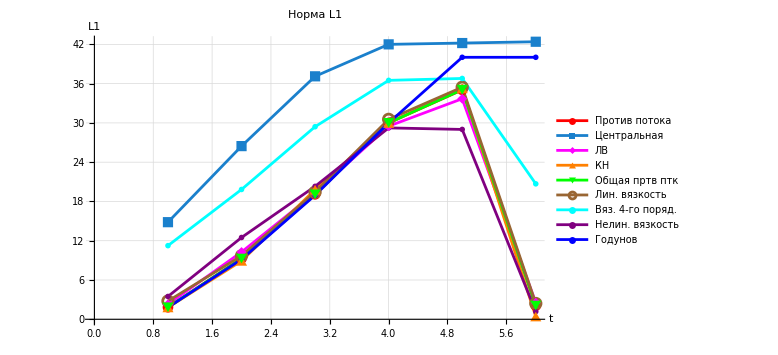

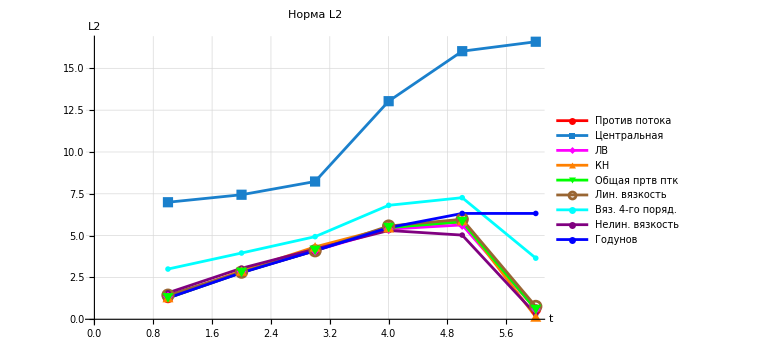

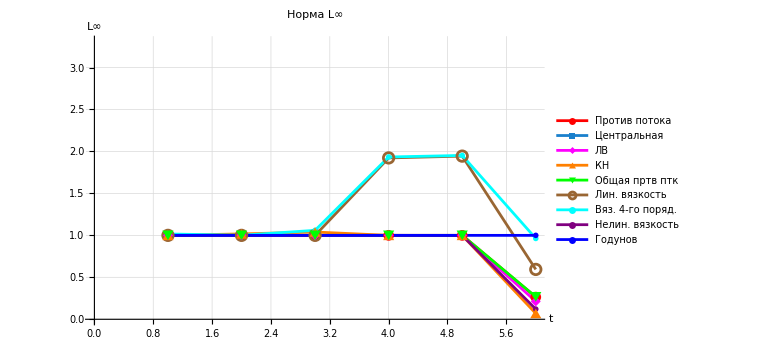

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

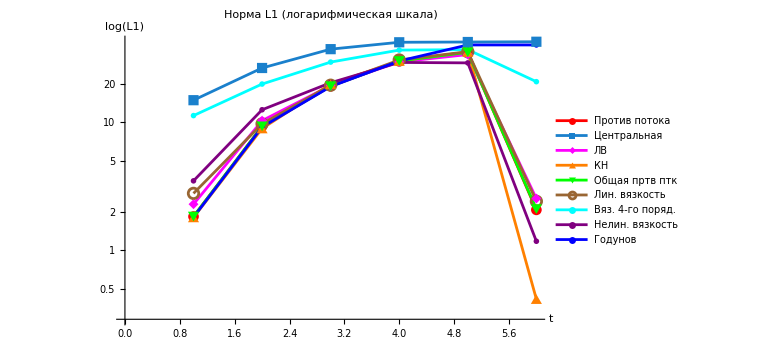

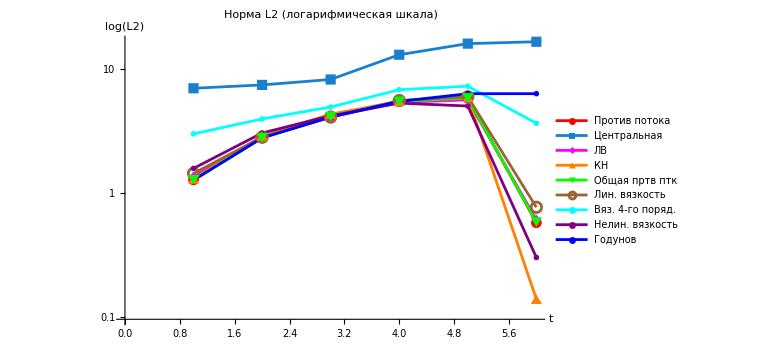

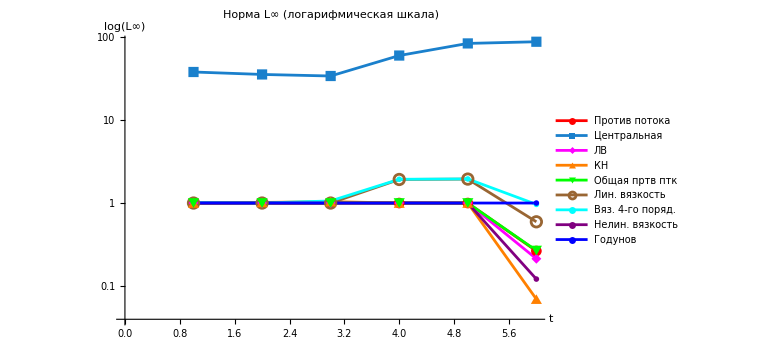

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=22"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 22",14],ImageSize->Large]
```

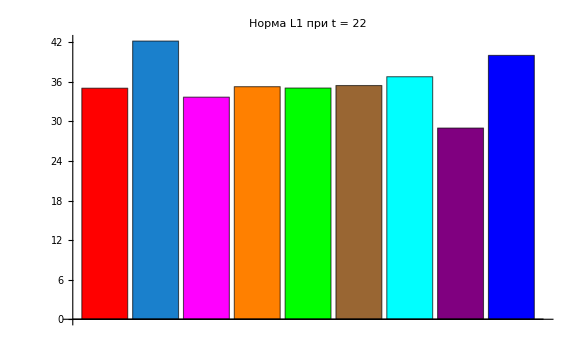

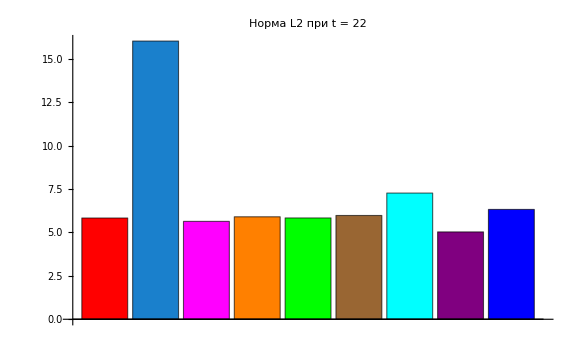

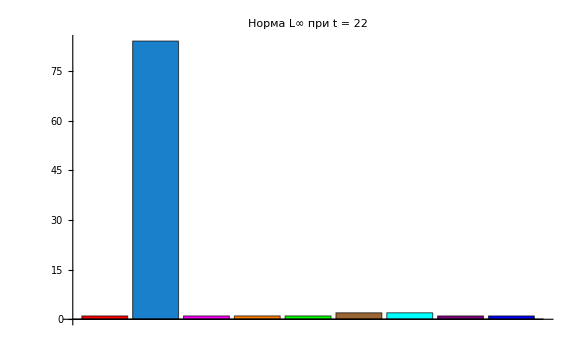

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
schemeNames=<|"Неявная против потока (3.14)"->{uImplicit,Red,True},(*"Неявная gen"->{uImplicitgen,Blue,False},*)"Неявная Лакс-Вендроффа (3.19)"->{uImplicitlaksven,Magenta,True},"Кранк-Николсон (3.15)"->{uImplicitCN,Orange,True},"Неявная апвинд (3.17)"->{uImplicitupwid,Green,True},"Линейная вязкость (3.20)"->{u320,White,False},"Вязкость 4-го порядка (3.18)"->{u318,Cyan,False},"Нелинейная вязкость (3.21)"->{u321,Purple,True},"Регуляриз. Лакс-Вендрофф (3.19)"->{u319,Brown,True},"Схема Годунова"->{uImplicitGod,RGBColor[0.1,0.5,0.8],True},"Аналитическое решение"->{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow,True}|>;

plotAt[n_]:=
Module[
{lines={},colors={},data,col,flag,yvals},
Do[
{data,col,flag}=schemeNames[name];
If[flag,yvals=If[Head[data]===Function,data[n],data[[n]]];
If[Length[yvals]===Length[xgrid],AppendTo[lines,Transpose[{xgrid,yvals}]];
AppendTo[colors,col]]],{name,Keys[schemeNames]}];
ListLinePlot[lines,PlotStyle->colors,PlotRange->{{-10,0},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];

stepForFrames=1; 
frameIndices=Range[1,nstep,stepForFrames];

frames=Table[plotAt[n],{n,frameIndices}];

Export["transport_schemes_nejavn_a_x-t.gif",frames,"DisplayDurations"->0.02,"AnimationRepetitions"->Infinity];

(*Export["transport_schemes_nejavn_a_x-t.mp4",frames,"FrameRate"->15];*)
```

```mathematica
(*При a=a(t)*)
ClearAll["Global`*"]
h=0.025;
tau=0.05;
xmax=10;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);
v[t_]:=(-1)^IntegerPart[t] a[t_]:=Piecewise[{{FractionalPart[t],EvenQ[IntegerPart[t]]},{1-FractionalPart[t],OddQ[IntegerPart[t]]}}]*)
a[t_]:=(-1)^IntegerPart[t]
fsol=NDSolve[{s'[t]==a[t],s[0]==0},s,{t,0,nstep*tau}][[1]];

(*probfunc[x_]:=UnitStep[x]-UnitStep[x-1]+UnitStep[x-2]-UnitStep[x-3]+UnitStep[x-4]-UnitStep[x-5]*)
probfunc[x_]:=UnitStep[x]-UnitStep[x-1]

uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[x-(s[t]/. fsol)]

xgrid=Range[-xmax,xmax,h];
tgrid=Range[0,tau*nstep,tau];
aGrid = a@tgrid;
len=Length[xgrid];
(*lambdaGrid=aGrid*tau/h;*)
```

```mathematica
(*Неявная схема против потока*)
uImplicit=ConstantArray[0.,{nstep,len}];
uImplicit[[1]]=probfunc/@xgrid;

Do[
tCurr=n*tau;
ai=a[tCurr];
lambda=ai*tau/h;
generaldig=ConstantArray[1.,len];
lowerdig=ConstantArray[0.,len-1];
upperdig=ConstantArray[0.,len-1];

If[ai>=0,
generaldig=ConstantArray[1.+lambda,len];
lowerdig=ConstantArray[-lambda,len-1];
upperdig=ConstantArray[0.,len-1];,

generaldig=ConstantArray[1.-lambda,len];
upperdig=ConstantArray[lambda,len-1];
lowerdig=ConstantArray[0.,len-1];];
rhs=uImplicit[[n]];
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];
rhs[[-1]]=uAnalytic[xgrid[[-1]],tCurr];

A=SparseArray[{
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig,
Band[{1,2}]->upperdig}
,{len,len}];

uImplicit[[n+1]]=LinearSolve[A,rhs];,{n,1,nstep-1}];
```

```mathematica
(*Неявная центральная схема*)
uImplicitgen=ConstantArray[0,{nstep,len}];
uImplicitgen[[1]]=probfunc/@xgrid;

Do[
tCurr=n*tau;
ai=a[tCurr];
lambda=ai*tau/h;

generaldig=ConstantArray[1.,len];
lowerdig=ConstantArray[-lambda/2,len-1];
upperdig=ConstantArray[lambda/2,len-1];

generaldig[[1]]=1;
generaldig[[-1]]=1;
lowerdig[[1]]=0;
upperdig[[-1]]=0;

Agen=SparseArray[{
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig,
Band[{1,2}]->upperdig}
,{len,len}];

rhs=uImplicitgen[[n]];
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];
rhs[[-1]]=uAnalytic[xgrid[[-1]],tCurr];
uImplicitgen[[n+1]]=LinearSolve[Agen,rhs];,{n,1,nstep-1}];
```

```mathematica
(*Неявная схема Лакса-Вендроффа*)
uImplicitlaksven=ConstantArray[0,{nstep,len}];
uImplicitlaksven[[1]]=probfunc/@xgrid;

Do[
tCurr=n*tau;
ai=a[tCurr];
lambdaCurr=ai*tau/h;
upperdig=ConstantArray[lambdaCurr/2-(lambdaCurr^2)/2,len-1];
generaldig=ConstantArray[1+lambdaCurr^2,len];
lowerdig=ConstantArray[-lambdaCurr/2-(lambdaCurr^2)/2,len-1];

ALW=SparseArray[{
Band[{1,2}]->upperdig,
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig}
,{len,len}];

uImplicitlaksven[[n+1]]=LinearSolve[ALW,uImplicitlaksven[[n]]];
uImplicitlaksven[[n+1,1]]=uAnalytic[-xmax,n*tau];
uImplicitlaksven[[n+1,-1]]=uAnalytic[xmax,n*tau];,{n,1,nstep-1}]
```

```mathematica
(*Неявная схема Кранк-Николсон*)
uImplicitCN=ConstantArray[0,{nstep,len}];
uImplicitCN[[1]]=probfunc/@xgrid;

Do[
tCurr=n*tau;
ai=a[tCurr];
lambda=ai*tau/h;
rhs=ConstantArray[0.,len];
If[lambda>=0,
generaldig=ConstantArray[1+lambda/2,len];
lowerdig=ConstantArray[-lambda/2,len-1];
upperdig=ConstantArray[0.,len-1];,

generaldig=ConstantArray[1-lambda/2,len];
lowerdig=ConstantArray[0.,len-1];
upperdig=ConstantArray[lambda/2,len-1];
];

Do[
If[
lambda>=0,
rhs[[i]]=(1-lambda/2)*uImplicitCN[[n,i]]+If[i>1,lambda/2*uImplicitCN[[n,i-1]],0],rhs[[i]]=(1+lambda/2)*uImplicitCN[[n,i]]-If[i<len,lambda/2*uImplicitCN[[n,i+1]],0]]
,{i,1,len}];

generaldig[[1]]=1;lowerdig[[1]]=0;
generaldig[[-1]]=1;upperdig[[-1]]=0;
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];
rhs[[-1]]=uAnalytic[xgrid[[-1]],tCurr];

ACN=SparseArray[{Band[{1,1}]->generaldig,Band[{2,1}]->lowerdig,Band[{1,2}]->upperdig},{len,len}];
uImplicitCN[[n+1]]=LinearSolve[ACN,rhs];,{n,1,nstep-1}];
```

```mathematica
(*Неявная апвинд (3.17)*)
uImplicitupwid=ConstantArray[0,{nstep,len}];
uImplicitupwid[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
ai=a[tCurr];
lambda=ai*tau/h;
alpha=UnitStep[-lambda];
beta=UnitStep[lambda];

lowerdig=ConstantArray[-beta*lambda,len-1];
upperdig=ConstantArray[alpha*lambda,len-1];
generaldig=ConstantArray[1+Abs[lambda],len];

ALW=SparseArray[{
Band[{1,2}]->upperdig,
Band[{1,1}]->generaldig,
Band[{2,1}]->lowerdig}
,{len,len}];

uImplicitupwid[[n+1]]=LinearSolve[ALW,uImplicitupwid[[n]]];
If[lambda>0,uImplicitupwid[[n+1,1]]=uAnalytic[-xmax,n tau],uImplicitupwid[[n+1,-1]]=uAnalytic[xmax,n tau]];
,{n,1,nstep-1}];
```

```mathematica
u320=ConstantArray[0.,{nstep,len}];
omega=0.2;
u320[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
ai=a[tCurr];
lambda=ai*tau/h;
upperC=ConstantArray[lambda/2,len-1];
lowerC=ConstantArray[-lambda/2,len-1];
diagC=ConstantArray[1.,len];

Acentral=SparseArray[
{Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];

viscDiag=ConstantArray[2*omega,len];
viscUpper=ConstantArray[-omega,len-1];
viscLower=ConstantArray[-omega,len-1];

Avisc=SparseArray[{
Band[{1,1}]->viscDiag,
Band[{1,2}]->viscUpper,
Band[{2,1}]->viscLower}
,{len,len}];

A320=Acentral+Avisc;
rhs=u320[[n]];
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];
rhs[[-1]]=uAnalytic[xgrid[[-1]],tCurr];
u320[[n+1]]=LinearSolve[A320,rhs];,{n,1,nstep-1}];
```

```mathematica
(*Вязкость 4-го порядка (3.18)*)
omega=0.3;
u318=ConstantArray[0,{nstep,len}];
u318[[1]]=probfunc/@xgrid;
Do[tCurr=(n-1)*tau;
ai=a[tCurr];
lambda=ai*tau/h;

upperC=ConstantArray[lambda/2,len-1];
lowerC=ConstantArray[-lambda/2,len-1];
diagC=ConstantArray[1.,len];

Acentral=SparseArray[{
Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];

D4=SparseArray[{
Band[{1,1}]->6 omega/8,
Band[{1,2}]->-4 omega/8,
Band[{1,3}]->omega/8,
Band[{2,1}]->-4 omega/8,
Band[{3,1}]->omega/8}
,{len,len}];

A318=Acentral+tau D4;
u318[[n+1]]=LinearSolve[A318,u318[[n]]];
u318[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Регуляриз.Лакс-Вендрофф (3.19)*)
u319=ConstantArray[0,{nstep,len}];
u319[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
ai=a[tCurr];
lambda=ai*tau/h;

upperC=ConstantArray[lambda/2,len-1];
lowerC=ConstantArray[-lambda/2,len-1];
diagC=ConstantArray[1.,len];

Acentral=SparseArray[{
Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];

coef=(tau/2) (ai^2/h^2);
upperLW=ConstantArray[-coef,len-1];
lowerLW=ConstantArray[-coef,len-1];
diagLW=ConstantArray[2*coef,len];
DLW=SparseArray[{
Band[{1,1}]->diagLW,
Band[{1,2}]->upperLW,
Band[{2,1}]->lowerLW}
,{len,len}];

A319=Acentral+DLW;
u319[[n+1]]=LinearSolve[A319,u319[[n]]];,{n,1,nstep-1}]
```

```mathematica
(*Нелинейная вязкость (3.21)*)
omega=0.5;
u321=ConstantArray[0,{nstep,len}];
u321[[1]]=probfunc/@xgrid;

Do[tCurr=(n)*tau;
ai=a[tCurr];
lambda=ai*tau/h;
upperC=ConstantArray[lambda/2,len-1];
lowerC=ConstantArray[-lambda/2,len-1];
diagC=ConstantArray[1.,len];

Acentral=SparseArray[{
Band[{1,2}]->upperC,
Band[{1,1}]->diagC,
Band[{2,1}]->lowerC}
,{len,len}];

ux=(RotateLeft[u321[[n]]]-RotateRight[u321[[n]]])/(2 h);
coef=omega tau (ai^2 Abs[ux])/h^2;
upper=-coef[[1;;-2]];
lower=-coef[[2;;]];
diag=2 coef;
A321=Acentral+SparseArray[{Band[{1,1}]->diag,Band[{1,2}]->upper,Band[{2,1}]->lower},{len,len}];
u321[[n+1]]=LinearSolve[A321,u321[[n]]];
u321[[n+1,1]]=uAnalytic[-xmax,n tau];,{n,1,nstep-1}]
```

```mathematica
(*Неявная схема Годунова*)
uImplicitGod=ConstantArray[0,{nstep,len}];
uImplicitGod[[1]]=probfunc/@xgrid;

Do[tCurr=n*tau;
ai=a[tCurr];
lambda=(tau/h)*ai;

mainDiag=ConstantArray[1,len];
lowerDiag=ConstantArray[0,len-1];
upperDiag=ConstantArray[0,len-1];
Do[
If[ai>0,
mainDiag[[i+1]]+=lambda;
lowerDiag[[i]]-=lambda,

mainDiag[[i]]-=lambda;
upperDiag[[i]]+=lambda]
,{i,1,len-1}];

A=SparseArray[{
Band[{1,1}]->mainDiag,
Band[{2,1}]->lowerDiag,
Band[{1,2}]->upperDiag}
,{len,len}];
uImplicitGod[[n+1]]=LinearSolve[A,uImplicitGod[[n]]];,{n,1,nstep-1}];
```

```mathematica
Manipulate[ListLinePlot[DeleteCases[{
If[showUpwind,Transpose[{xgrid,uImplicit[[n]]}],Nothing],If[showGen,Transpose[{xgrid,uImplicitgen[[n]]}],Nothing],If[showLaxVen,Transpose[{xgrid,uImplicitlaksven[[n]]}],Nothing],If[showCrank,Transpose[{xgrid,uImplicitCN[[n]]}],Nothing],If[showUpwid,Transpose[{xgrid,uImplicitupwid[[n]]}],Nothing],If[show320,Transpose[{xgrid,u320[[n]]}],Nothing],
If[show318,Transpose[{xgrid,u318[[n]]}],Nothing],
If[show321,Transpose[{xgrid,u321[[n]]}],Nothing],
If[show319,Transpose[{xgrid,u319[[n]]}],Nothing],If[godunov,Transpose[{xgrid,uImplicitGod[[n]]}],Nothing],If[showExact,Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}],Nothing]},Nothing],PlotStyle->DeleteCases[{
If[showUpwind,Red,Nothing],
If[showGen,Blue,Nothing],
If[showLaxVen,Magenta,Nothing],
If[showCrank,Orange,Nothing],
If[showUpwid,Green,Nothing],
If[show320,Brown,Nothing],
If[show318,Cyan,Nothing],
If[show321,Purple,Nothing],
If[show319,Brown,Nothing],
If[godunov,RGBColor[0.1,0.5,0.8],Nothing],
If[showExact,Yellow,Nothing]},Nothing],PlotRange->Evaluate[{{x0-sx,x0+sx},{y0-sy,y0+sy}}],GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]],{n,1,nstep,1},Delimiter,
{{showUpwind,True,Row[{Style["■",Red]," Неявная против потока (3.14)"}]},{True,False}},{{showGen,False,Row[{Style["■",Blue]," Неявная gen"}]},{True,False}},{{showLaxVen,True,Row[{Style["■",Magenta]," Неявная Лакс-Вендроффа (3.19)"}]},{True,False}},{{showCrank,True,Row[{Style["■",Orange]," Кранк-Николсон (3.15)"}]},{True,False}},{{showUpwid,True,Row[{Style["■",Green]," Неявная апвинд (3.17)"}]},{True,False}},{{show320,False,Row[{Style["■",Brown]," Линейная вязкость (3.20)"}]},{True,False}},{{show318,False,Row[{Style["■",Cyan]," Вязкость 4-го порядка (3.18)"}]},{True,False}},{{show321,True,Row[{Style["■",Purple]," Нелинейная вязкость (3.21)"}]},{True,False}},{{show319,True,Row[{Style["■",Brown]," Регуляриз. Лакс-Вендрофф (3.19)"}]},{True,False}},{{godunov,True,Row[{Style["■",RGBColor[0.1,0.5,0.8]]," Схема Годунова"}]},{True,False}},{{showExact,True,Row[{Style["■",Yellow]," Аналитическое решение"}]},{True,False}},Delimiter,(*Центр камеры*){{x0,0,"Центр X"},-50,50},{{y0,0.5,"Центр Y"},-1,2},(*Масштаб*){{sx,xmax,"Масштаб X"},1,50},{{sy,0.6,"Масштаб Y"},0.1,2},TrackedSymbols:>{n,x0,y0,sx,sy,showUpwind,showGen,showLaxVen,showCrank,showUpwid,show320,show318,show321,show319,godunov,showExact}]
```

```mathematica
uAnalyticGrid[t_]:=uAnalytic[#,t]&/@xgrid;

ClearAll[normL1,normL2,normLinf];
normL1[err_]:=h Total[Abs[err]];
normL2[err_]:=Sqrt[h Total[err^2]];
normLinf[err_]:=Max[Abs[err]];

timeIndices=<|"t=0.5"->11,"t=0.95"->20,"t=5"->101,"t=25"->501,"t=40"->801,"t=49"->981|>;


computeNorms[uNum_,k_]:=Module[
{t,err},t=(k-1) tau;
err=uNum[[k]]-uAnalyticGrid[t];
{normL1[err],normL2[err],normLinf[err]}];


schemes=<|
"Против потока "->uImplicit,
"Центральная "->uImplicitgen,
"ЛВ"->uImplicitlaksven,
"КН"->uImplicitCN,
"Общая пртв птк"->uImplicitupwid,
"Лин. вязкость"->u320,
"Вяз. 4-го поряд. "->u318,
"Нелин. вязкость"->u321,
"Годунов "->uImplicitGod|>;

errors=Association@Table[
scheme->Association@Table[
time->computeNorms[schemes[scheme],timeIndices[time]]
,{time,Keys[timeIndices]}],{scheme,Keys[schemes]}];


norms={"L1","L2","L∞"};
times={"t=0.5","t=0.95","t=5","t=25","t=40","t=49"};

header1=Join[{""},Flatten@Table[ConstantArray[Style[norm,Bold],Length[times]],{norm,norms}]];

header2=Join[{Style["Схема",Bold]},Flatten@Table[times,{Length[norms]}]];


rowForScheme[scheme_]:=Prepend[Flatten@Table[errors[scheme][time][[i]],{i,3},{time,times}],Style[scheme,Bold]];

tableData=Join[{header1,header2},rowForScheme/@Keys[errors]];

Grid[tableData,Frame->All,Alignment->Center,Spacings->{1.4,1.2},ItemStyle->Directive[14],Background->{None,{Lighter[Gray,.9],LightGray,None}},Dividers->{{False,True},{False,True,False}}]
```

General::munfl: (3.84644×10^-241)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.66211×10^-240)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.02534×10^-240)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| L1 | L1 | L1 | L1 | L1 | L1 | L2 | L2 | L2 | L2 | L2 | L2 | L∞ | L∞ | L∞ | L∞ | L∞ | L∞
Схема | t=0.5 | t=0.95 | t=5 | t=25 | t=40 | t=49 | t=0.5 | t=0.95 | t=5 | t=25 | t=40 | t=49 | t=0.5 | t=0.95 | t=5 | t=25 | t=40 | t=49
Против потока  | 0.306014 | 0.423543 | 0.93205 | 1.44258 | 1.55137 | 1.59322 | 0.300884 | 0.354671 | 0.59049 | 0.802669 | 0.843854 | 0.859526 | 0.51736 | 0.513636 | 0.59864 | 0.738931 | 0.782132 | 0.803375
Центральная  | 0.263535 | 0.370247 | 0.801064 | 1.33239 | 1.45779 | 1.5075 | 0.274823 | 0.320339 | 0.529485 | 0.759187 | 0.808282 | 0.827515 | 0.546048 | 0.511699 | 0.588776 | 0.695627 | 0.74114 | 0.765427
ЛВ | 0.353254 | 0.48853 | 1.03277 | 1.5119 | 1.60886 | 1.64559 | 0.322956 | 0.383167 | 0.634393 | 0.829165 | 0.865178 | 0.878686 | 0.517222 | 0.515278 | 0.614462 | 0.767748 | 0.808694 | 0.827299
КН | 0.176197 | 0.244312 | 0.584566 | 1.11127 | 1.26213 | 1.32641 | 0.228077 | 0.268051 | 0.441525 | 0.668061 | 0.730176 | 0.757002 | 0.5 | 0.500002 | 0.602273 | 0.628779 | 0.660473 | 0.694383
Общая пртв птк | 0.306014 | 0.423543 | 0.93205 | 1.44258 | 1.55137 | 1.59322 | 0.300884 | 0.354671 | 0.59049 | 0.802669 | 0.843854 | 0.859526 | 0.51736 | 0.513636 | 0.59864 | 0.738931 | 0.782132 | 0.803375
Лин. вязкость | 0.262067 | 0.362806 | 0.810629 | 1.3571 | 1.48113 | 1.52809 | 0.278825 | 0.327503 | 0.530024 | 0.768649 | 0.817248 | 0.835098 | 0.516547 | 0.512262 | 0.524678 | 0.695494 | 0.75059 | 0.770593
Вяз. 4-го поряд.  | 0.259944 | 0.359781 | 0.777961 | 1.32945 | 1.45776 | 1.50651 | 0.274002 | 0.319914 | 0.514602 | 0.757543 | 0.808254 | 0.826926 | 0.538063 | 0.511698 | 0.518604 | 0.684 | 0.740339 | 0.760755
Нелин. вязкость | 0.688795 | 0.875253 | 1.27525 | 1.54765 | 1.61123 | 1.63827 | 0.487228 | 0.570477 | 0.739837 | 0.843423 | 0.866417 | 0.87641 | 0.560076 | 0.586966 | 0.691136 | 0.787225 | 0.812131 | 0.825852
Годунов  | 0.306014 | 0.423543 | 0.93205 | 1.44258 | 1.55137 | 1.59322 | 0.300884 | 0.354671 | 0.59049 | 0.802669 | 0.843854 | 0.859526 | 0.51736 | 0.513636 | 0.59864 | 0.738931 | 0.782132 | 0.803375

```mathematica
schemeColors=<|"Против потока "->Red,"Центральная "->RGBColor[0.1,0.5,0.8],"ЛВ"->Magenta,"КН"->Orange,"Общая пртв птк"->Green,"Лин. вязкость"->Brown,"Вяз. 4-го поряд. "->Cyan,"Нелин. вязкость"->Purple,"Годунов "->Blue|>;
getNormData[normIndex_]:=Table[errors[scheme][time][[normIndex]],{scheme,Keys[schemes]},{time,times}];
plotNormDynamic[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t",normName},PlotLabel->Style["Норма "<>normName,14],ImageSize->Large]
```

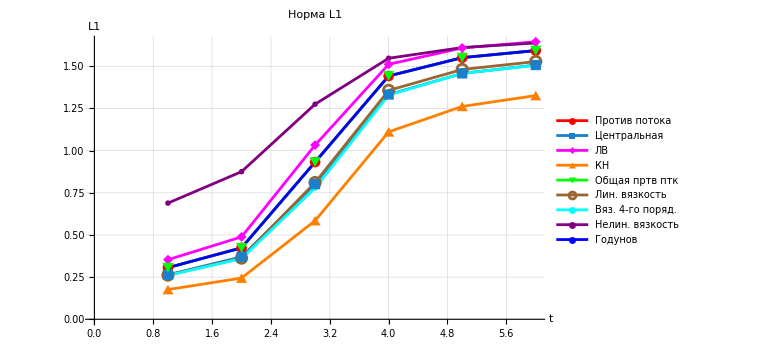

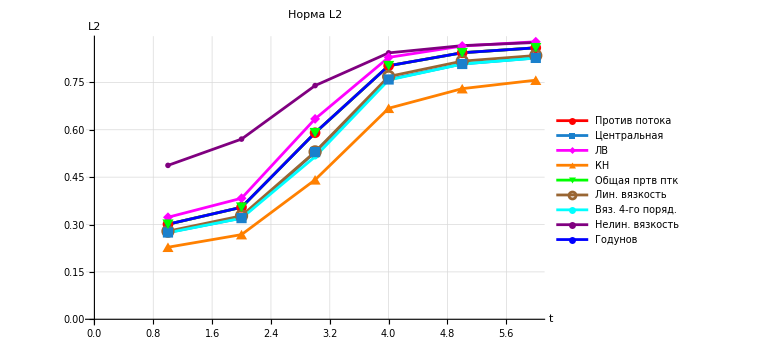

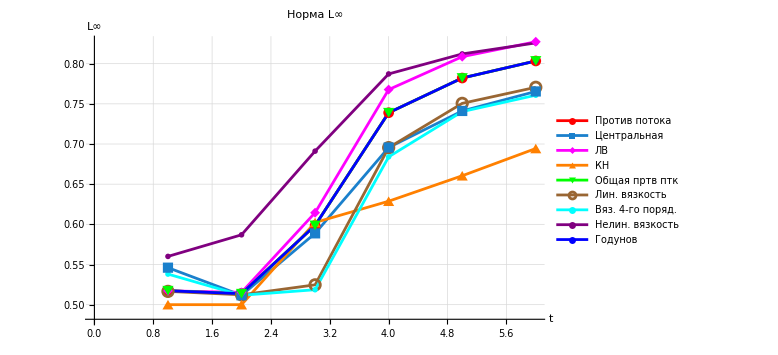

```mathematica
plotNormDynamic[1,"L1"]
plotNormDynamic[2,"L2"]
plotNormDynamic[3,"L∞"]
```

```mathematica
plotNormLog[normIndex_,normName_]:=ListLinePlot[getNormData[normIndex],ScalingFunctions->"Log",PlotStyle->(schemeColors/@Keys[schemes]),PlotMarkers->Automatic,PlotLegends->Placed[Keys[schemes],Right],GridLines->Automatic,AxesLabel->{"t","log("<>normName<>")"},PlotLabel->Style["Норма "<>normName<>" (логарифмическая шкала)",14],ImageSize->Large]
```

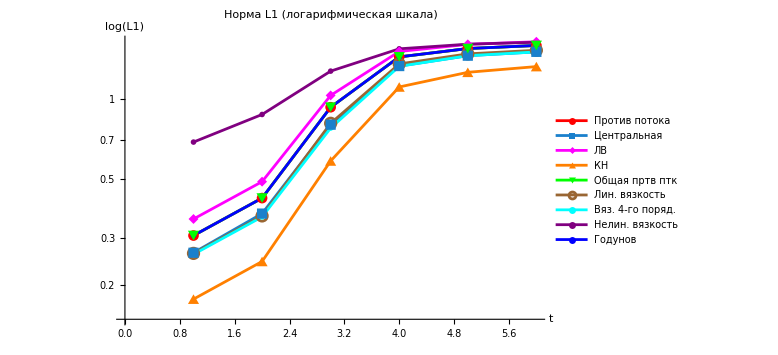

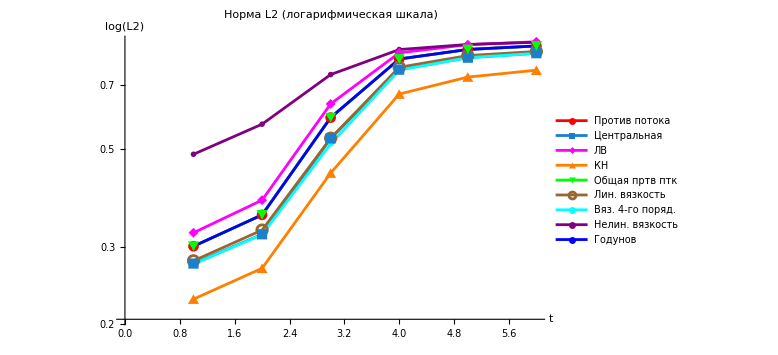

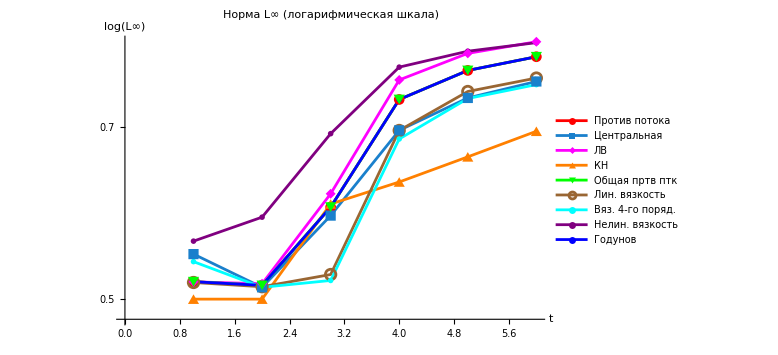

```mathematica
plotNormLog[1,"L1"]
plotNormLog[2,"L2"]
plotNormLog[3,"L∞"]
```

```mathematica
barAtFinalTime[normIndex_,normName_]:=BarChart[Table[errors[scheme]["t=40"][[normIndex]],{scheme,Keys[schemes]}],ChartStyle->(schemeColors/@Keys[schemes]),PlotLabel->Style["Норма "<>normName<>" при t = 40",14],ImageSize->Large]
```

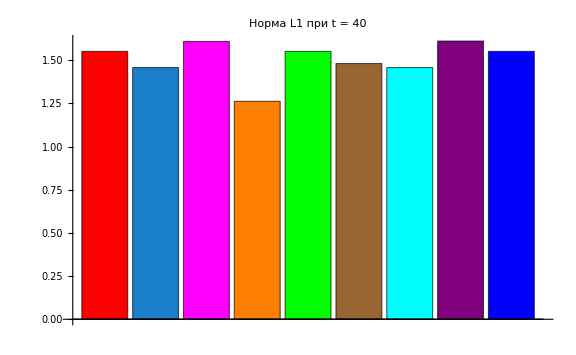

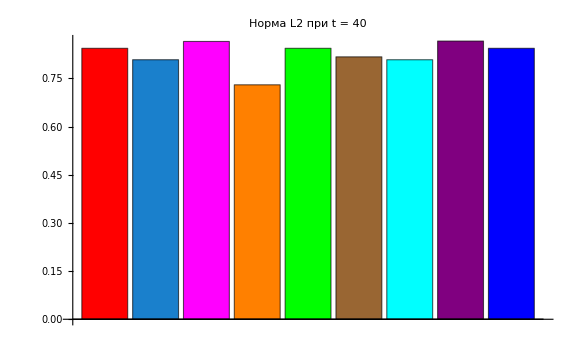

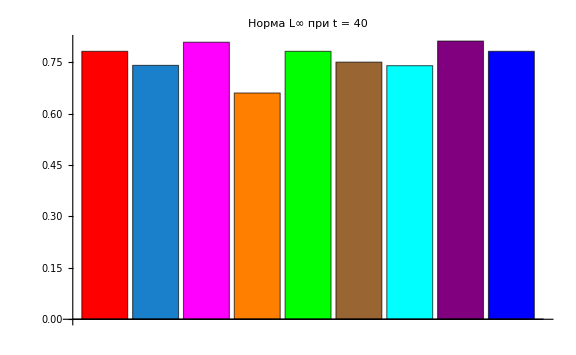

```mathematica
barAtFinalTime[1,"L1"]
barAtFinalTime[2,"L2"]
barAtFinalTime[3,"L∞"]
```

```mathematica
schemeNames=<|"Неявная против потока (3.14)"->{uImplicit,Red,True},"Неявная gen"->{uImplicitgen,Blue,True},"Неявная Лакс-Вендроффа (3.19)"->{uImplicitlaksven,Magenta,True},"Кранк-Николсон (3.15)"->{uImplicitCN,Orange,True},"Неявная апвинд (3.17)"->{uImplicitupwid,Green,True},"Линейная вязкость (3.20)"->{u320,White,True},"Вязкость 4-го порядка (3.18)"->{u318,Cyan,True},"Нелинейная вязкость (3.21)"->{u321,Purple,True},"Регуляриз. Лакс-Вендрофф (3.19)"->{u319,Brown,True},"Схема Годунова"->{uImplicitGod,RGBColor[0.1,0.5,0.8],True},"Аналитическое решение"->{Function[n,uAnalytic[#,(n-1) tau]&/@xgrid],Yellow,True}|>;

plotAt[n_]:=
Module[
{lines={},colors={},data,col,flag,yvals},
Do[
{data,col,flag}=schemeNames[name];
If[flag,yvals=If[Head[data]===Function,data[n],data[[n]]];
If[Length[yvals]===Length[xgrid],AppendTo[lines,Transpose[{xgrid,yvals}]];
AppendTo[colors,col]]],{name,Keys[schemeNames]}];
ListLinePlot[lines,PlotStyle->colors,PlotRange->{{1,3},{-0.1,1.2}},GridLines->Automatic,AxesLabel->{"x","u(x,t)"},PlotLabel->Style[Row[{"t = ",NumberForm[(n-1) tau,{3,2}]}],14,Bold]]];

stepForFrames=1; 
frameIndices=Range[1,nstep,stepForFrames];

frames=Table[plotAt[n],{n,frameIndices}];

Export["transport_schemes_a(t).gif",frames,"DisplayDurations"->0.03,"AnimationRepetitions"->Infinity];

(*Export["transport_schemes_a(t).mp4",frames,"FrameRate"->15];*)
```

```mathematica
ClearAll["Global`*"]

(*-----сетка и параметры-----*)
h=0.25;
xmax=20;
xgrid=Range[-xmax,xmax,h];
Nx=Length[xgrid];

tmax=6;
CFL=0.8;

(*-----начальная и аналитика-----*)
probfunc[x_]:=UnitStep[x];
uAnalytic[x_,t_]:=probfunc[Exp[-t] (x-1-t)+Exp[-t]];

(*-----limiter и поток-----*)
minmod[a_,b_]:=If[a b<=0,0,Sign[a] Min[Abs[a],Abs[b]]];
GodunovFlux[uL_,uR_,a_]:=If[a>=0,a uL,a uR];

(*-----начальные данные-----*)
u=probfunc/@xgrid;
uStore={u};
t=0;
tStore={t};

(*-----основной цикл-----*)
While[t<tmax,(*адаптивный CFL:скорость a(x,t)=x-t*)amax=Max[Abs[xgrid-t]];
tau=CFL h/amax;
If[t+tau>tmax,tau=tmax-t];
(*-----наклоны TVD (с ограничением на границах)-----*)slope=ConstantArray[0,Nx];
Do[uL=If[i==1,u[[1]],u[[i-1]]];
uC=u[[i]];
uR=If[i==Nx,u[[Nx]],u[[i+1]]];
slope[[i]]=minmod[(uC-uL)/h,(uR-uC)/h],{i,1,Nx}];
(*-----потоки на границах (всего Nx+1 грань)-----*)F=ConstantArray[0,Nx+1];
Do[(*Координата грани x_{i-1/2}*)(*Чтобы не выйти за пределы xgrid,считаем от xgrid[[1]]*)xFace=xgrid[[1]]-h/2+(i-1) h;
aFace=xFace-t;
(*uL берем из ячейки i-1,uR из ячейки i*)uLVal=If[i==1,u[[1]],u[[i-1]]+h/2 slope[[i-1]]];
uRVal=If[i==Nx+1,u[[Nx]],u[[i]]-h/2 slope[[i]]];
F[[i]]=GodunovFlux[uLVal,uRVal,aFace],{i,1,Nx+1}];
(*-----обновление через разность потоков-----*)uNew=u;
Do[(*u_i^(n+1)=u_i^n-tau/h*(F_{i+1/2}-F_{i-1/2})*)uNew[[i]]=u[[i]]-(tau/h) (F[[i+1]]-F[[i]]),{i,1,Nx}];
(*обновление данных*)u=uNew;
t=t+tau;
AppendTo[uStore,u];
AppendTo[tStore,t];];

(*-----визуализация-----*)
Manipulate[ListLinePlot[{Transpose[{xgrid,uStore[[k]]}],Transpose[{xgrid,uAnalytic[#,tStore[[k]]]&/@xgrid}]},PlotRange->{0,2.2},PlotStyle->{Red,{Blue,Dashed}},PlotLegends->{"TVD Godunov","Аналитическое"}],{k,1,Length[uStore],1}]
```

```mathematica
ClearAll["Global`*"]

(* =================параметры сетки=================*)
h=0.1;                (*пространственный шаг*)
xmax=20;
xgrid=Range[-xmax,xmax,h];
Nx=Length[xgrid];

tmax=6;               (*максимальное время*)
CFL=0.5;              (*CFL для RK2*)

(* =================скорость и аналитическое решение=================*)
velocity[x_,t_]:=x-t+1;
probfunc[x_]:=UnitStep[x];
uAnalytic[x_,t_]:=probfunc[Exp[-t] (x-t)];

(* =================MC лимитер=================*)
mcLimiter[a_,b_]:=Module[{c=(a+b)/2},If[a b<=0,0,Sign[a] Min[2 Abs[a],2 Abs[b],Abs[c]]]];

GodunovFlux[uL_,uR_,a_]:=If[a>=0,a uL,a uR];

(* =================вычисление наклонов (TVD)=================*)
calcSlopes[u_]:=Module[{uGhost},uGhost=Join[{u[[1]]},u,{u[[Nx]]}];(*фиктивные ячейки*)Table[mcLimiter[(uGhost[[i+1]]-uGhost[[i]])/h,(uGhost[[i+2]]-uGhost[[i+1]])/h],{i,1,Nx}]];

(* =================вычисление правой части (консервативная форма)=================*)
calcL[u_,t_]:=Module[{slope,F,uLedge,uRedge,xFace,aFace},slope=calcSlopes[u];
F=Table[xFace=xgrid[[1]]-h/2+(i-1)*h;
aFace=velocity[xFace,t];
uLedge=If[i==1,u[[1]],u[[i-1]]+h/2 slope[[i-1]]];
uRedge=If[i==Nx+1,u[[Nx]],u[[i]]-h/2 slope[[i]]];
GodunovFlux[uLedge,uRedge,aFace],{i,1,Nx+1}];
Table[-(F[[i+1]]-F[[i]])/h,{i,1,Nx}]];

(* =================фиксированный шаг времени=================*)
amax=Max[Abs[velocity[xgrid,0]]];
tau=CFL*h/amax;                  (*шаг времени по CFL*)
nSteps=Ceiling[tmax/tau];        (*количество шагов*)

(* =================массивы для хранения=================*)
uStore=ConstantArray[0.,{nSteps+1,Nx}];
tStore=Table[i*tau,{i,0,nSteps}];

(*начальное условие*)
uStore[[1]]=probfunc/@xgrid;
u=uStore[[1]];

(* =================основной цикл RK2=================*)
Do[L1=calcL[u,tStore[[n]]];
uStar=u+tau L1;
L2=calcL[uStar,tStore[[n]]+tau];
u=0.5 u+0.5 (uStar+tau L2);
uStore[[n+1]]=u;,{n,1,nSteps}];

(* =================визуализация=================*)
ListAnimate[Table[ListLinePlot[{Transpose[{xgrid,uStore[[k]]}],Transpose[{xgrid,uAnalytic[#,tStore[[k]]]&/@xgrid}]},PlotRange->{{-5,15},{-0.1,1.2}},PlotStyle->{{Red,Thick},{Blue,Dashed}},PlotLegends->{"TVD (MC + RK2)","Аналитическое"},PlotLabel->Row[{"t = ",NumberForm[tStore[[k]],{3,2}]}],GridLines->Automatic,ImageSize->Large],{k,1,nSteps+1}]]
```

```mathematica
ClearAll["Global`*"]

(*Параметры*)
h=0.25;
tau=0.05;
xmax=20;
nstep=400;

xgrid=Range[-xmax,xmax,h];
Nx=Length[xgrid];

probfunc[x_]:=UnitStep[x];

uAnalytic[x_,t_]:=probfunc[Exp[-t] (x-1-t)+Exp[-t]];

u=probfunc/@xgrid;

(*Основной цикл*)
Do[tCurr=(n-1) tau;
(*скорость на полуячейках*)aHalf=xgrid-tCurr;
(*матрица неявного upwind*)mat=ConstantArray[0,{Nx,Nx}];
Do[If[aHalf[[i]]>=0,mat[[i,i]]=1+tau/h aHalf[[i]];
mat[[i,i-1]]=-tau/h aHalf[[i]],mat[[i,i]]=1-tau/h aHalf[[i]];
mat[[i,i+1]]=tau/h aHalf[[i]]],{i,2,Nx-1}];
(*граничные условия*)mat[[1,1]]=1;
mat[[Nx,Nx]]=1;
rhs=u;
rhs[[1]]=uAnalytic[xgrid[[1]],tCurr];
rhs[[Nx]]=uAnalytic[xgrid[[Nx]],tCurr];
u=LinearSolve[mat,rhs];
If[n==1,uStore={u},uStore=Append[uStore,u]],{n,1,nstep}];

(*Визуализация*)
Manipulate[ListLinePlot[{Transpose[{xgrid,uStore[[n]]}],Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->{0,1.2},PlotStyle->{Red,Blue},PlotLegends->{"Неявный upwind (монотонный)","Аналитическое"}],{n,1,Length[uStore],1}]
```

```mathematica
ClearAll["Global`*"]

(*---Параметры---*)
h=0.25;
tau=0.05;
xmax=20;
nstep=400;

(*---Начальная функция---*)
probfunc[x_]:=UnitStep[x];

(*---Сетка---*)
xgrid=Range[-xmax,xmax,h];
Nx=Length[xgrid];

(*---Переменная скорость---*)
a[x_]:=1+0.5 Sin[x];

(*---Границы---*)
uLeft[t_]:=probfunc[-xmax];
uRight[t_]:=probfunc[xmax];

(*---Аналитика (характеристики)---*)
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-xmax,xmax}][[1]];
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[-t+(f[x]/. fsol)];

(*---Массивы---*)
uUpwind=ConstantArray[0.,{nstep+1,Nx}];
uTVD=ConstantArray[0.,{nstep+1,Nx}];
uImplicit=ConstantArray[0.,{nstep+1,Nx}];

uUpwind[[1]]=probfunc/@xgrid;
uTVD[[1]]=probfunc/@xgrid;
uImplicit[[1]]=probfunc/@xgrid;

(*========================*)
(*1. Upwind (явная)*)
(*========================*)
Do[Do[ai=a[xgrid[[i]]];
cfl=Abs[ai] tau/h;
If[ai>0,uUpwind[[n+1,i]]=uUpwind[[n,i]]-cfl (uUpwind[[n,i]]-uUpwind[[n,i-1]]),uUpwind[[n+1,i]]=uUpwind[[n,i]]-cfl (uUpwind[[n,i+1]]-uUpwind[[n,i]])];,{i,2,Nx-1}];
uUpwind[[n+1,1]]=uLeft[n tau];
uUpwind[[n+1,Nx]]=uRight[n tau];,{n,1,nstep}];

(*========================*)
(*2. TVD (MUSCL+minmod)*)
(*========================*)
minmod[a_,b_]:=If[a b>0,Sign[a] Min[Abs[a],Abs[b]],0];

Do[Do[ai=a[xgrid[[i]]];
cfl=Abs[ai] tau/h;
duL=uTVD[[n,i]]-uTVD[[n,i-1]];
duR=uTVD[[n,i+1]]-uTVD[[n,i]];
slope=minmod[duL,duR];
If[ai>0,uTVD[[n+1,i]]=uTVD[[n,i]]-cfl (duL+0.5 (slope-minmod[uTVD[[n,i-1]]-uTVD[[n,i-2]],duL])),uTVD[[n+1,i]]=uTVD[[n,i]]-cfl (duR-0.5 (minmod[uTVD[[n,i+2]]-uTVD[[n,i+1]],duR]-slope))];,{i,3,Nx-2}];
uTVD[[n+1,1;;2]]=uLeft[n tau];
uTVD[[n+1,Nx-1;;Nx]]=uRight[n tau];,{n,1,nstep}];

(*========================*)
(*3. Неявная схема (a=const)*)
(*========================*)
a0=1;
lambda=a0 tau/h;

matA=SparseArray[{Band[{1,1}]->(1+lambda),Band[{2,1}]->-lambda},{Nx,Nx}];

Do[uImplicit[[n+1]]=LinearSolve[matA,uImplicit[[n]]];
uImplicit[[n+1,1]]=uLeft[n tau];
uImplicit[[n+1,Nx]]=uRight[n tau];,{n,1,nstep}];

(*========================*)
(*АНИМАЦИЯ*)
(*========================*)
Manipulate[ListLinePlot[{Transpose[{xgrid,uUpwind[[n]]}],Transpose[{xgrid,uTVD[[n]]}],Transpose[{xgrid,uImplicit[[n]]}],Transpose[{xgrid,Table[uAnalytic[xgrid[[i]],n tau],{i,Nx}]}]},PlotStyle->{Red,Orange,Green,Yellow},PlotLegends->{"Upwind","TVD","Implicit","Analytic"},PlotRange->{0,1.2},GridLines->Automatic],{n,1,nstep,1}]
```